# PRIMAT (PRImordial MATter) Version with only a small network of nuclear reactions.

## Short description

*PRIMAT is a Mathematica code which computes the abundances of elements at the end of the big-bang nucleosynthesis (BBN).
It can be downloaded by registering at www2.iap.fr/users/pitrou/primat.htm.

*The implementation follows the presentation of Pitrou, Coc, Uzan, Vangioni, Physics Reports, 04, (2018) 005. 
All equation numbers, when non specified, refer to this companion paper, in its arXiv version (arXiv:1801.08023).

 *It is based on a previous Fortran code written by Alain Coc.

 *The user can choose the number of nuclear reactions involved in the reactions network. 
   -The minimal set of equations is made of 12 reactions involving selected isotopes of Hydrogen, Helium, Lithium and Berylium. 
   -The maximum set of equation is made of 423 reactions (including decay channels), with isotopes up to Z=11 (Na).
  
 *The user can modify several parameters which are in the preambule of the code :
 
   a) The reaction rates involved in the nuclear reaction network are tabulated in an external file which can be easily modified.
   b) The corrections to the weak-interaction reactions (n + ν <-> p^++ e^- and its related reactions), can be turned on and off with booleans. 
      The detail of these corrections is given in the companion paper.
   c) Cosmological parameters, that is essentially the number of baryons (Ω_b) and the number of neutrino generations N_ν can also be modified.
   
 *The numerical integration is performed in two steps. First the cosmology and the thermodynamics of the plasma are solved, 
   and then the nuclear reactions are computed, the backreaction of the latter on the former being negligible (see companion paper).
   
 *The results are given as a set of interpolating functions of time for the abundances of individual species. 
   If one is interested in final abundances only, these are also directly accessible by evaluating these functions at final time.

 *A very basic Monte-Carlo exploration of uncertainties is provided at the end of the code. It is used in associated example notebooks present in the Example folder.
   For each reaction, an uncertainty factor variance is provided and it is possible to run the code with these uncertainty parameters taking random values according to the variances (see [Coc et al. 2014]). A parallelization is possible for this Monte-Carlo exploration and the analysis of the results can be output in an external file and analyzed separatly.
   
   *Several examples and applications are gathered in the ‘Examples’ folder.

## Basic usage

*In the Evaluation menu, select ‘Evaluate notebook’. If asked the question ‘evaluate initialization cells first ?’, answer no. 
Then Mathematica proceeds in evaluating all cells, in order, and it should reach the end of the notebook (with the plots and results) in less than one minute.

*If the user erases the precomputed weak rates which are precomputed and stored in the ‘Interpolation’ folder, or asks for these rates to be re-precomputed, this can take considerably longer, typically a few tens of minutes.

*Furthermore, when PRIMAT-Main.nb (this notebook) is opened and saved in Mathematica, the cells which are' initialization cells' are saved into the file PRIMAT-Main.m.
This file contains then all the principal definitions and functions and variables which can be loaded from another notebook to perform BBN computations and analysis of results.
The 'Examples' Folder contains several typical applications which work exactly like that (first it loads all necessary definitions stored in PRIMAT-Main.m and then it performs a few useful computations for each selected example).

## Preambule

## Information

### Authors

This code is written and maintained by Cyril Pitrou^1 in collaboration with Alain Coc^2, J.-P. Uzan^3 and E. Vangioni^4.

^(1,3,4)Institut d’Astrophysique de Paris (CNRS)
      98 bis Boulevard Arago
      75014 Paris, France
  
^2CSNSM (CNRS, IN2P3)
  Orsay, France

emails and homepages :
-pitrou@iap.fr, http://www2.iap.fr/users/pitrou
-uzan@iap.fr
-vangioni@iap.fr
-alain.coc@csnsm.in2p3.fr

### Dates and versions

Version 0.1.1  (07/09/2018)

```mathematica
Date[]
```

{2018,9,10,10,56,34.185677}

Mathematica version used :

```mathematica
$Version
```

10.4.1 for Mac OS X x86 (64-bit) (April 11, 2016)

### GPL

```mathematica
(* Copyright (C) 2018- Cyril Pitrou, Alain Coc *)

(* This program is free software; you can redistribute it and/or
 modify it under the terms of the GNU General Public License as
 published by the Free Software Foundation; either version 2 of
 the License,or (at your option) any later version.

This program is distributed in the hope that it will be useful,
  but WITHOUT ANY WARRANTY; without even the implied warranty of
 MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU
 General Public License for more details.

You should have received a copy of the GNU General Public License
 along with this program; if not, write to the Free Software
 Foundation, Inc., 59 Temple Place-Suite 330, Boston, MA 02111-1307,
  USA. 
*)
```

### Bibliography

Herefater we use the following shorthands for the references cited.

BBN references

[Bernstein 1989] J. Bernstein, L. S. Brown, G. Feinberg, Rev. Mod. Phys 61 (1989).  
[Brown&Sawyer] L. S. Brown, R. F, Sawyer, Phys. Rev. D63, 083503 (2001) astro-ph/0006370.
[Cambier et al.] J. L. Cambier, J. R. Primack, and M. Sher, Nucl. Phys. B209, 372 (1982).
[Coc et al. 2012] A. Coc, S. Goriely, Y. Xu, M. Saimpert and E. Vangioni, Astrophys.J. 744 (2012) 1107.1117.
[Coc et al. 2014] A. Coc, J.-P. Uzan and E. Vangioni JCAP 1410 (2014) 050 1403.6694.
[Czarnecki et al. 2004] Czarnecki, Marciano and Sirlin, Phys Rev. D 70, 093006 hep-ph/0406324.
[Dicus et al.] D. A. Dicus, E. W. Kolb, A. M. Gleeson, E. C. G. Sudarshan, V. L. Teplitz, and M. S. Turner, Phys. Rev. D26, 2694 (1982).
[Esposito et al. 1999] S. Esposito, G. Mangano, G. Miele and O. Pisanti, Nucl. Phys. B540, 3 (1999) astro-ph/9808196.
[Grohs et al. 2012] E. Grohs, G. M. Fuller, C. T. Kishimoto, M. W. Paris, and A. Vlasenko, astro-ph/1512.02205.
[Horowitz] astro-ph/0109209 (for weak-magnetism definition and related computations).
[Horowitz&Li] C.J. Horowitz, G. Li, astro-ph/9908219
[Heckler 1994] A. F. Heckler, Phys. Rev. D49 611 (1994).
[Ivanov 2012] A. N. Ivanov, M. Pitschmann, N. I. Troitskaya Phys. Rev. D88, 073002 (2013) hep-ph/1212.0332. 
[Kernan] P. J. Kernan, PhD thesis, Two astroparticle physics problems; solar neutrinos, and primordial ^4 He. Ohio State University (1993).
[Lopez&Turner 1998] R. E. Lopez and M. S. Turner, Phys. Rev. D59, 103502 (1999) astro-ph/9807279.
[Lopez et al. 1997] R. E. Lopez, M. S. Turner and G. Gyuk, Phys. Rev. D56, 3191 (1997), astro-ph/9703065.
[Mangano et al. 2001] G. Mangano, G. Miele, S. Pastor, M. Peloso, astro-ph/0111408.
[Mangano et al. 2005] G. Mangano, G. Miele, S. Pastor, T. Pinto, O. Pisanti, P. D. Serpico, Nucl.Phys. B729 (2005) 221-234 hep-ph/0506164.
[PArthENoPE] O. Pisanti et al. Comp. Phys. Com 178 956 (2008), 0705.0290.
[Seckel 1993] D. Seckel, hep-ph/9305311.
[Sirlin 1967] A. Sirlin Phys. Rev. 164, Vol 5, p1767 (1967).
 


Other references. Incomplete neutrino decoupling :

[Hannestad 1995], S. Hannestad,  J. Madsen, Phys. Rev. D52, 1754 (1995), astro-ph/9506015.
[Gnedin 1997] N. Y. Gnedin, O. Y. Gnedin, AP. J. 509, 11-15 (1998), astro-ph/9712199.


Reaction rates 

They are listed in references of [Coc. et. al 2012] (see Table 4). We use the following acronyms :

NACRE (Angulo et al. 1999)
NACRE II (Xu et al. 2010, 2011)
DAACV04 (Descouvemont et al. 2004)
ILCCF10 (Iliadis et al. 2010)
CF88 (Caughlan& Fowler 1988)
MF89 (Malaney& Fowler 1989)
Boy93 (Boyd et al. 1993)
Bal95 (Balbes et al. 1995)
Hei98 (Heil et al. 1998)
Rau94 (Rauscher et al. 1994)
Des99 (Descouvemont 1999)
Bea01 (Beaumel et al. 2001)
Tan03 (Tang et al. 2003)
Wan91 (Wang et al. 1991)
Efr96 (Efros et al. 1996)
Wie87 (Wiescher et al. 1987 Wiescher,Harms,Goerres,Thielemann& Rybarcyk ApJ 316 (1997) 162  1001.2053)
Bar97 (Bardayan& Smith 1997)
Koe91 (Koehler& Graff 1991)
And06 (Ando et al. 2006)
Ser04 (Serpico et al. 2004)
Wag69 (Wagoner 1969)
Has09 (Hashimoto et al.2009)
Wie89 (Wiescher et al.1989)
FK90 (Fukugita& Kajino 1990)
Bru91 (Brune et al.1991)
Bec92 (Becchetti et al.1992)
Iga95 (Igashira et al.1995)
Cyb08 (Cyburt& Davids 2008)
Miz00 (Mizoi et al. 2000)
Nag06 (Nagai et al. PRC 74 (2006) 025804 AC2010)
Has09c (Hashimoto et al.PLB 674 (2009) 27)
FK90  (Fukugita& Kajino,PRD 42 (1990) 4251)
Rau94 (C. Rauscher et al.ApJ 429 (1994) 499)
Men12 (C Mendes et al.PRC 86 (2012) 064321)
Tang03 (Tang et al.PRC 67 (2003) 015804)
Bar97C (Bardayan& Smith PRC 56 (1997) 1647)
Kaw91 (Kawano,Fowler,Kavanagh,Malaney ApJ 372 (1991) 1-7)
Cam08 (Camargo et al.Phys.Rev.C 78,034605 (2008))
Ili16 (Iliadis et al. 2016)

Numerical values

[Planck 2015 XIII] Ade et al. A.&A. 594, A13 (2016).
[PDG] Particle Data Group 2017.

## Options

### Directory set up

We set the directory.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pitrou/Dropbox/iap/notebooks/BBN

To check what is the directory of your notebook :

```mathematica
Print["The current Directory is ",Directory[]]
```

The current Directory is /Users/pitrou/Dropbox/iap/notebooks/BBN

### Numerical options

Miscellaneous options

```mathematica
$InterpolateAnalytics=True;
```

It is slightly faster to interpolate the analytic expressions of nuclear reaction rates. Setting $InterpolateAnalytics to True is recommended.

```mathematica
$HistoryLength=10;
```

This is to avoid Mathematica to store too many results in memory. Only the past $HistoryLength results are kept in computer memory (this is standard Mathematica option).

```mathematica
$PaperPlots=False;
$ResultsPlots=False;
```

If $PaperPlots is set to True, the most important plots are constructed and they are output in pdf in the ‘Plots’ subfolder. 
Unless interested in reproducing the plots of the companion paper, this should be set to False to avoid any loss of time in the code.

If $ResultsPlots is True the results for the abundances are plotted at the end. Similarly, to avoid loss of time this shouldbe set to False.

Numerical precision

```mathematica
$CompileNDSolve=True;
```

If $CompileNDSolve is set to True (advised), then the differential equation solver uses compiled functions. This is slightly faster.

```mathematica
$BDFOrder=2;
```

Order of numerical scheme for Backward Differentiation Scheme (BDS) integration. 
-Order 1 works well but it is slow. 
-Order 2 (advised) is faster. Higher orders result in numerical crash.

```mathematica
PrecisionNDSolve=2;(*TODO Put 2 here !!!! *)
```

PrecisionNDSolve is a precision parameter used in the differential equation solver. It is tuned such that 0 gives reasonable results, 1 gets very good results, and 2 gets excellent results and 3 gets super dupper precise results (10^-5 precision).

```mathematica
AccuracyNDSolve:=15+PrecisionNDSolve;
```

We slave AccuracyNDSolve to PrecisionNDSolve. This is roughly the number of digits of precision behind the dot, so increasing it will lead to always better results but this can crash if the accuracy required is too strong.

```mathematica
NTemperaturePoints=1200; (*1000 is enough*)
```

Number of points in discretization of temperature between the highest temperature (10^12 K) and the lowest (~10^7.5K).  1000 is enough.
Sampling is performed with NTemperaturePoints+1 points. Spacing is performed logarithmically, with Log_10.

```mathematica
InterpOrder=3;
```

Order of polynomials used in interpolations of reaction rates. Usually with Spline functions.

```mathematica
$FastPENRatesIntegrals=True;
```

If $FastPENRatesIntegrals is set to True, it uses a Simpson method for numerical integrals. Otherwise it uses the Mathematica function NIntegrate which is more accurate (adaptative refinement of integral) but much slower.

```mathematica
$PENRatesIntegralsPoints=300;(*200 is enough *)
```

In case $FastPENRatesIntegrals is set to True, $PENRatesIntegralsPoints is the number of points used to perform the numerical integrals. 200 is enough. 400 is ultra precise.

```mathematica
SetOptions[SelectedNotebook[],PrintPrecision->8]
```

We increase the number of digits which are displayed

### BBN

Nuclear rates

Most nuclear reactions rates are tabulated in a separate file. The rest of the rates are given as analytic fits.
The external file loaded with all reactions definitions and rates is given by the name TabulatedReactionsFile.

We can choose to use this file but only keep a subnumber of equations defined by NumberNuclearReactions. 

The small network corresponds to NumberNuclearReactions=12.
 
If we want to add reactions which are given by analytic formula this number should be increased accordingly.

```mathematica
TabulatedReactionsFile="BBNRates_2018_11reactions.dat";
NumberNuclearReactions=12;
```

We can also decide to keep only a subset of the equations by specifying the maximum nuclear mass. The default value is Infinity, meaning that we do not cut the network.

```mathematica
MaximumNuclearMass=Infinity;
```

Monte-Carlo uncertainty estimation options

```mathematica
$RandomNuclearRates=False;
$MaxVariationRate=1000;
```

If $RandomNuclearRates is True, then each time we generate the equations we generate rates with a log normal distribution according to the ‘f’ specified (see Eq. 4.5 of [Coc et al. 2014] for definition of f). 
We limit f to the values 1/$MaxVariationRate<f<$MaxVariationRate .

Rescaling of some rates

This is a rescaling factor for the d + p -> He3 + γ reaction. It can be varied so as to obtain constraints on this reaction rates from measured abundance.

```mathematica
dpTOHe3gFactor=1;
```

### Corrections for weak rates

Since the weak interaction rates, that is the rates of weak reactions of the type n + ν <-> p + e and associated reactions, depend only on temperature, 
these can be computed once and for all so as to explore the dependence in cosmological parameters or other parameters. 
  
If $RecomputeWeakRates is set to True, the code recomputes the weak rates. 
Otherwise it reads them from files previously stored. If the file does not exist it recomputes the rates.

If $ParallelWeakRates=True this is done using parallelization over the various CPUs that Mathematica can detect.

```mathematica
$RecomputeWeakRates=False;
$ParallelWeakRates=True;
```

There are several booleans corresponding to the different types of corrections which can be considered in these weak rates. 
The name of the file used for storing the rates is built out of these booleans. 

Since the corrections do not add linearly, there are in principle many choices of corrections, but the only meaningful
choices are those without any corrections and those with all corrections included. 
Or maybe those with just one correction added, so as to check its amplitude.

```mathematica
$RadiativeCorrections=True;

$ResummedLogsRadiativeCorrections=True;
$RelativisticFermiFunction=True;
```

1) If $RadiativeCorrections is set to True, we use Coulomb and radiative corrections (see section III.E of companion paper. The corrections are implemented in Eqs. 101 and 104.).
If $ResummedLogsRadiativeCorrections is set to True we use Eq. 15 of [Czarnecki et al 2004] which amounts to resumming some higher order radiative corrections, and this is also Eq. B35 of the companion paper.

If $ResummedLogsRadiativeCorrections is False we use simply Eq. 7 of the same reference, which corresponds to Eq. 103 and B30 of the companion paper.
If $RelativisticFermiFunction is True we use the relativistic Fermi function (Eq. 5 in [Ivanov 2012]), which corresponds to Eq. 100 of the companion paper. Otherwise we use the standard non-relativistic Fermi function, given by Eq. 99 of the companion paper.

```mathematica
$RadiativeThermal=True;
$CorrectionBremsstrahlung=True;
```

2) If $RadiativeThermal set to True, the thermal radiative corrections are taken into account. 
The first expressions date back from [Dicus et al.]. However other expressions were derived subsequently in [Lopez&Turner 1998], [Cambier et al.] and [Esposito et al. 1999] among other references. [Kernan] pointed typos and compared the differing results of [Cambier et al.] and [Dicus et al.]. These were correctly computed in [Brown&Sawyer].
In the companion paper, the thermal radiative corrections are given by Eq. 108 with the various contributions given by Eqs. 109-113. However, it is easier to compute the first contribution of 108 using Eqs. 109 (with definition B41), but to compute the second and third contributions of 108 using Eqs. B50-B51.

We showed in companion paper that Bremsstrahlung corrections need also to be added to be fully consistent with [Brown&Sawyer]. This is controlled by the boolean $CorrectionBremsstrahlung. If $RadiativeThermal is set to True, then these bremsstrahlung corrections (corresponding to Eqs. 107a and 107b in companion paper with the definitions B48-B49) are also incorporated if $CorrectionBremsstrahlung is True.

```mathematica
$FiniteNucleonMass=True;
```

3) If $FiniteNucleonMass is set to True, we take into account the finite mass of nucleons by keeping corrections in 1/M_n in the collision integrals of the weak rates.
Our method is described in the companion paper and differs from earlier literature.
There is a suboption for these finite mass corrections  which is

```mathematica
$CoupledFMandRC=True;
```

If $CoupledFMandRC is False, finite mass corrections are computed from the Born results with no radiative null temperature corrections. If this is set to True, the finite mass corrections are applied to the rates on which the Coulomb and radiative corrections are taken into account. True is the advised value. 

The expressions implemented are Eqs. 114 when $CoupledFMandRC is False, with the definition B23. If $CoupledFMandRC is True, then we use Eqs. 115 with the Fermi and radiative corrections corresponding to the above choices for radiative corrections.

4) Mass shifts due to QED plasma effects are ALREADY taken into account in thermal radiative corrections.
However it is possible to turn the option $QEDMassShift to true to check how this affects the rate when taken individually.
Apart to satisfy this curiosity, this option should be set to False in all cases.

```mathematica
$QEDMassShift=False;
```

### Plasma corrections

```mathematica
$QEDPlasmaCorrections=True;
$CompleteQEDPressure=True;
```

If $QEDPlasmaCorrections is set to True, the QED corrections to the pressure and the energy density are taken into account. This affects for instance the expansion rate via the Friedmann equation. 
Expressions can be found in [Lopez&Turner 1998], [Mangano et al. 2001] or in [Heckler 1994]. See also the companion paper where Eqs. 48-52 are used inside Eq. 55 to modify the entropy and Eq. 58 to modify the energy density.
If $CompleteQEDPressure is False, the subdominant term is ignored. Otherwise it is included. We checked it is so subdominant that it does not change the results.

```mathematica
$IncompleteNeutrinoDecoupling=True;
```

If $IncompleteNeutrinoDecoupling is set to True we use a fit for the heating function of the neutrinos due to incomplete decoupling. Indeed if we consider the details of the decoupling of neutrinos, it is found that decoupling is incomplete by the time electrons and positrons annihilate into photons. This results in a slightly overheating of neutrinos and cooling of the electrons/photons plasma. In principle, one should also take into account the spectral distortions that this heating induces on the neutrinos. But neglecting it we can use a fit of the neutrinos heating functions and assume that neutrinos always stay thermalized. This allows to graps most of the effect on the abundance of Helium. The fitting functions which is used is the one given in [PArthENoPE]. It is used in Eq. 63 of the companion paper.
The advised value for $IncompleteNeutrinoDecoupling is True.

```mathematica
$RecomputePlasmaCorrections=False;
```

Since the QED effects depend on temperature, they need to be computed only once for all and they are stored on a file. But we can force the recomputation of these corrections by setting $RecomputePlasmaCorrections to True;

### Degenerate Neutrinos

```mathematica
$DegenerateNeutrinos=False;
μOverTν=0.0;
```

If neutrinos have a chemical potential, then $DegenerateNeutrinos = True. Standard BBN is with non-degenerate neutrinos and when $DegenerateNeutrinos = False the value of μOverTν is ignored. Note that in the case of degenerate neutrinos, one must run the code with RecomputeWeakRates = True because this modifies the weak rates. And for every value of μOverTν one must recompute the weak rates.
μOverTν is also noted ξ_ν in the companion paper. See section VI.C.

## Initial definitions

### Temperature eras

We choose to split the BBN numerical calculations in three eras. 
 1) First the high temperature era between Tstart=10^11 K and TMiddle. Only neutrons and protons abundances are tracked and this is ruled by weak interactions. 
 2) The intermediary era, between TMiddle and T18, where only a small network of reactions (17 nuclear reactions plus weak interactions or possibly less) is used.
 3) A low temperature region, between T18 and Tend, where Tend is usually slightly lower than 10^8 K, typically Tend=6 10^7 K.
 
 So we have Tstart > TMiddle > T18 > Tf.

```mathematica
Kelvin=1;
Tstart=10^11 Kelvin;
TMiddle:=0.9999*10^10 Kelvin;
T18:=1.25 *10^9 Kelvin;
Tend=6.*10^7 Kelvin;
```

### Temperature sampling

We choose to sample temperature starting from 10^12 K. This is interesting to check high T behaviour of some effects.

```mathematica
Ti=10^12 Kelvin;
Tf=10^7 Kelvin;
LogTi=1.Log10[Ti];
LogTf=1.Log10[Tf];
```

We first build the list of LogT points (ListLogT) and then the list of T points (ListT).

```mathematica
ListLogT=Sort@DeleteDuplicates@Join[{10.},Table[i,{i,LogTf,LogTi,(LogTi-LogTf)/NTemperaturePoints}]];
ListT=1. 10^ListLogT;
```

```mathematica
ListTRange[T1_,T2_]:=Module[{len=Length@ListT,imindown,imaxup,Tmin=Min[T1,T2],Tmax=Max[T1,T2]},
imindown=Max[1,-1+Position[ListT,SelectFirst[ListT,#>Tmin&]][[1,1]]];
imaxup=Min[len,Position[ListT,SelectFirst[ListT,#>=Tmax&]][[1,1]]];
ListT[[imindown;;imaxup]]
]
```

ListTRange is a function to select a sublist in this list of temperature, according to a range of temperature which makes sure to have either the points on the boundary or at least one point beyond (to avoid problems with interpolating functions).
If T = 10^10 is not in the list, we add it to avoid problems with interpolations of reactions rates which all start at 10^10 and below.

### Constants of Physics

cgs system

We use cgs system with Kelvin. (For instance an erg is 1 g cm^2 s^-2).
By definition these are set to one in these units. Any change of system of units can be made by modifying these variables only.

For instance if we want to use the m/kg/s system we need only put cm=0.01 and gram = 0.001 below.

As a check, final results should not depend on these conventions since abundance rates are dimensionless.

```mathematica
second=1;
cm=1;
gram=1;
```

When taking values from the kg/m/s system, we use the factors

```mathematica
kg=10^3 gram;
meter = 10^2 cm;
km=10^3 meter;
Joule =kg meter^2/second^2; (* This gives 10^7 ergs *)
DensityUnit=gram/cm^3;
Hz=1/second;
```

```mathematica
Giga=10^9;
Mega=10^6;
Kilo=10^3;
```

Fundamental constants

```mathematica
kB =1.3806488 10^-23 Joule / Kelvin;(* Boltzmann constant in J/K *)
clight=2.99792458*10^8*meter/second; (* speed of light in cm/s *)
hbar= 6.62606957/(2π)10^-34(*1.054571596 10^-34*) Joule second;
Avogadro=6.0221415 10^23;
```

When using masses of particles, we use eV and MeV that we convert in the cgs system

```mathematica
eV=1.60217653 10^-19 Joule;
keV = Kilo eV;
MeV=Mega eV;
GeV=Giga eV;
```

Interactions constants

```mathematica
GN=6.67384 10^-11 meter^3/kg/second^2; (* Gravitation constant *)
GF=1.1663787*10^-5/(GeV)^2; (* Fermi Constant*)
gA=1.2723; 
(* Axial current constant of structure of the nucleons Particle data group : 1.2723(+-23) PDG2016 *)
(* However post 2002 data suggest 1.2755(11) as advised by William Marciano*)
```

```mathematica
fWM=3.7058/2(*1.853*); (* Weak magnetism see 1212.0332*)
radiusproton=0.841*10^-15 meter (*(arXiv:1212.0332)*)
```

8.41×10^-14

```mathematica
fWM
```

1.8529

fWM is the weak magnetism constant.  See Eq. [Horowitz&Li] for definition with the value given by its Table 1. 
Note that all expression in [Seckel 1993] seem to have a factor 2 difference. That is all interaction rates involving the weak magnetism in [Seckel 1993] are underestimated by a factor 2. Expressions in [Lopez et al. 1997] seem correct however.

```mathematica
αFS=1/137.03599911;(* Fine structure constant =e^2/(4π) *)
```

Particle masses

Throughout, masses stand always for mc^2 so that they are in fact energies. This avoids putting unnecessary c^2 factors

```mathematica
me=0.510998918 MeV; 
mn=939.565360 MeV;
mp=938.272029 MeV; 
Q=mn-mp; (* Mass difference between neutrons and protons *)
Subscript[m, Nucleon]=mn;

Subscript[m, W]=80.385 GeV; (* Mass of the W Boson. *) 
Subscript[m, Z]=91.1876 GeV;
```

The energy difference between neutron and proton in Mev is

```mathematica
Q/MeV
```

1.29333

Cosmology constants

h is the Hubble rate in units of 100 km/s/Mpc.

```mathematica
pc=3.0856777807 10^16 meter; (* The parsec *)
Mpc=Mega pc;
H0=100 h km/second/Mpc; (* Hubble constant today *)
H100=100 km/second/Mpc;(*Fake Hubble rate given by 100 km/s/Mpc so that h = H0/H100 *)
```

We define two critical densities. One for the actual Hubble rate, and one for the rate at 100km/s/Mpc.

```mathematica
Subscript[ρ, crit]=3./(8π GN)(H0)^2 (* in g cm^-3 by construction *)
ρcrit100=3./(8π GN)(H100)^2 (* in g cm^-3 by construction *)
```

1.87847×10^-29 h^2

1.87847×10^-29

Neutron life time (Particle Data Group 2017).

```mathematica
Meanτneutron:=879.5(*880.2second+-1.1s was previous value from PDG2017 *);
(* Now we use 1712.05663 Section 11 which includes recente 2017 measurements.*)
στneutron:=0.8 second;
τneutron=Meanτneutron;
```

### Cosmological Parameters

Neutrinos generations and possible neutrino degeneracy (neutrino chemical potential).

```mathematica
NeutrinosGenerations:=3.;
ξν:=If[$DegenerateNeutrinos,μOverTν,0];
```

```mathematica
ρFD[c_]=1/(2 π^2)∫_0^Infinity y^3/(ⅇ^(y-c)+1)ⅆy;
nFD[c_]=1/(2 π^2)∫_0^Infinity y^2/(ⅇ^(y-c)+1)ⅆy;
ρFDNonDegenerate=ρFD[0];
```

Information

```mathematica
Series[(ρFD[c]+ρFD[-c])/(2ρFDNonDegenerate),{c,0,4}];
```

```mathematica
ην[c_]=(nFD[c]-nFD[-c])/(2Zeta[3]/π^2);
Series[ην[c],{c,0,3}];
```

Effective number of neutrinos generation due to chemical potential 
(this is different from N_eff which takes into account also QED and incomplete neutrino decoupling)

```mathematica
Nneu:=NeutrinosGenerations*(ρFD[ξν]+ρFD[-ξν])/(2ρFDNonDegenerate)
```

CMB temperature today

```mathematica
TCMB0:=2.7255Kelvin;
σTCMB0:=0.0006 Kelvin;(* [Planck 2015 XIII] *)
```

Temperature of CMB today in Kelvin. We consider the case where QED effects are ignored or taken into account. This is the implementation of (the inverse of) Eq. 56 in companion paper.

```mathematica
FourOverElevenQED:=4/11(1+(25 αFS)/(22π));
FourOverElevenNoQED:=4/11;
FourOverEleven:=If[$QEDPlasmaCorrections,FourOverElevenQED,FourOverElevenNoQED];

Tν0=(FourOverEleven)^(1/3)TCMB0;
```

```mathematica
(1/FourOverEleven)^(1/3)
```

1.39979

Temperature of neutrinos today is lower than photons because they decoupled earlier and electron/positron annihilation has only reheated photons. This leads to the famous ratio of 4/11 between the T^3 of the neutrinos and photons. However, since decoupling is slightly incomplete, this in principle should be corrected like in [Mangano et al. 2005] or [Grohs et al. 2012]. 

Additionally, there is another source of modification to this 4/11 ratio which comes from the QED corrections to the plasma thermodynamic quantities (modification of pressure and energy density and thus of entropy). Taking the high temperature modification leads to the correction added above in the variable FourOverEleven. See e.g. Eq. 41 of [Lopez&Turner 1998] and/or the companion paper (Eq. 56). The effect of incomplete neutrino decoupling is considered further below.

Hubble rate in units of 100 km/s/Mpc.

```mathematica
h:=0.6727; (*+-0.0066 *)(*[Planck 2015 XIII]*)
```

Baryons and Cold Dark Matter density fraction. This is Ω_b h^2 and Ω_c h^2.

```mathematica
Meanh2Ωb0Planck=0.02225;(*[Planck 2015 XIII TT and ET and EE]*)
σh2Ωb0Planck=0.00016;(* Standard deviation*)
```

```mathematica
Meanh2Ωb0=Meanh2Ωb0Planck; 
σh2Ωb0=σh2Ωb0Planck;
h2Ωb0=Meanh2Ωb0;
```

```mathematica
ReSetCosmology:=(
Meanh2Ωb0=Meanh2Ωb0Planck; 
NeutrinosGenerations=3;
);
```

```mathematica
Meanh2Ωc0=0.1198;(* [Planck 2015 XIII]*)
σh2Ωc0=0.0015;
h2Ωc0=Meanh2Ωc0;
```

Cosmological constant fraction Ω_Λ. Obtained by summing baryons and cold dark matter, given that radiation is negligible today.
This is just for information and it is not used since the cosmological constant is totally negligible for its influence in the expansion rate during BBN.

```mathematica
1-(h2Ωb0+h2Ωc0)/h^2
```

0.686095

### Density of photons and neutrinos

The Black Body constant is defined as

```mathematica
aBB=π^2/(15 hbar^3(clight)^5)
```

2.31674×10^28

Energy density and number density of CMB today (See appendix A1 in companion paper)

```mathematica
Subscript[ρ, CMB0]:=aBB (kB TCMB0)^4 ;(* in g cm^-3*)

Subscript[n, CMB0]:=(2 Zeta[3])/(π^2 hbar^3(clight)^3)(kB TCMB0)^3
```

We recover the number of photons per cubic centimeter (410) :

```mathematica
Subscript[n, CMB0]
```

410.727

The fraction of energy content due to photons is simply

```mathematica
Subscript[Ω, γ0]:=Subscript[ρ, CMB0]/Subscript[ρ, crit];
```

For neutrinos, we must take into account the temperature of neutrinos today, the number of neutrinos, and the fact that they are Fermions. 
See companion paper for details.

```mathematica
Subscript[Ω, ν0]:=Nneu*7/8*(FourOverEleven)^(1/3)Subscript[Ω, γ0];
```

The contribution to the energy content is obtained by the ratio between energy densities and critical density. We check that today it is around 0.1%.

```mathematica
(Subscript[Ω, γ0] h^2)/h2Ωb0
```

0.00111137

### Density of baryons

```mathematica
ma = 931.494061 MeV;(* Audi2012 *)
He4Overma=4.0026032541; (* Audi2012 *)
H1Overma=1.00782503223; (* Audi2012 *)
```

The atomic mass, the Helium4 mass (in units of atomic mass) and Hydrogen mass (in units of atomic mass).

```mathematica
Subscript[x, He4]=0.24709 ;(* Chemical composition at the end of BBN. In principle one should account for He4 produced by stars...*)
Subscript[x, H1]=1-Subscript[x, He4];
mbaryon0=(Subscript[x, H1] H1Overma+Subscript[x, He4] He4Overma/4)ma;
```

This is the (average) mass of baryons today (that is of nucleons), taking into account that part is in Hydrogen and part in Helium. We use the current chemical composition with 24.75 % of Helium but this is subject to controversy. Indeed the abundance of baryons is measured with CMB, and thus refers to an epoch (z ~1100) where the composition was the same as the one at the end of BBN. See Eqs. C5 C6 in companion paper.

```mathematica
mbaryon0/ma
ma/mbaryon0
```

1.00605

0.993984

```mathematica
(He4Overma/4-H1Overma)/H1Overma
%*Subscript[x, He4]
```

-0.00711852

-0.00175891

The number density of baryons, that is of nucleons is then given by the baryons mass density divided by the average mass of baryons.

```mathematica
ρB0 :=h2Ωb0*ρcrit100;
```

```mathematica
nbaryons0:=ρB0/(mbaryon0/(clight)^2)
```

The ratio between baryons number and photons number is by definition the η parameter and its value for the parameters chosen is

```mathematica
nbaryons0/Subscript[n, CMB0]
```

6.09133×10^-10

It is convenient to define the ratio between Ω_b h^2 and this η parameter.

```mathematica
Ωbh2Overη:=Subscript[n, CMB0]/ρcrit100 mbaryon0/(clight)^2
```

```mathematica
Ωbh2Overη
```

3.65274×10^7

The η parameter is then obtained from the baryon density fraction as

```mathematica
ηfactor:=h2Ωb0/Ωbh2Overη
```

Baryons density is obtained from its valued today scaled by dilution (no thermal effects, so it is only the energy density due to rest mass of baryons).

```mathematica
ρB[av_]:=ρB0/av^3;
nB[av_]:=nbaryons0/av^3;
```

For nuclear reactions, the mass density of baryons is in fact a number density of species multiplied by the atomic mass (see appendix C1 of companion paper for a detailed discussion). 
This differs slightly from the mass density of baryons and we take this into account.

If $CorrectBaryonsEnergyDensityinBBNRRates is set to False, then we use the baryons density naively in nuclear rates. 
Otherwise we take into account that the baryons density is in fact the number density times the atomic mass as explained in App. C1 of the companion paper.

```mathematica
$CorrectBaryonsEnergyDensityinBBNRRates=True;
ρBForBBN[av_]:=ρB[av]If[$CorrectBaryonsEnergyDensityinBBNRRates,ma/mbaryon0,1];(* This is Eq. C8 of the companion paper *)
```

### Distribution functions

Basic Fermi - Dirac (FD) and Bose - Einstein (BE) functions. x here 1/(k_B T).

```mathematica
FD[EoverT_]=1/(Exp[EoverT]+1);(* Fermi Dirac Distribution *)
FD[Energy_,x_]=1/(Exp[x Energy]+1);
BE[EoverT_]=1/(Exp[EoverT]-1); (* Bose Einstein Distribution *)
BE[Energy_,x_]=1/(Exp[x Energy]-1);

(* For neutrinos with a chemical potential *)
FDν[Energy_,ϕ_,x_]=1/(Exp[x Energy-ϕ]+1);
```

Derivatives of FD wrt to energy.

```mathematica
FDp[Energy_,x_]=D[1/(Exp[x Energy]+1),Energy];
```

### Customized Mathematica tools

This function NP displays a certain number of digits for a given real number

```mathematica
NP[number_]:=NumberForm[number,8]
```

This function displays a table in grid form, that is with lines between the entries

```mathematica
MyGrid[Table_List]:=Grid[Table,Frame->All]
```

This function performs interpolation on a list of points (x, f(x)) to the required order.

```mathematica
MyInterpolation[Tab_List]:=Interpolation[Tab,InterpolationOrder->InterpOrder];

(* Does not work to interpolate the log of rates because it fails when rates vanish !!!*)
MyInterpolationLog[Tab_List]:=Function[{x},Exp[Interpolation[{#[[1]],Log[#[[2]]]}&/@Tab,InterpolationOrder->InterpOrder][x]]];

$InterpolateLogRate=False;
MyInterpolationRate[Tab_List]:=If[$InterpolateLogRate,MyInterpolationLog[Tab],MyInterpolation[Tab]]
```

Tools to avoid too small numbers in numerics.
MyChop chops small numbers and replaces them by 0.

```mathematica
MyChop[el_?NumericQ]:=(Chop[el,$MinMachineNumber]);
SetAttributes[MyChop,Listable];
```

Redefinition of Set to allow to set values to quantities already set

```mathematica
MySet[Hold[expr_],value_]:=(expr=value);
MySetDelayed[Hold[expr_],value_]:=(expr:=value);
```

Personal simple integral with second order polynomial interpolation (Simpson method).

```mathematica
TableSimpsonC=Compile[{{a,_Real},{b,_Real},{Np,_Integer}},With[{h=1.(b-a)/Np,n2=Np/2},With[{h3=h/3.},Join[{{a,h3}},Table[{a+2. j h,2 h3},{j,1,n2-1}],Table[{a+(2. j-1) h,4 h3},{j,1,n2}],{{b,h3}}]]],CompilationTarget->"C","RuntimeOptions"->"Speed"];
```

Generic compilation of a function and of its integration.

```mathematica
MyCompile[LV_List,Body_]:=Compile[LV,Evaluate[Body],"RuntimeOptions"->"Speed",CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeAttributes->{Listable}]
```

Compilation of a scalar product.

```mathematica
V1dotV2=Compile[{{V1,_Real,1},{V2,_Real,1}},V1.V2,CompilationTarget->"C","RuntimeOptions"->"Speed"];
```

Compiled version of the Simpson integral

```mathematica
IntegrateFunction[fun_,pemin_,pemax_,Np_]:=With[{interv=(pemax-pemin)/(Np),tab=TableSimpsonC[pemin,pemax,Np]},V1dotV2[tab[[All,2]],MyChop[fun[tab[[All,1]]]]]];
```

A function to import an external file and which returns an error and quits if the file does not exist.

```mathematica
SafeImport[args__]:=Module[{out},out=Catch[Check[Import[args],Print["File ",{args}[[1]]," not found. Quiting Kernel."];Throw[$Failed];,Import::nffil]];If[out===$Failed,Quit[]];out]
```

Tools for plots. Some useful grid of ticks

```mathematica
MyFrameTicksLog={{Automatic,Automatic},{{{Log[10^8],"10^8"},{Log[10^8.5],"10^8.5"},{Log[10^9],"10^9"},{Log[10^9.5],"10^9.5"},{Log[10^10],"10^10"},{Log[10^10.5],"10^10.5"},{Log[10^11],"10^11"},{Log[10^11.5],"10^11.5"}},Automatic}};

MyFrameTicks={{Automatic,Automatic},{{{10^8,"10^8"},{10^8.5,"10^8.5"},{10^9,"10^9"},{10^9.5,"10^9.5"},{10^10,"10^10"},{10^10.5,"10^10.5"},{10^11,"10^11"},{10^11.5,"10^11.5"}},Automatic}};
```

## Thermodynamics of the plasma

## Thermodynamic integrals

Defined in appendix A1 of companion paper. These are the integrals needed to obtain the thermodynamic quantities of FD or BE distributions and correspond to Eqs. A5 in companion paper.

```mathematica
Clear[Imn]
Imn[sgn_][m_,n_][x_]:=NIntegrate[((pe^2+x^2)^((m-1)/2)pe^(n+1))/(Exp[√(pe^2+x^2)]+sgn),{pe,0,Infinity},Method->{Automatic,"SymbolicProcessing"->0}]
ImnT[sgn_][m_,n_][T_]:=Imn[sgn][m,n][me/(kB T)]

(* Interpolations *)
ImnI[sgn_][m_,n_]:=ImnI[sgn][m,n]=Interpolation@Table[{me/(kB Tv),Imn[sgn][m,n][me/(kB Tv)]},{Tv,ListT}]
ImnIT[sgn_][m_,n_][T_]:=ImnI[sgn][m,n][me/(kB T)]
```

## QED corrections to plasma thermodynamics

### QED mass corrections

From this, using Eq. 12 and 13 of [Mangano.et.al 2001] (or Eq .35 of [Lopez & Turner 1998] for the mass of the electron), we get the modification to the mass of the electron and of the photon. For this we ignore the last term in Eq. 12 of  [Mangano.et.al 2001] or Eq. 35 of [Lopez&Turner 1998]. 
See also companion paper (Eqs. 44 and 46).

The mass shift is expressed in units of the electron mass so as to be dimensionless. So what we define as dme2 is really (δ(m_e))^2/(m_e)^2 and similarly for dmγ2 it is (δ(m_γ))^2/(m_e)^2

```mathematica
dme2[T_]:=((kB T)/me)^2((2π αFS)/3+ (4αFS)/π ImnT[1][0,1][T])(* Only main part of mass shift *)
dmγ2[T_]:= (8αFS)/π ImnT[1][0,1][T]((kB T)/me)^2
```

We perform interpolations of these mass shifts over the relevant range of temperatures. We store it on disk in the files dme2.dat and dmg2.dat if they have never been computed.
If they have already been computed we just load the results (unless the Boolean option $RecomputePlasmaCorrections is set to True).

```mathematica
dme2Tab=Check[Import["Interpolations/dme2.dat","TSV"],Print["Precomputed data not found. We recompute and store the data."];$Failed,Import::nffil];

dmg2Tab=Check[Import["Interpolations/dmg2.dat","TSV"],Print["Precomputed data not found. We recompute and store the data."];$Failed,Import::nffil];
```

```mathematica
Timing[If[dme2Tab==$Failed||dmg2Tab==$Failed||$RecomputePlasmaCorrections,

dme2Tab=Table[{T,dme2[T]},{T,ListT}];
dmg2Tab=Table[{T,dmγ2[T]},{T,ListT}];

Export["Interpolations/dme2.dat",dme2Tab,"TSV"];
Export["Interpolations/dmg2.dat",dmg2Tab,"TSV"];
];]
```

{0.00001,Null}

Once having the table of values for the mass shift as a function of temperature, we perform an interpolation

```mathematica
dme2I=MyInterpolation@ToExpression@dme2Tab;
dmγ2I=MyInterpolation@ToExpression@dmg2Tab;
```

We define a function which gives a value for all temperature and not just in the range of the interpolation so as to avoid any numerical problem. 
TODO eventually this is useless. Simplify as much as possible for readability.

```mathematica
dme2N[T_?NumericQ]:=Which[T<Tf,0,T≤Ti ,dme2I[T],T>Ti,dme2I[Ti]];
dmγ2N[T_?NumericQ]:=Which[T<Tf,0,T≤Ti ,dmγ2I[T],T>Ti,dme2I[Ti]];
```

We also define these interpolations in terms of the inverse temperature (in units of electron mass, that is the quantity  x= m_e/(k_B T) )

```mathematica
dme2x[x_]:=dme2N[me/(kB x)];
```

We plot the result for illustration purposes (only if option $PaperPlots is True).

```mathematica
If[$PaperPlots,LogLogPlot[Abs@dme2N[Tv]/Tv^2,{Tv,10^8,10^12},Frame->True,FrameLabel->{"T (K)","δm_e^2/T^2"},PlotStyle->{Black,Thickness[0.0035]}]]
If[$PaperPlots,Export["Plots/Plotdme2.pdf",Style[%,Magnification->1],"PDF"];]
```

### QED pressure corrections

Pressure corrections are obtained from Eq. 13 of [Heckler 1994] when including only electron mass shift, or Eq. 16 of [Mangano et al. 2001] for both electron mass and photon mass shifts. See also companion paper (around Eqs. 48 and 49) It is made of the dominant term dPa, and the subdominant terms dPb which are the two contributions of Eq. 48 in companion paper.

```mathematica
dPa[T_]:=dPa[T]=αFS/π(kB T)^4(-2/3 ImnT[1][0,1][T]-2/π^2(ImnT[1][0,1][T])^2);
```

For the subdominant contribution we use reduced variables. But contrary to the rest of the code where p stands for p/me here it stands for p/T.

```mathematica
Fdp1dp2=Compile[{{p1,_Real},{p2,_Real},{x,_Real}},Evaluate[With[
{e1=√(p1^2+x^2),e2=√(p2^2+x^2)},
αFS/π^3(x^2 p1^2 p2^2)/(p1 p2 e1 e2) Log[Abs[(p1+p2)/(p1-p2)]] 1/((Exp[e1]+1)(Exp[e2]+1))
]],"RuntimeOptions"->"Speed",CompilationTarget->"C"];


Fdp1dp2N[p1_?NumericQ,p2_?NumericQ,x_]:=Fdp1dp2[p1,p2,x];


Clear[dPb]
dPb[Tv_]:=dPb[Tv]=(kB Tv)^4 With[{x=me /(kB Tv)},
0.5NIntegrate[
Fdp1dp2N[(p1pp2+p1mp2)/2,(p1pp2-p1mp2)/2,x]
+Fdp1dp2N[(p1pp2-p1mp2)/2,(p1pp2+p1mp2)/2,x],
{p1mp2,0.0001,Max[20,20* x]},{p1pp2,0.0001+Abs[p1mp2],Max[20,20*x]+Abs[p1mp2]},PrecisionGoal->4]
];
```

```mathematica
If[$PaperPlots,PlotdPadPb=ListLogLogPlot[{Table[{Tv,Abs@dPa[Tv]/(kB Tv)^4},{Tv,ListTRange[10^8.5,10^11]}],Table[{Tv,Abs@dPb[Tv]/(kB Tv)^4},{Tv,ListTRange[10^8.5,10^11]}]},FrameLabel->{"T (K)","δP/(k_BT)^4"},LabelStyle->{FontSize->12},FrameTicks->MyFrameTicksLog,PlotStyle->{{Red,Thickness[0.0035]},{Blue,Dashed,Thickness[0.0035]}},Frame->True,FrameStyle->Thickness[0.004],Joined->True,PlotRange->{10^-10,10^-2}]]

If[$PaperPlots,Export["Plots/PlotdPadPb.pdf",Style[PlotdPadPb,Magnification->1],"PDF"];]
```

The pressure is then obtained (restoring the correct dimensions)

```mathematica
dP[T_]:=dP[T]= dPa[T]+If[$CompleteQEDPressure,dPb[T],0]

dPI:=dPI=Interpolation@Table[{Tv,dP[Tv]},{Tv,ListT}]
```

We check the high temperature limit, which is given in Eq. 30 of [Lopez&Turner 1998] or Eq. 1 of [Heckler 2013]. See also companion paper.

```mathematica
dPa[10^12]/(kB 10^12)^4
dPb[10^12]/(kB 10^12)^4
dP[10^12]/(kB 10^12)^4
-(5/288)  4 π αFS
```

-0.00159191

4.17125×10^-9

-0.0015919

-0.00159204

### QED energy density corrections

Energy density corrections are obtained from the thermodynamic identity ρ = -P + T dP/dT. See Eq. 50 of companion paper.

```mathematica
Clear[dρ]
dρ[T_]:=dρ[T]=-dP[T]+T dPI'[T]
```

### QED modified relativistic degrees of freedom

The modified relativistic degrees of freedom (see [Lopez & Turner 1998] for definition) are [see also Eq. 52 of companion paper]

```mathematica
dgP[T_]:=dP[T] 90/(π^2(kB T)^4);
dgρ[T_]:=dρ[T] 30/(π^2(kB T)^4);
```

We check the high temperature limits (Eq. 54 of companion paper)

```mathematica
dgP[10^12]
(*3dgρ[10^12]*)
(-25αFS)/(4π)
```

-0.0145164

-0.0145176

We interpolate these relativistic degrees of freedom and we store them in a file ‘dg.dat’. If this file is already present we do not recompute unless the option $RecomputePlasmaCorrections is set to True.

```mathematica
dgρdgP=Check[Import["Interpolations/dg.dat","TSV"],Print["Precomputed data not found. We recompute and store the data."];$Failed,Import::nffil];

Timing[If[dgρdgP==$Failed||$RecomputePlasmaCorrections,

dgρTab=Table[{T,dgρ[T]},{T,ListT}];
dgPTab=Table[{T,dgP[T]},{T,ListT}];

dgρdgP={dgρTab,dgPTab};
Export["Interpolations/dg.dat",dgρdgP,"TSV"];
];]
```

{8.×10^-6,Null}

We perform an interpolation in time of the modified relativistic degrees of freedom

```mathematica
dgρI=MyInterpolation@ToExpression[dgρdgP[[1]]];
dgPI=MyInterpolation@ToExpression[dgρdgP[[2]]];
```

We also define functions which are valid everywhere so as to avoid numerical problems (indeed at very low and very large temperature δg_ρand δg_P are constants).

```mathematica
dgρN[T_?NumericQ]:=Which[T<Tf,0,T≤Ti ,dgρI[T],T>Ti,dgρI[Ti]];
dgPN[T_?NumericQ]:=Which[T<Tf,0,T≤Ti ,dgPI[T],T>Ti,dgPI[Ti]];
```

We define the relativistic degrees of freedom in function of inverse temperature (in units of electron mass), that is a functions of x=m_e/(k_B T).

```mathematica
dgρx[x_]:=dgρN[me/(kB x)];
dgPx[x_]:=dgPN[me/(kB x)];
```

We reproduce Fig. 14 of [Lopez & Turner 1998]

```mathematica
If[$PaperPlots,PlotdPdρ=LogLinearPlot[{Abs@dgPN[Tv],Abs@dgρN[Tv],25αFS/(4π)},{Tv,10^8.5,10^11},Frame->True,FrameLabel->{"T (K)","-2δP/P       -2δρ/ρ"},LabelStyle->{FontSize->12},FrameTicks->MyFrameTicks,FrameStyle->Thickness[0.004],PlotStyle->{{Thickness[0.004],Red},{Blue,Thickness[0.004],Dashing[{0.018}]},{Black,Thickness[0.003]}}]]

If[$PaperPlots,Export["Plots/PlotdPdrho.pdf",Style[PlotdPdρ,Magnification->1],"PDF"];]
```

## Entropy and energy density of the plasma

We compute the thermodynamics using thermodynamical equilibrium. Indeed if we assume total neutrino decoupling then the collision rates inside the electrons/protons/photons plasma are so high that it is always both at thermal and chemical equilibrium. 

Furthermore there are so many more photons than baryons today that the chemical potential of electrons and positrons can be ignored. See companion paper for a discussion on the chemical potentials of electrons/psoitrons.

We have two functions to tabulate.

The first function, gives the extra amount of entropy at high temperature due to electrons and positrons, in units of the entropy of photons. 
It is noted 𝒮 in the companion paper (Eq. 30b). We distinguish the case with and without QED plasma corrections (See Eq. 50 for QED plasma corrections).

```mathematica
DSTNoQED=MyInterpolation@Table[{T,With[{x=me/(kB T)},1+45/(2 π^4)(1/3 Imn[1][0,3][x]+Imn[1][2,1][x])]},{T,ListT}];
DSTQED[Tv_]:=(3dgρN[Tv]+dgPN[Tv])/8+DSTNoQED[Tv];


DST[Tv_]:=If[$QEDPlasmaCorrections,DSTQED[Tv],DSTNoQED[Tv]]
DSTN[T_?NumericQ]=Which[T<Tf,1,T≤Ti ,DST[T],T>Ti,DST[Ti]];
```

The second function, gives the extra amount of energy density at high temperature due to electrons and positrons, in units of the energy density of photons. 
It is noted ℰ in the companion paper in Eq. 41b. We distinguish the case with and without QED plasma corrections (see Eq. 58 QED plasma corrections).

```mathematica
DρTNoQED=MyInterpolation@Table[{T,With[{x=me/(kB T)},30/π^4(Imn[1][2,1][x])]},{T,ListT}];DρT[T_]:=If[$QEDPlasmaCorrections,dgρN[T]/2,0]+DρTNoQED[T];
```

We check that the ratio of entropy long before and long after electron/psoitrons annihilation is the famous 4/11, possibly corrected by the QED corrections.

```mathematica
DST[10^8]/DST[10^12]
FourOverEleven//N
```

0.3646

0.364596

```mathematica
If[$PaperPlots,
LogLinearPlot[{DSTNoQED[T]-1,DρTNoQED[T]},{T,10^8,10^12},Frame->True,FrameStyle->Thickness[0.004],FrameLabel->{"T(K)","𝒮-1     ℰ-1"},LabelStyle->{FontSize->12},GridLines->{{{me/kB,{Darker@Gray,Thickness[0.005]}}},{}},PlotStyle->{{Red,Thickness[0.0035]},{Blue,Thickness[0.0035],Dashing[0.01]}}]]
If[$PaperPlots,Export["Plots/PlotCalSCalE.pdf",Style[%,Magnification->1],"PDF"];]
```

## Incomplete decoupling of neutrinos

We follow  [PArthENoPE]. We use the function  𝒩(z) (Eqs.  A.24 -A 25 in [PArthENoPE]). 
It is found from the full numerical integration of neutrinos, and then a fit is given

```mathematica
Listnl={-10.21703221236002,61.24438067531452,-340.3323864212157,1057.2707914654834,-2045.577491331372,2605.9087171012848,-2266.1521815470196,1374.2623075963388,-586.0618273295763,174.87532902234145,-35.715878215468045,4.7538967685808755,-0.3713438862054167,0.012908416591272199};

𝒩[z_]:=If[z≥4,0,Exp[Plus@@Table[Listnl[[i+1]]z^i,{i,0,13}]]]
```

By construction this is the heat rate transfered in unit of Hubble rate. Or more precisely, the volumic heat rate (the source on the r.h.s of dρ/dt equation) is dq/dt = H  (kB T)^4 𝒩 with plus sign for neutrinos and minus sign for electron/photons plasma.

See companion paper for more details in section II.F.
We transform it to a function of temperature or Log[T].

```mathematica
𝒩T[Tv_]:= 𝒩[me/(kB Tv)];
𝒩lT[lTv_]:= 𝒩[me/(kB Exp@lTv)];
```

```mathematica
DS2lTQED[lTv_]:=(2*2 π^2)/45 DSTQED[Exp@lTv];
DST2QED[Tv_]:=(2*2 π^2)/45 DSTQED[Tv]

DS2lTNoQED[lTv_]:=(2*2 π^2)/45 DSTNoQED[Exp@lTv];
DST2NoQED[Tv_]:=(2*2 π^2)/45 DSTNoQED[Tv]
```

Visualization of the heating period

```mathematica
If[$PaperPlots,LogLogPlot[𝒩T[Tv],{Tv,Ti,10^9},Frame->True,FrameStyle->Thickness[0.004],FrameLabel->{"T (K)","𝒩(T)"},LabelStyle->{FontSize->12},PlotStyle->{Black,Thickness[0.003]}]]
If[$PaperPlots,Export["Plots/PlotCalN.pdf",Style[%,Magnification->1],"PDF"];]
```

We first solve  d ln(aT) / d ln(T) so as to get a(T). This is computed using the fact that there is a cooling of electron/photon plasma due to interactions with neutrinos.
We distinguish the case with and without QED corrections.

The equation solved is Eq. 62 of companion paper. SolveaOFTwhenID calls the solver and can be recalled anytime we have varied parameters.

```mathematica
SolveaOFTwhenID:=(laTCQED=NDSolveValue[{laTCN'[lTv]==(𝒩lT[lTv]-DS2lTQED'[lTv])/(𝒩lT[lTv]+3*DS2lTQED[lTv]),laTCN[Log@Tf]==Log[TCMB0/DSTQED[Tf]^(1/3)]},{laTCN},{lTv,Log@Ti,Log@Tf},PrecisionGoal->40,AccuracyGoal->9][[1]];

laTCNoQED=NDSolveValue[{laTCNNoQED'[lTv]==(𝒩lT[lTv]-DS2lTNoQED'[lTv])/(𝒩lT[lTv]+3*DS2lTNoQED[lTv]),laTCNNoQED[Log@Tf]==Log[TCMB0/DSTNoQED[Tf]^(1/3)]},{laTCNNoQED},{lTv,Log@Ti,Log@Tf},PrecisionGoal->40,AccuracyGoal->9][[1]];
);
```

We call SolveaOFTwhenID at first evaluation

```mathematica
SolveaOFTwhenID
```

```mathematica
aTCQED[Tv_]:=Exp[laTCQED[Log@Tv]];
aCQED[Tv_]:=aTCQED[Tv]/Tv;
```

```mathematica
aCQED[Tf]Tf/TCMB0
aCQED[Ti]Ti/TCMB0
```

1.

0.715369

```mathematica
aTCNoQED[Tv_]:=Exp[laTCNoQED[Log@Tv]];
aCNoQED[Tv_]:=aTCNoQED[Tv]/Tv;
```

```mathematica
aCNoQED[Tf]Tf/TCMB0
```

1.

We invert numerically a(T) to obtain T(a). We also do it for z=AT as a function of a. This is operation is performed when we call the wrapping function InvertaofTwhenID.

```mathematica
InvertaofTwhenID:=
(TofaCQED=Interpolation@Table[{aCQED[T],T},{T,ListT}];
TofaCNoQED=Interpolation@Table[{aCNoQED[T],T},{T,ListT}];

aTofaCQED=Interpolation@Table[{aCQED[T],aTCQED[T]},{T,ListT}];
aTofaCNoQED=Interpolation@Table[{aCNoQED[T],aTCNoQED[T]},{T,ListT}];
);
```

We call it at first evaluation

```mathematica
InvertaofTwhenID
```

```mathematica
aC[T_]:=If[$QEDPlasmaCorrections,aCQED[T],aCNoQED[T]]
```

We now solve d (ρ_ν)/d ln(a) (we have to pay attention to units, hence the hbar and clight placed in the system).

In fact we solve for the evolution of a^4 ρ_ν as a function of Log[a]. This is Eq. 63 of companion paper. The function SolveρνOFawhenID calls the solver.

```mathematica
SolveρνOFawhenID:=(Timing[a4ρνLogaQED=NDSolveValue[{barρaNQED'[lav]==1/(hbar^3 clight^5)(kB aTofaCQED[Exp@lav])^4 𝒩T[TofaCQED[Exp@lav]],barρaNQED[Log@aCQED@Ti]==aBB (kB aTCQED[Ti])^4 7/8 Nneu},{barρaNQED},{lav,Log[aCQED[Ti]],Log[aCQED[Tf]]},Method->"StiffnessSwitching",PrecisionGoal->12][[1]];];

Timing[a4ρνLogaNoQED=NDSolveValue[{barρaNNoQED'[lav]==1/(hbar^3 clight^5)(kB aTofaCNoQED[Exp@lav])^4 𝒩T[TofaCNoQED[Exp@lav]],barρaNNoQED[Log@aCNoQED@Ti]==aBB (kB aTCNoQED[Ti])^4 7/8 Nneu},{barρaNNoQED},{lav,Log[aCNoQED[Ti]],Log[aCNoQED[Tf]]},Method->"StiffnessSwitching",PrecisionGoal->12][[1]];];
);
```

We call SolveρνOFawhenID at first evaluation

```mathematica
SolveρνOFawhenID
```

```mathematica
a4ρνCQED[av_]:=a4ρνLogaQED[Log@av];
ρνCQED[av_]:=a4ρνCQED[av]/av^4;
```

```mathematica
a4ρνCNoQED[av_]:=a4ρνLogaNoQED[Log@av];
ρνCNoQED[av_]:=a4ρνCNoQED[av]/av^4;
```

```mathematica
aTofaCNoQED[a[10^12]]/TCMB0
```

0.366905                                   -12           -7
InterpolatingFunction[{{1.94802 10   , 2.7255 10  }}, <>][a[1000000000000]]

```mathematica
(*ρνC[av_]:=If[$QEDPlasmaCorrections,ρνCQED[av],ρνCNoQED[av]];*)

ρνIncompleteDecoupling[av_]:=If[$QEDPlasmaCorrections,ρνCQED[av],ρνCNoQED[av]];
```

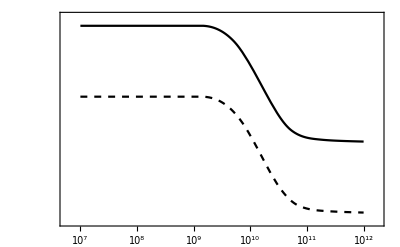

```mathematica
LogLogPlot[{a4ρνCQED[aC[Tv]],a4ρνCNoQED[aC[Tv]]},{Tv,Ti,Tf},Frame->True,PlotStyle->{Black,{Dashed,Black}}]
```

We gather all operations needed to compute incomplete neutrino decoupling. Hence the function RecomputeIncompleteNeutrinoDecoupling can be called whenever we change some parameters so as to modify the incomplete decoupling of neutrinos.

```mathematica
RecomputeIncompleteNeutrinoDecoupling:=(
SolveaOFTwhenID;
InvertaofTwhenID;
SolveρνOFawhenID;
)
```

## Neutrino Temperature

We extract the corresponding temperature of  neutrinos

For decoupling it is easy and deduced from entropy conservation

We choose the correct temperature ratio depending on options chosen and we build the corresponding energy density

```mathematica
TνoverTDecoupling[T_]:=(FourOverEleven DST[T])^(1/3);
ρνDecoupling[Tv_]:=aBB(kB TνoverTDecoupling[Tv]Tv)^4 7/8 Nneu;
```

When considering incomplete decoupling of neutrinos, we find the temperature variation, which is defined as a brightness temperature. See Eq. 64 of companion paper.

```mathematica
TνoverTIncompleteDecouplingQED[Tv_]:=(ρνCQED[aCQED[Tv]]/(aBB(kB Tv)^4 7/8 Nneu))^(1/4);
TνoverTIncompleteDecouplingNoQED[Tv_]:=(ρνCNoQED[aCNoQED[Tv]]/(aBB(kB Tv)^4 7/8 Nneu))^(1/4);

TνoverTIncompleteDecoupling[T_]:=If[$QEDPlasmaCorrections,TνoverTIncompleteDecouplingQED[T],TνoverTIncompleteDecouplingNoQED[T]]
```

So that now we can decide to use either the full decoupling or the incomplete decoupling neutrino temperature, depending on the options chosen

```mathematica
If[$IncompleteNeutrinoDecoupling,
TνoverT[Tv_]:=TνoverTIncompleteDecoupling[Tv];,
TνoverT[Tv_]:=TνoverTDecoupling[Tv];];
```

## Effective Description of Neutrinos

We check the translation into equivalent number of neutrinos. See section II.G of companion paper for the definition of Neff.

```mathematica
TνoverTDecouplingNoQED[T_]:=(FourOverElevenNoQED* DSTNoQED[T])^(1/3);
TνoverTDecouplingQED[T_]:=(FourOverElevenQED* DSTQED[T])^(1/3);

EffectiveNeutrinosQED[Tv_]:=3(TνoverTIncompleteDecouplingQED[Tv]/TνoverTDecouplingNoQED[Tv])^4;
EffectiveNeutrinosNoQED[Tv_]:=3(TνoverTIncompleteDecouplingNoQED[Tv]/TνoverTDecouplingNoQED[Tv])^4;
```

z (z is defined as z=aT with the convention z=1 deep before BBN).

```mathematica
zOFTDecouplingNoQED[T_]:=(DSTNoQED[Ti]/DSTNoQED[T])^(1/3);
zOFTDecouplingQED[T_]:=(DSTQED[Ti]/DSTQED[T])^(1/3);

zOFTIncompleteDecouplingNoQED[T_]:=(aCNoQED[T]T)/(aCNoQED[Ti]Ti);
zOFTIncompleteDecouplingQED[T_]:=(aCQED[T]T)/(aCQED[Ti]Ti);
```

The various z at the end depending on the physics. See table I in companion paper.

```mathematica
zendQED=zOFTIncompleteDecouplingQED[Tf]
zendNoQED=zOFTIncompleteDecouplingNoQED[Tf]

zendDecouplingQED=zOFTDecouplingQED[Tf]
zendDecouplingNoQED=zOFTDecouplingNoQED[Tf]
(11./4)^(1/3)
```

1.39788

1.39911

1.39978

1.40102

1.40102

Effective number of neutrinos

```mathematica
EffectiveNeutrinosQED[10^8]
EffectiveNeutrinosNoQED[10^8]
3((11./4)^(1/3)/zendDecouplingQED)^4
```

3.0445

3.0338

3.0106

z_ν at the end of integration (Only computed in the case of incomplete decoupling because otherwise it remains unity)

```mathematica
zνOFTQED[T_]:=TνoverTIncompleteDecouplingQED[T]*zOFTIncompleteDecouplingQED[T];
zνOFTNoQED[T_]:=TνoverTIncompleteDecouplingNoQED[T]*zOFTIncompleteDecouplingNoQED[T];
zνOFT[T_]:=If[$QEDPlasmaCorrections,zνOFTQED[T],zνOFTNoQED[T]]
```

```mathematica
zνendQED=zνOFTQED[10^8]
zνendNoQED=zνOFTNoQED[10^8]
```

1.00144

1.00144

The total energy density increase in neutrinos is

```mathematica
zνendQED^4
zνendNoQED^4
```

1.00577

1.00577

N_eff is by definition (z_ν z_dec/z)^4. See notation in companion paper.
So we recheck that we find the N_eff given in the companion paper in Table I.

```mathematica
3*(zνendQED *zendDecouplingNoQED/zendQED)^4
3*(zνendNoQED *zendDecouplingNoQED/zendNoQED)^4
3*(zendDecouplingNoQED/zendDecouplingQED)^4
```

3.04449

3.03379

3.01059

```mathematica
If[$PaperPlots,ListLogLinearPlot[Table[{Tv,TνoverTIncompleteDecouplingQED[Tv]/TνoverTDecouplingQED[Tv]},{Tv,ListTRange[10^8,10^12]}],Joined->True,PlotStyle->Black,FrameStyle->Thickness[0.004],Frame->True,FrameLabel->{"T(K)","T_ν^ID / T_ν^dec"}]]
If[$PaperPlots,Export["Plots/PlotTnuvariation.pdf",Style[%,Magnification->1],"PDF"];]

If[$PaperPlots,ListLogLinearPlot[Table[{Tv,TνoverT[Tv]},{Tv,ListTRange[10^8,10^12]}],Joined->True,PlotStyle->Black,FrameStyle->Thickness[0.004],Frame->True,FrameLabel->{"T(K)","T_ν^ID / T_ν^dec"}]]
If[$PaperPlots,Export["Plots/PlotTnuOverT.pdf",Style[%,Magnification->1],"PDF"];]
```

```mathematica
If[$PaperPlots,ListLogLinearPlot[{Table[{Tv,EffectiveNeutrinosQED[Tv]},{Tv,ListTRange[10^8,10^12]}],
Table[{Tv,EffectiveNeutrinosNoQED[Tv]},{Tv,ListTRange[10^8,10^12]}],
Table[{Tv,3(zOFTDecouplingNoQED[Tv]/zOFTDecouplingQED[Tv])^4},{Tv,ListTRange[10^8,10^12]}](*,
Table[{Tv,3(zνOFT[Tv])^4},{Tv,ListTRange[10^8,10^12]}]*)},Joined->True,PlotStyle->{Black,{Red,Dashed},{Blue,Dotted}},Frame->True,FrameLabel->{"T(K)","N_eff"},LabelStyle->{FontSize->12},FrameStyle->Thickness[0.004],PlotRange->{2.99,3.05}]]
If[$PaperPlots,Export["Plots/PlotNeff.pdf",Style[%,Magnification->1],"PDF"];]
```

## Scale factor determination

If neutrino decoupling is total, then the total entropy is conserved and so it is only a function of temperature (entropy density) and scale factor (volume), since S= s a^3.
So this can be solved without a differential equation in time. If neutrinos would still be interacting, they would exchange energy and this would violate entropy conservation, so entropy density would be sourced and it would require to solve the evolution in time of the entropy (see section above).

This is the function which gives the scale factor as a function of the temperature. If Incomplete Neutrino decoupling is taken into account, we use the result aC previously obtained.

```mathematica
If[$IncompleteNeutrinoDecoupling,
a[T_]:=aC[T],
a[T_]:=TCMB0/(T DST[T]^(1/3))];
```

```mathematica
(*LogLinearPlot[{a[Tv], TCMB0/Tv},{Tv,10^9,10^10},Frame->True,FrameLabel->{"T (K)","a(T)/a_0     T_CMB0/T_CMB"}]*)
```

Just for simplicity we define again the z and z_ν variables which are z=aT and z=aT_ν respectively

```mathematica
zT[T_]:=(a[T]T)/(a[Ti]Ti);
znuT[T_]:=(a[T]TνoverT[T] T)/(a[Ti]TνoverT[Ti] Ti);
```

And again we check how they varied

```mathematica
zT[Tf]//NP
znuT[Tf]//NP
```

1.3978799

1.0014382

We build a table with (a, T) so as to obtain the inverse T(a) via an interpolation. 
In the incomplete neutrino case we have already performed such inversion so there is a slight loss of time and computer energy.

```mathematica
InvertaOFT:=(Tofa=Interpolation@Table[{a[T],T},{T,ListT}];);
(*aI=Interpolation@Table[{T,a[T]},{T,ListT}];*)
```

```mathematica
InvertaOFT
```

We can check how accurate is this inversion by checking how a(T(a)) is the identity. The error is below 10^-8 so our numerics are precise enough.

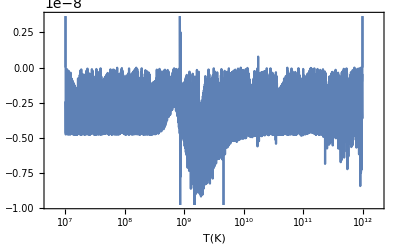

```mathematica
LogLinearPlot[{Tofa[a[T]]/T-1},{T,Ti,Tf},Frame->True,FrameLabel->{"T(K)",""}]
```

η factor with temperature dependence (because photons density has evolved due to electron positron recombination)

```mathematica
ηfactorT[Tv_]:=nB[a[Tv]]*π^2/(2Zeta[3])((hbar clight)/(kB Tv))^3;
```

Another way to  obtain this quantity

```mathematica
ηfactorTBis[Tv_]:=ηfactor*(zT[Tf]/zT[Tv])^3;
```

```mathematica
ηfactorTBis[Ti]//NP
ηfactorT[Ti]//NP
```

1.6638777×10^-9

1.6638777×10^-9

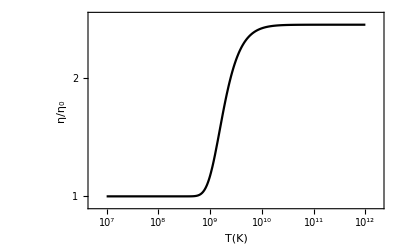

```mathematica
LogLogPlot[ηfactorT[Tv]/ηfactor,{Tv,Ti,Tf},Frame->True,FrameStyle->Thickness[0.004],PlotStyle->Black,FrameLabel->{"T(K)","η/η_0"}]
If[$PaperPlots,Export["Plots/PlotEta.pdf",Style[%,Magnification->1],"PDF"];]
```

Check of normalization. We chose that today the scale factor is unity.

```mathematica
a[Tf]Tf/TCMB0//NP
```

1.

## Weak reactions n+ν ↔ p+e

## Distribution functions derivatives

These Fermi-Dirac function and its derivatives are needed further. en stands for energy. x for 1/(k_B T). 

FDeipj means that it is the Fermi Dirac distribution multiplied by Energy^i and derived j times wrt to Energy. See Def B25 in companion paper.

```mathematica
FDe2p0[en_,x_]=Simplify[FD[en,x]en^2];
FDe3p0[en_,x_]=Simplify[FD[en,x]en^3];
FDe2p2[en_,x_]=Simplify@D[D[FD[en,x]en^2,en],en];

FDe3p2[en_,x_]=Simplify@D[D[FD[en,x]en^3,en],en];
FDe4p2[en_,x_]=Simplify@D[D[FD[en,x]en^4,en],en];
FDe2p1[en_,x_]=Simplify@D[FD[en,x]en^2,en];
FDe3p1[en_,x_]=Simplify@D[FD[en,x]en^3,en];
FDe4p1[en_,x_]=Simplify@D[FD[en,x]en^4,en];
```

```mathematica
FDνe2p0[en_,ϕ_,x_]=Simplify[FDν[en,ϕ,x]en^2];
FDνe3p0[en_,ϕ_,x_]=Simplify[FDν[en,ϕ,x]en^3];
FDνe2p2[en_,ϕ_,x_]=Simplify@D[D[FDν[en,ϕ,x]en^2,en],en];

FDνe3p2[en_,ϕ_,x_]=Simplify@D[D[FDν[en,ϕ,x]en^3,en],en];
FDνe4p2[en_,ϕ_,x_]=Simplify@D[D[FDν[en,ϕ,x]en^4,en],en];
FDνe2p1[en_,ϕ_,x_]=Simplify@D[FDν[en,ϕ,x]en^2,en];
FDνe3p1[en_,ϕ_,x_]=Simplify@D[FDν[en,ϕ,x]en^3,en];
FDνe4p1[en_,ϕ_,x_]=Simplify@D[FDν[en,ϕ,x]en^4,en];
```

## λ_0

### Born approximation λ_0

See e.g. Eq. 13 of [Lopez & Turner 1998]. Or Eq. 92 of companion paper.

The constant λ_0 is a proxy for  τ_n^-1= λ_0* [cos^2(θ_c)G_F^2(C_V^2+3 C_A^2)/(2 π^3) ]

```mathematica
λBORN=With[{q=Q/me},NIntegrate[en(en-q)^2 √(en^2-1),{en,1,q}]]
```

1.63609

### Corrections to λ_0

#### Radiative corrections to λ_0

1) If $ResummedLogsRadiativeCorrections=False, we use Eq. 7 of  [Czarnecki et al. 2004] which is B30 of companion paper.
 Combined with Eq 20b of [Sirlin 1967] for Sirlin’s universal function, that is Eq. B32 in companion paper.

```mathematica
AgCzarnecki=-0.34;
CCzarnecki=0.891;
mA=1.2 GeV;
ConstantSirlin =4Log[Subscript[m, Z]/mp]+Log[mp/mA]+2CCzarnecki+AgCzarnecki;
```

For information, this quantity is evaluated to 40 in [Dicus et al.]

```mathematica
ConstantSirlin+3Log[mp/(me)]-3/4
```

41.2988

```mathematica
Rd[x_]:=ArcTanh[x]/x;
```

NB : ArcTanh[x] = 1/2 Log[(1+x)/(1-x)]

```mathematica
Lfun[x_]=Integrate[Log[1-t]/t,{t,0,x},Assumptions->x<1&&x>0](* Lfun is called the Spence function *)
```

-PolyLog[2,x]

It can be computed from a Taylor expansion (this used to be done in the past), but a direct evaluation by Mathematica is much better

```mathematica
LfunSeries[b_]=Normal@Series[-1/4*(1+b)^6*4/b Lfun[(2b)/(1+b)],{b,0,12(*22*)}]
```

2+11 b+(224 b^2)/9+(89 b^3)/3+(1496 b^4)/75+(596 b^5)/75+(128 b^6)/49+(68 b^7)/49+(3704 b^8)/3969+(21988 b^9)/33075+(2016208 b^10)/4002075+(946628 b^11)/2401245+(43024472 b^12)/135270135

Sirlin universal function (Eq 20b of [Sirlin 1967]) on which we add the constants of Eq. 7 of  [Czarnecki et al. 2004]) is obtained as (this is B32 of companion paper)

```mathematica
$SeriesSpenceFunction=False;

SirlinGFunction[b_,y_,en_]:=(3Log[mp/(me)]-3/4+4(Rd[b]-1)(y/(3 en)-3/2+Log[2y])+Rd[b](2(1+b^2)+y^2/(6 en^2)-4 b Rd[b])+If[$SeriesSpenceFunction,-4/(1+b)^6*LfunSeries[b],4/b Lfun[(2b)/(1+b)]]);
Cd[b_,y_,en_]:=(ConstantSirlin+SirlinGFunction[b,y,en]);
```

NB : In [Dicus et al. 1982] Eq 2.14 (or in [Lopez&Turner 1998] Eq. 17) they use the approximation  4/b Lfun[(2b)/(1+b)]= -4(2+11b+224/9 b^2+89/3 b^3+1496/75 b^4+596/75 b^5+128/49 b^6)/(1+b)^6  
However there is a typo and some incorrect coefficients. In [Kernan] there are approximate coefficients which are nearly correct.

2) if $ResummedLogsRadiativeCorrections = True, we use a resummed version of all the Log[m_Z/m_P]. It consists in using Eq. 15 of [Czarnecki 2004] or B35 in companion paper.
See also [Esposito et al. 1998])

We build the multiplicative factor for inner radiative corrections (Eq. 15 of [Czarnecki et al. 2004]), that is B35 of companion paper.

```mathematica
LFactor=1.02094;
SFactor=1.02248;
δfactor=-0.00043*2Pi/αFS;
NLL=-0.0001;
```

```mathematica
RadiativeCorrectionsResummed[b_,y_,en_]:=(1+αFS/(2π)(SirlinGFunction[b,y,en]-3Log[mp/(2Q)]))*
(LFactor+αFS/π CCzarnecki+αFS/(2π)δfactor)*(SFactor+1/(134*2*Pi)*(Log[mp/mA]+AgCzarnecki)+NLL);
```

Finally we define a function which selects either choice depending on option

```mathematica
RadiativeCorrections[b_,y_,en_]:=If[$ResummedLogsRadiativeCorrections,RadiativeCorrectionsResummed[b,y,en],(1+αFS/(2π)Cd[b,y,en])]
```

Fermi function for Coulomb interactions of electron and proton (if on the same side of the interaction).
Either the relativistic or the non-relativistic depending on option $RelativisticFermiFunction. That is either Eq. 99 or Eq. 100 of companion paper depending on option chosen.

```mathematica
FermiRelat[b_]:=With[{γ=Sqrt[1-αFS^2]-1,λCompton=1/(me/(hbar clight))},
(1+γ/2)*4((2radiusproton b)/λCompton)^(2γ)*1/Gamma[3+2γ]^2 Exp[(π αFS)/b]*1/((1-b^2)^γ)Abs[Gamma[1+γ+I αFS/b]]^2];

FermiNonRelat[b_]:=(2π αFS/b)/(1-Exp[-2π αFS/b]);
```

```mathematica
If[$RelativisticFermiFunction,

Fermi[b_]:=FermiRelat[b];
bFermi[b_]:=b Fermi[b];,

Fermi[b_]:=FermiNonRelat[b];
bFermi[b_]:=(2π αFS)/(1-Exp[-2π αFS/b]);]
```

```mathematica
If[$PaperPlots,DFermi=Plot[{100*(FermiRelat[b]/FermiNonRelat[b]-1)},{b,0,1},Frame->True,FrameStyle->Thickness[0.004],PlotStyle->{Black},FrameLabel->{"x","100 x (F^rel(x)/F^(non rel)(x) -1)"},LabelStyle->{FontSize->12}]]
If[$PaperPlots,Export["Plots/PlotDeltaFermi.pdf",Style[DFermi,Magnification->1],"PDF"];];
```

λ_0 when taking only Fermi function and not radiative corrections

```mathematica
λFermiOnly=With[{q=Q/me ,b=√(en^2-1)/en,y=Q/me -en},
NIntegrate[en(en-q)^2 en*bFermi[b],{en,1.0000001,q}]]
```

1.69233

This already a 3.44 % correction

```mathematica
λFermiOnly/(λBORN)
```

1.03438

Adding the inner radiative corrections, the constant involved in the decay of the neutron is

```mathematica
λRad=With[{q=Q/me ,b=√(en^2-1)/en,y=Q/me -en},
NIntegrate[en(en-q)^2 en(RadiativeCorrections[b,y,en])*bFermi[b],{en,1.0000001,q}]]
```

1.75837

Note that in companion paper, Eq. 106, the value 1.75767 is quoted when it should be the value found here 1.758373.

This adds another 3.90 % correction as found in Eq 16 of [Czarnecki et al. 2004].

```mathematica
λRad/λFermiOnly
```

1.03903

#### Finite mass corrections to λ_0

See companion papers for expression of finite nucleon mass corrections. 
We take the general form of finite mass correction and remove all terms which involve temperature. So we consider Eq. 118 of companion paper.

```mathematica
IntegrateCorrectionNeutronDecay[fun_]:=
NIntegrate[fun[pe],{pe,0.0000001,√((Q/me)^2-1)},WorkingPrecision->MachinePrecision];
```

```mathematica
χFMNeutronDecay[en_,pe_]:=
With[{M=mp/me,enu=en-Q/me,f1=((1+gA)^2+4 fWM gA)/(1+3 gA^2),f2=((1-gA)^2-4fWM gA)/(1+3 gA^2),f3=(gA^2-1)/(1+3 gA^2)},
 f1*enu^2(pe^2/(M*en))
+f2*enu^3(-1/M)
+ (f1+f2+f3)1/(2M)*(4 enu^3+2enu pe^2)
+f3*1/(3M)3 enu^2 pe^2/(en)
];
```

Without coupling to radiative corrections we get

```mathematica
IλFMBasic[pe_]:=With[{en=Sqrt[pe^2+1]},With[{b=pe/en},pe^2*
(χFMNeutronDecay[en,pe])
]];
```

```mathematica
IntegrateCorrectionNeutronDecay[IλFMBasic]/λBORN
```

-0.00206763

However we couple to radiative corrections if $CoupledFMandRC = True

```mathematica
IλFM[pe_]:=With[{en=√(pe^2+1)},With[{b=pe/en},pe^2*
(χFMNeutronDecay[en,pe]*If[$RadiativeCorrections&&$CoupledFMandRC,(RadiativeCorrections[b,Abs[en- Q/me ],en])Fermi[b],1])
]];
```

```mathematica
λFM=If[$FiniteNucleonMass,IntegrateCorrectionNeutronDecay[IλFM],0]
```

-0.00363334

When taking only into account Fermi function and finite mass effect on should get 1.6887. See Eq. 6 of [Czarnecki et al. 2004]

```mathematica
λFermiOnly+λFM
1.6887/%//NP
```

1.6887

1.0000023

We compare the correction to the Born result

```mathematica
CorrectionRate=λFM/λBORN
```

-0.00222075

If Coulomb and Radiative corrections are set to False (0) this is exactly (-0.00206) what is found by [Lopez & Turner 1997] (see three lines after Eq. 23, in the text). 
See also the value -0.00201 found in Eq. 20 of [Seckel 1993].

We also reproduce for comparison the exact finite mass correction to the neutron decay rate as computed by Eq. 19 of [Lopez & Turner 1998], which uses two-dimensional integrals. Again we find the -0.00206 correction so our finite mass method based one-dimensional integrals is reliable.

```mathematica
λexact=With[{pe=Sqrt[en^2-1]},With[{enu=((mn^2-mp^2)/me^2+1-2mn/me en)/(2(mn/me-en+pe Cnu))},
With[{Ep=mn/me-enu-en,f1=((1+gA)^2+4fWM gA)/(1+3 gA^2),f2=((1-gA)^2-4fWM gA)/(1+3 gA^2),f3=(gA^2-1)/(1+3 gA^2)},With[{J=1+(enu+ pe Cnu)/(Ep),M2=f1 mn/me enu (Ep en-(-pe^2-pe enu Cnu))+f2 mn/me en (Ep enu-(-pe enu Cnu-enu^2))+f3 mn/me  Ep(enu en-Cnu enu pe) },NIntegrate[1/2*M2 pe enu/(mn/me  Ep J),{en,1,(Q-(Q^2-me^2)/(2mn))/me },{Cnu,-1,1},PrecisionGoal->10(*,Method->{Automatic,"SymbolicProcessing"->0}*)]
]]]];
```

```mathematica
(λexact-λBORN)/λBORN//NP
```

-0.0020636766

#### Total correction

The total correction for the neutron decay constant λ_0 is the sum of the Radiative corrected one plus the finite mass effects

We recall the result from radiative corrections (again we stress that Eq. 106 in companion paper should report that value).

```mathematica
λRad
```

1.75837

The result from mass corrections (see text before  Eq. 120 in companion paper.)

```mathematica
λFM
```

-0.00363334

And we sum them to get Eq. 120 of companion paper.

```mathematica
λRadandFM=λRad+λFM
```

1.75474

This gives a total correction which is

```mathematica
λRadandFM/λBORN
```

1.07252

If we compare with [Cooper et al 2010] (Phys. Rev. C 81, 035503 (2010)). They find that this parameter should be

```mathematica
λCooper=1.03887*1.6887
λCzarnecki=1.0390*1.6887 (* = (1+RC)*f with f=1.6887 and RC = 0.0390(8) [Czarnecki et al. 2004]] *)
```

1.75434

1.75456

We compute the ratio to see how far we are

```mathematica
λRadandFM/λCooper
λRadandFM/λCzarnecki
```

1.00023

1.0001

We check that it is in agreement with the theoretical formula. This expression below should reproduce the neutron decay time. It is amazingly close !

```mathematica
MixingCosAngle=0.97420;(* (+-16) Value taken from CKM particle data group 2017. More precisely from the review on Vud Vus of the PDG 2017.*)
MyK=MixingCosAngle^2(GF)^2(1+3(gA)^2)/(2 π^3)*(me )^5 /hbar
1/MyK/λRadandFM
1/MyK/λCzarnecki
1/MyK/λCooper
```

0.00064543

882.955

883.045

883.156

We recall the neutron lifetime.

```mathematica
τneutron
```

879.5

We see that we are extremely close but still not quite satisfactory. 
Actually this would work much better if we used the post-2000 average for g_A which is 1.2755(11) (Marciano, private communication).

```mathematica
gAbetter=1.2755;
MyKbetter=MixingCosAngle^2(GF)^2(1+3(gAbetter)^2)/(2 π^3)*(me )^5 /hbar

1/MyKbetter/λRadandFM
1/MyKbetter/λCzarnecki
1/MyKbetter/λCooper
```

0.000648125

879.282

879.373

879.483

Let us also compare with Eq. 17 of [Czarnecki et al. 2004] to check how close we are in including all corrections. See text after Eq. 120 in companion paper as well.

```mathematica
ConstantVud=hbar*(2 π^3)/(me)^5/(GF)^2/λRadandFM
ConstantVud2=hbar*(2 π^3)/(me )^5/(GF)^2/λCzarnecki
ConstantVud3=hbar*(2 π^3)/(me )^5/(GF)^2/λCooper
```

4907.42

4907.93

4908.54

## Born rates

We compute in this section the Born rates for n -> p and p -> n.

Tools to perform integration on electron momentum

```mathematica
pemin=0.00001;
pemiddle[x_]:=Sqrt[Max[pemin^2,(Q/me )^2-1 -If[$QEDMassShift,dme2x[x],0]]];
pemaxC[x_]:=Max[7,30/x];
pemax[x_]:=Max[7,30/x];
```

$TnuEqualT is some cheat to check detailed balance. Should be False. When it is True neutrinos have always the plasma temperature.

```mathematica
$TnuEqualT=False;
```

```mathematica
IntegratedpNpoints[fun_,sgnq_,Tv_,Npoints_]:=With[{x=me/(kB Tv) ,znu=me/(kB Tv TνoverT[Tv]) },
If[$FastPENRatesIntegrals,
IntegrateFunction[fun[#,x,If[$TnuEqualT,x,znu],sgnq]&,pemin,pemaxC[x],Npoints],
NIntegrate[fun[pe,x,If[$TnuEqualT,x,znu],sgnq],{pe,pemin,pemiddle[x],pemax[x]}]
]]

IntegrateRatedp[fun_,sgnq_,Tv_]:=IntegratedpNpoints[fun,sgnq,Tv,$PENRatesIntegralsPoints];
```

Energy as a function of momentum, taking into account QED mass shifts. 
This is only used if the option is set to True but it is useless because it is taken into account in finite temperature corrections

```mathematica
enOFpe[pe_,x_]:=Sqrt[pe^2+1 +If[$QEDMassShift,dme2x[x],0]];
```

Functions to build integrands in electron momentum. Without and with CCR corrections. This is then passed to the integrating routine IntegrateRatedp.

```mathematica
IPENdpFromχNoCCR[en_,pe_,x_,znu_,sgnq_,χfunction_]:=With[{q=Q/me },With[{b=pe/en},
pe^2*(χfunction[en,pe,x,znu,sgnq]+χfunction[-en,pe,x,znu,sgnq])
]];
```

```mathematica
Fermi[sgnq_,signE_,b_?NumericQ]:=If[sgnq signE >0,Fermi[b],1];
SetAttributes[Fermi,Listable];
```

```mathematica
IPENdpFromχCCR[en_,pe_,x_,znu_,sgnq_,χfunction_]:=With[{q=Q/me ,b=pe/en},
pe^2*(χfunction[en,pe,x,znu,sgnq](RadiativeCorrections[b,Abs[sgnq Q/me-en],en])Fermi[sgnq,1,b]+χfunction[-en,pe,x,znu,sgnq](RadiativeCorrections[b, Abs[sgnq Q/me+en],en])Fermi[sgnq,-1,b])
];
```

Eq 2.29 in [Brown & Sawyer] for the Born approximation. It is Eq. 79 of companion paper

```mathematica
χ[en_,pe_,x_,znu_,sgnq_]:=With[{q=Q/me },FDν[en-sgnq q,sgnq ξν,znu]FD[-en,x](en-sgnq q)^2];
```

Eq 2.30 in [Brown & Sawyer], that is the integration of Eq. 78 in companion paper

```mathematica
IPENdp[pe_,x_,znu_,sgnq_]:=IPENdpFromχNoCCR[enOFpe[pe,x],pe,x,If[$TnuEqualT,x,znu],sgnq,χ]
```

We also define a function which is incorrect in which we force the neutrinos to have the temperature of photons. This is to check detailed balance. Indeed, detailed balance is satisfied only if all species have the same temperature.

```mathematica
IPENdpCheatNeutrinoTemperature[pe_,x_,znu_,sgnq_]:=IPENdpFromχNoCCR[Sqrt[pe^2+1],pe,x,x,sgnq,χ]
```

Born rates are given by Eq 2.30 in [Brown & Sawyer].

```mathematica
λnTOpBORN[Tv_]:=IntegrateRatedp[IPENdp,1,Tv];
λpTOnBORN[Tv_]:=IntegrateRatedp[IPENdp,-1,Tv];
```

```mathematica
λnTOpBORNCheatNeutrino[10^7]
```

λnTOpBORNCheatNeutrino[10000000]

Born rates where the neutrino temperature is cheated to be equal to photons temperature are then given by

```mathematica
λnTOpBORNCheatNeutrino[Tv_]:=IntegrateRatedp[IPENdpCheatNeutrinoTemperature,1,Tv];
λpTOnBORNCheatNeutrino[Tv_]:=IntegrateRatedp[IPENdpCheatNeutrinoTemperature,-1,Tv];
```

## Finite mass effects

For finite mass effects, we use a (Fokker-Planck) expansion which leads to one-dimensional integrals.
We include also the weak-magnetism which is important indeed. This is B23 of companion paper.

```mathematica
χFM[en_,pe_,x_,znu_,sgnq_]:=
With[{ϕ=sgnq ξν,q=Q/me ,M=(mp+mn -sgnq Q)/(2me ),Mp=mp/me ,Mn=mn /me ,enu=en-sgnq Q/me,
f1=((1+sgnq gA)^2+4fWM sgnq gA)/(1+3 gA^2),
f2=((1-sgnq gA)^2-4fWM sgnq gA)/(1+3 gA^2),f3=(gA^2-1)/(1+3 gA^2)},
f1*FDνe2p0[enu,ϕ,znu]FD[-en,x](pe^2/(M*en))
+f2*FDνe3p0[enu,ϕ,znu]FD[-en,x](-1/M)
+(f1+f2+f3)1/(2x M)*(FDνe4p2[enu,ϕ,znu]FD[-en,x]+FDνe2p2[enu,ϕ,znu]FD[-en,x] pe^2)
+(f1+f2+f3)1/(2M)*(FDνe4p1[enu,ϕ,znu]FD[-en,x]+FDνe2p1[enu,ϕ,znu]FD[-en,x] pe^2)
-(f1+f2)1/(x M)*(FDνe3p1[enu,ϕ,znu]FD[-en,x]+FDνe2p1[enu,ϕ,znu]FD[-en,x]pe^2/(-en))
-f3*3/(x M)FDνe2p0[enu,ϕ,znu]FD[-en,x](* This term seems to give very small corrections *)
+f3*1/(3M)FDνe3p1[enu,ϕ,znu]FD[-en,x] pe^2/(en)
+f3*2/(2 x*3M)FDνe3p2[enu,ϕ,znu]FD[-en,x] pe^2/(en)
-(f1+f2+f3)*3/(2x)*(1-(Mn/Mp)^sgnq)*(FDνe2p1[enu,ϕ,znu]FD[-en,x])
];
```

Integrand for finite mass corrections. We couple it to radiative corrections.

```mathematica
IPENdpFMNoCCR[pe_,x_,znu_,sgnq_]:=IPENdpFromχNoCCR[enOFpe[pe,x],pe,x,If[$TnuEqualT,x,znu],sgnq,χFM]
IPENdpFMCCR[pe_,x_,znu_,sgnq_]:=IPENdpFromχCCR[enOFpe[pe,x],pe,x,If[$TnuEqualT,x,znu],sgnq,χFM]
```

Integrand for finite mass corrections when neutrinos are forced to have the same temperature as photons.

```mathematica
IPENdpFMCheatNeutrinoTemperature[pe_,x_,znu_,sgnq_]:=IPENdpFromχNoCCR[enOFpe[pe,x],pe,x,x,sgnq,χFM]
```

```mathematica
Clear[λnTOpFMCCR,λpTOnFMCCR,λnTOpFMNoCCR,λpTOnFMNoCCR,λnTOpCheatNeutrinoFM,λpTOnCheatNeutrinoFM]
```

Finite mass corrections using the λ_0 which is corrected with radiative corrections. The computation below implements Eqs. 114 of companion paper.

```mathematica
λnTOpFMCCR[Tv_]:=IntegrateRatedp[IPENdpFMCCR,1,Tv];
λpTOnFMCCR[Tv_]:=IntegrateRatedp[IPENdpFMCCR,-1,Tv];
```

Finite mass corrections using the λ_0 which is computed with the Born infinite mass expression (we do not advise to use it).

```mathematica
λnTOpFMNoCCR[Tv_]:=IntegrateRatedp[IPENdpFMNoCCR,1,Tv];
λpTOnFMNoCCR[Tv_]:=IntegrateRatedp[IPENdpFMNoCCR,-1,Tv];
```

Finite mass corrections cheating with the neutrino temperature and setting it equal to photons temperature

```mathematica
λnTOpCheatNeutrinoFM[Tv_]:=IntegrateRatedp[IPENdpFMCheatNeutrinoTemperature,1,Tv];
λpTOnCheatNeutrinoFM[Tv_]:=IntegrateRatedp[IPENdpFMCheatNeutrinoTemperature,-1,Tv];
```

Examples of neutron decay corrections for some low temperatures:

```mathematica
λnTOpFMCCR[10^8]/λnTOpBORN[10^8]//Timing
λnTOpFMCCR[10^7.5]/λnTOpBORN[10^7.5]//Timing
```

{0.059885,-0.00223575}

{0.20587,-0.00222606}

```mathematica
λnTOpFMCCR[.8 10^10]/λnTOpBORN[.8 10^10]//Timing
λnTOpFMCCR[10^10]/λnTOpBORN[10^10]//Timing
λnTOpFMCCR[10^10.5]/λnTOpBORN[10^10.5]//Timing
(*λpTOnFMCCR[.8 10^10]/λpTOnBORN[.8 10^10]//Timing
λpTOnFMCCR[10^10]/λpTOnBORN[10^10]//Timing
λpTOnFMCCR[10^10.5]/λpTOnBORN[10^10.5]//Timing*)
```

{0.032178,-0.00915005}

{0.033562,-0.010912}

{0.031452,-0.0305252}

### Plots of the finite mass corrections

We plot the amplitude of the finite mass corrections. This is essentially similar to Fig 8.1 of [Kernan] but the result is a little different since here we have put all the finite nucleon mass effects, and [Kernan] did not.

```mathematica
If[$PaperPlots,
TabδλFMnTOp=Table[{T,(λnTOpFMCCR[T]*(τneutron λRadandFM)^-1)/(λnTOpBORN[T]*(τneutron λBORN)^-1)},{T,ListTRange[10^9,10^11]}];
TabδλFMpTOn=Table[{T,(λpTOnFMCCR[T]*(τneutron λRadandFM)^-1)/(λpTOnBORN[T]*(τneutron λBORN)^-1)},{T,ListTRange[10^9,10^11]}];

TFreeze=0.8 MeV/kB;

PlotdeltaGammaFM=Show[ListLogLinearPlot[{TabδλFMnTOp,TabδλFMpTOn},Frame->True,FrameStyle->Thickness[0.004],Joined->True,PlotRange->{-10^-1,10^-2},FrameLabel->{"T (K)","δΓ/Γ"},LabelStyle->{FontSize->12},PlotStyle->{{Black,Thickness[0.003]},{Black,Dashing[{0.01}],Thickness[0.003]}},GridLines->{{{TFreeze,{Gray,Thickness[0.005]}}},{}},FrameTicks->MyFrameTicksLog],
Graphics[{Rotate[Text[Style["0.8 MeV",FontSize->10,Black],{Log@TFreeze-.1,-0.06}],90 Degree]}]]
]
If[$PaperPlots,Export["Plots/PlotdeltaGammaFM.pdf",Style[PlotdeltaGammaFM,Magnification->1],"PDF"];];
```

```mathematica
If[$PaperPlots,TabδλFMnTOp2=Table[{T,Identity[(λnTOpFMCCR[T]*(τneutron λRadandFM)^-1)/(λnTOpBORN[T]*(τneutron λBORN)^-1)]},{T,ListTRange[5 10^8,10^10.5]}];
TabδλFMpTOn2=Table[{T,Identity[(λpTOnFMCCR[T]*(τneutron λRadandFM)^-1)/(λpTOnBORN[T]*(τneutron λBORN)^-1)]},{T,ListTRange[5 10^8,10^10.5]}];

PlotdeltaGammaFM2=Show[ListPlot[{TabδλFMnTOp2,TabδλFMpTOn2},Frame->True,FrameStyle->Thickness[0.004],Joined->True,PlotRange->{-3*10^-2,10^-2},FrameLabel->{"T (10^10K)","δΓ/Γ"},LabelStyle->{FontSize->12},PlotStyle->{{Red,Thickness[0.003]},{Blue,Dashing[{0.01}],Thickness[0.003]}},FrameTicks->{{Automatic,Automatic},{{{0.5*10^10,".5"},{10^10,"1"},{1.5*10^10,"1.5"},{2 10^10,"2"},{2.5 10^10,"2.5"}},Automatic}},GridLines->{{{TFreeze,{Gray,Thickness[0.005]}}},{}}],
Graphics[{Rotate[Text[Style["0.8 MeV",FontSize->10,Black],{TFreeze 0.93,-0.02}],90 Degree]}]]
]

If[$PaperPlots,Export["Plots/PlotdeltaGammaFM2.pdf",Style[PlotdeltaGammaFM2,Magnification->1],"PDF"];];
```

### Checking detailed balance

Born approximation detailed balance

```mathematica
DetailedBalanceRatio0[T_]:=Exp[-Q/(kB T)-ξν];
```

At Born order, detailed balance is of course satisfied by construction.

```mathematica
DetailedBalance0[T_]:=(λnTOpBORN[T])/(λpTOnBORN[T])*DetailedBalanceRatio0[T];
DetailedBalanceCheatNeutrino0[T_]:=(λnTOpBORNCheatNeutrino[T])/(λpTOnBORNCheatNeutrino[T])*DetailedBalanceRatio0[T];
```

If we enforce T_ν=T the precision is insane. It is numerical precision because detailed balance is rooted in our method.

```mathematica
If[$PaperPlots,
ListLogLinearPlot[{Table[{T,DetailedBalanceCheatNeutrino0[T]-1},{T,ListTRange[10^9,10^12]}]},Joined->True,PlotStyle->{Black,{Black,Dashed}},Frame->True]
]
```

Including corrections in Q/mp,detailed balance is given by (where α should be set to 0).

```mathematica
DetailedBalanceRatio[T_]:=Exp[-Q/(kB T)-ξν](1+(1+α)Q/mp)^(3/2);
```

[Lopez&Turner 1997] define some quantity to parameterize how good detailed balance is obtained, this is the parameter α. 
α should be 0 so we use it to estimate the failure of detailed balance

We first solve for α correctly, and then we do it when forcing the temperature of neutrinos to be the one of photons, in which case detailed balance must be true. Indeed if we do not force the temperature of neutrinos to be the one of photons, then it is only true before electrons/positrons annihilate, and at low temperature detailed balance is not satisfied.

```mathematica
Clear[αLopez,αLopezCheatNeutrino]
αLopez[T_]:=αLopez[T]=α/.Solve[Normal@Series[(λnTOpBORN[T]+λnTOpFMNoCCR[T])/(λpTOnBORN[T]+λpTOnFMNoCCR[T])*DetailedBalanceRatio[T],{α,0,1}]==1,α][[1]]

αLopezCheatNeutrino[T_]:=αLopezCheatNeutrino[T]=α/.Solve[Normal@Series[(λnTOpBORNCheatNeutrino[T]+λnTOpCheatNeutrinoFM[T])/(λpTOnBORNCheatNeutrino[T]+λpTOnCheatNeutrinoFM[T])*DetailedBalanceRatio[T],{α,0,1}]==1,α][[1]]
```

We plot something similar to Fig. 4 of [Lopez&Turner 1997]. The remaining error should come from second order corrections. For instance at low temperature it remains an effect of order  (Q/mn )^2 so α is expected to differ from a null value by something of order Q/mn =0.002. We also see that below 5x10^10 K, detailed balance does not work because neutrinos no longer have the temperature of photons but it works if we force neutrinos to be at the temperature of photons.

```mathematica
If[$PaperPlots,PlotDetailedBalance=Show[ListLogLinearPlot[{Table[{T,αLopez[T]},{T,ListTRange[10^8.5,10^11.5]}],Table[{T,αLopezCheatNeutrino[T]},{T,ListTRange[10^8.5,10^11.5]}]},Frame->True,FrameTicks->MyFrameTicksLog,GridLines->{{{TFreeze,{Gray,Thickness[0.005]}}},{}},Joined->True,FrameLabel->{"T (K)","α"},FrameStyle->Thickness[0.003],LabelStyle->{FontSize->12},PlotRange->{-1,1},PlotStyle->{{Red},{Black,Dashed,Blue}}],
Graphics[{Rotate[Text[Style["0.8 MeV",FontSize->10,Black],{Log@TFreeze-0.2,0.5}],90 Degree]}]]
]

If[$PaperPlots,Export["Plots/PlotDetailedBalance.pdf",Style[PlotDetailedBalance,Magnification->1],"PDF"];];
```

## Radiative Corrections (T=0)

The CCR corrected rates are described in details in the companion paper. 

When electron and protons are on the same side we use the Fermi function to apply the Coulomb corrections.

For all processes the radiative correction are a factor (1+α/(2π)C), (similarly to Eq. 18 of [Lopez&Turner 1998] or Eq. 2.13 of [Dicus .et. al]) as described in companion paper.

```mathematica
IPENdpCCR[pe_,x_,znu_,sgnq_]:=IPENdpFromχCCR[enOFpe[pe,x],pe,x,If[$TnuEqualT,x,znu],sgnq,χ]
```

```mathematica
λnTOpCCR[Tv_]:=IntegrateRatedp[IPENdpCCR,1,Tv];
λpTOnCCR[Tv_]:=IntegrateRatedp[IPENdpCCR,-1,Tv];
```

### Plots of the radiative corrections

```mathematica
If[$PaperPlots,TabδλnTOp=Table[{T,(λnTOpCCR[T]*(τneutron λRadandFM)^-1)/(λnTOpBORN[T](τneutron λBORN)^-1)-1},{T,ListTRange[10^8.5,10^10.5]}];
TabδλpTOn=Table[{T,(λpTOnCCR[T]*(τneutron λRadandFM)^-1)/(λpTOnBORN[T](τneutron λBORN)^-1)-1},{T,ListTRange[10^8.5,10^10.5]}];

PlotdeltaGammaCCR=Show[ListLogLinearPlot[{TabδλnTOp,TabδλpTOn},Frame->True,FrameStyle->Thickness[0.004],Joined->True,FrameLabel->{"T (K)","δΓ/Γ"},LabelStyle->{FontSize->12},PlotStyle->{{Red},{Blue,Dashing[{0.01}]}},GridLines->{{{TFreeze,{Gray,Thickness[0.004]}}},{}},FrameTicks->{{Automatic,Automatic},{{{Log[10^8.5],"10^8.5"},{Log[10^9],"10^9"},{Log[10^9.5],"10^9.5"},{Log[10^10],"10^10"},{Log[10^10.5],"10^10.5"},{Log[10^11],"10^11"}},Automatic}}],
Graphics[{Rotate[Text[Style["0.8 MeV",FontSize->10,Black],{Log@TFreeze-0.1,-0.01}],90 Degree]}]]
]

If[$PaperPlots,Export["Plots/PlotdeltaGammaCCR.pdf",Style[PlotdeltaGammaCCR,Magnification->1],"PDF"];];

(*ListPlot[{TabδλnTOp,TabδλpTOn},Frame->True,Joined->True,FrameLabel->{"T (K)","δΓ/Γ"},PlotStyle->{Black,{Black,Dashing[{0.01}]}}]
Export["Plots/NoLogPlotdeltaGammaCCR.pdf",Style[%,Magnification->1],"PDF"];*)
```

## Finite-temperature Radiative Corrections

### Method

We use exclusively [Brown&Sawyer] for the finite temperature radiative corrections, 
but the equation are gathered and summarized in companion paper essentially in section III.F and related appendix. The various terms are in Eq. 108.
Note also that on top of that, we also need to add what we called Brehmstrahlung corrections (Eqs. 107 in companion paper)

### Real photons processes integrand

Bose Einstein distribution function (and if sq = -1 it is stimulated emission)

```mathematica
BEQ[en_,sq_]:=sq BE[sq en];
```

χ̃ is defined in companion paper in Eq. B45.

```mathematica
χtilde[en_,znu_,sgnq_]:=With[{q=Q/me },FDν[en-sgnq q,sgnq ξν,znu](en-sgnq q)^2]
```

We first compute real photons processes (absorption or stimulated emission)
We put Fermi function everywhere to be consistent.
The integrand is (Eq. 109 of companion paper)

```mathematica
IPENCCRT[en_,k_,x_,znu_,sgnq_]:=With[{p=Sqrt[en^2-1]},With[{b=p/en,A=(2 en^2+k^2)Log[(en+p)/(en-p)]-4 p en,B=2 en Log[(en+p)/(en-p)]-4p},
αFS/(2π)*(BE[x k]/k)*(A(FD[-en,x]Fermi[sgnq,1,b](χtilde[en-k,znu,sgnq]+χtilde[en+k,znu,sgnq]-2χtilde[en,znu,sgnq])+FD[en,x]Fermi[sgnq,-1,b](χtilde[-en+k,znu,sgnq]+χtilde[-en-k,znu,sgnq]-2χtilde[-en,znu,sgnq]))
-k B *(FD[-en,x]Fermi[sgnq,1,b](χtilde[en-k,znu,sgnq]-χtilde[en+k,znu,sgnq])+FD[en,x]Fermi[sgnq,-1,b](χtilde[-en+k,znu,sgnq]-χtilde[-en-k,znu,sgnq]))
)
]];

(* Compiled version to compute the integrals slightly faster *)
IPENCCRTC=MyCompile[{{en,_Real},{k,_Real},{x,_Real},{znu,_Real},{sgnq,_Integer}},Evaluate[IPENCCRT[en,k,x,znu,sgnq]]];IPENCCRTCN[en_?NumericQ,k_,x_,znu_,sgnq_]:=IPENCCRTC[en,k,x,znu,sgnq]
```

Bremsstrahlung corrections (needed to obtain all real photons processes and eventually detailed balance).
The integrand is (Eqs. B48 and B49 using definitions B41)

```mathematica
Clear[IPENCCRDiffBremsstrahlungCN,IPENCCRDiffBremsstrahlungC,IPENCCRDiffBremsstrahlung]
IPENCCRDiffBremsstrahlung[en_,k_,x_,znu_,sgnq_]:=With[{p=Sqrt[en^2-1],q=Q/me},With[{b=p/en,A=(2 en^2+k^2)Log[(en+p)/(en-p)]-4 p en,B=2 en Log[(en+p)/(en-p)]-4p},With[{Fp=A+k B,Fm=A-k B},
αFS/(2π k)((FD[-en,x]Fermi[sgnq,1,b](Fp χtilde[en+k,znu,sgnq]-If[k<Abs[en-sgnq q],Fp FD[en-sgnq q,znu](Abs[en-sgnq q]-k)^2,0]))
+(FD[en,x]Fermi[sgnq,-1,b](Fm χtilde[-en+k,znu,sgnq]-If[k<Abs[en+sgnq q],Fp FD[-en-sgnq q,znu](Abs[en+sgnq q]-k)^2,0]))
)
]]];

(* We compile for the integration *)
IPENCCRDiffBremsstrahlungC=MyCompile[{{en,_Real},{k,_Real},{x,_Real},{znu,_Real},{sgnq,_Integer}},Evaluate[IPENCCRDiffBremsstrahlung[en,k,x,znu,sgnq]]];IPENCCRDiffBremsstrahlungCN[en_?NumericQ,k_,x_,znu_,sgnq_]:=IPENCCRDiffBremsstrahlungC[en,k,x,znu,sgnq]
```

The expression IPENFiveBodyT0 implements the integrand of 5.21 of [Brown&Sawyer] (and not 5.20. Careful).
We showed in companion paper that this is only a part of the bremsstrahlung corrections needed.

```mathematica
IPENFiveBodyT0[en_,k_,x_,znu_,sgnq_]:=With[{p=Sqrt[en^2-1]},With[{A=(2 en^2+k^2)Log[(en+p)/(en-p)]-4 p en,B=2 en Log[(en+p)/(en-p)]-4p},
αFS/(2π k)(FD[en,x])χtilde[-en+k,znu,sgnq](A-k B)]]


(* Compiled version *)
IPENFiveBodyT0C=Compile[{{en,_Real},{k,_Real},{x,_Real},{znu,_Real},{sgnq,_Integer}},Evaluate[With[{p=Sqrt[en^2-1]},With[{A=(2 en^2+k^2)Log[(en+p)/(en-p)]-4 p en,B=2 en Log[(en+p)/(en-p)]-4p},
αFS/(2π k)(-BE[-k x])*(FD[en,x])χtilde[-en+k,znu,sgnq](A-k B)]]],"RuntimeOptions"->"Speed",CompilationTarget->"C"];
IPENFiveBodyT0CN[en_?NumericQ,k_,x_,znu_,sgnq_]:=IPENFiveBodyT0C[en,k,x,znu,sgnq]
```

### Mass shift and pe+ee integrand

We finally consider the mass shift and ep + ee corrections

We split the contributions of the last two terms of 5.14 in [Brown and Sawyer] in two parts. 
Indeed these are given by 5.15 [Brown and Sawyer]. The first part has only one integral, while the second part has two integrals.
The integrand of first part with only one integral is C1dE, and the integrand of the second part with two integrals is C2dE1dE2 (see 5.16 [Brown and Sawyer]).

This is the simple integration in Eq. B50a of companion paper (more precisely the integrand and the integration itself is performed further below)

```mathematica
C1dE[en_,x_,znu_,sgnq_]:=With[{pe=√(en^2-1),q=Q/me },-(αFS en)/(2π pe)*(2 π^2)/(3 x^2)(χ[en,pe,x,znu,sgnq]+χ[-en,pe,x,znu,sgnq])];
```

NB : L is given by 5.18 [Brown and Sawyer]

And this is the double integration integrand of Eq.B50a of companion paper

```mathematica
C2dE1dE2[e1_,e2_,x_,znu_,sgnq_]:=With[{p1=√(e1^2-1),p2=√(e2^2-1),q=Q/me },With[{L=Log[(e1 e2 +p1 p2 +1)/(e1 e2 -p1 p2 +1)]},
αFS/(2π)(χ[e1,p1,x,znu,sgnq]+χ[-e1,p1,x,znu,sgnq])
*(-1/4 Log[((p1+p2)/(p1-p2))^2]^2*(FDp[e2,x] p2/p1 e1^2/e2(e1+e2)+FD[e2,x] e1^2/(p1 p2)(e2+e1/e2^2))
+Log[((p1+p2)/(p1-p2))^2](FDp[e2,x](p2^2 e1/e2(1/p1^2+2)-e1^2 p2/p1 L)+FD[e2,x](e1/(p1^2 e2^2)(e2^2+2 p1^2+1)-(e1^2+e2^2)/(e1+e2)-(e1^2 e2)/(p1 p2) L))
-FD[e2,x](4 e1 p2/p1+2 e2 L))
]];


(* Compiled version *)
C2dE1dE2C=Compile[{{e1,_Real},{e2,_Real},{x,_Real},{znu,_Real},{sgnq,_Integer}},Evaluate[With[{p1=√(e1^2-1),p2=√(e2^2-1),q=Q/me },With[{L=Log[(e1 e2 +p1 p2 +1)/(e1 e2 -p1 p2 +1)]},
αFS/(2π)(χ[e1,p1,x,znu,sgnq]+χ[-e1,p1,x,znu,sgnq])
*(-1/4 Log[((p1+p2)/(p1-p2))^2]^2*(FDp[e2,x] p2/p1 e1^2/e2(e1+e2)+FD[e2,x] e1^2/(p1 p2)(e2+e1/e2^2))
+Log[((p1+p2)/(p1-p2))^2](FDp[e2,x](p2^2 e1/e2(1/p1^2+2)-e1^2 p2/p1 L)+FD[e2,x](e1/(p1^2 e2^2)(e2^2+2 p1^2+1)-(e1^2+e2^2)/(e1+e2)-(e1^2 e2)/(p1 p2) L))
-FD[e2,x](4 e1 p2/p1+2 e2 L))
]]],"RuntimeOptions"->"Speed",CompilationTarget->"C"];
C2dE1dE2CN[e1_?NumericQ,e2_?NumericQ,x_,znu_,sgnq_]:=C2dE1dE2C[e1,e2,x,znu,sgnq];
```

### Integrations on momenta

We perform all integrations now that we have expressed their integrands.

TruePhoton -> real photon processes 
Diffbremsstrahlung -> bremsstrahlung corrections 
Thermal -> mass shift and pe+ee corrections

Let us start with n -> p processes

```mathematica
Clear[λnTOpThermal,λnTOpThermalTruePhoton,λpTOnThermalTruePhoton,λnTOp5bodies,λpTOnThermal,λnTOpThermalDiffBremsstrahlung,λpTOnThermalDiffBremsstrahlung]
```

```mathematica
λnTOpThermalTruePhoton[Tv_]:=(*λnTOpThermalTruePhoton[Tv]=*)With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[IPENCCRTCN[en,k,x,If[$TnuEqualT,x,znu],1],{k,0.001,Max[10,20/x]},{en,1.001,Max[10,20/x]},PrecisionGoal->4]
];

λnTOpThermalDiffBremsstrahlung[Tv_]:=(*λnTOpThermalDiffBremsstrahlung[Tv]=*)With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[IPENCCRDiffBremsstrahlungCN[en,k,x,If[$TnuEqualT,x,znu],1],{en,1.001,Max[10,20/x]},{k,0.001,Abs[en-q],Abs[en+q],Max[10,20/x]},PrecisionGoal->4]
];
```

The global 1/2 factor is Jacobian of the change of variables (we integrate in the sum and difference of energies).

```mathematica
λnTOpThermal[Tv_]:=(*λnTOpThermal[Tv]=*)With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[C1dE[en,x,If[$TnuEqualT,x,znu],1],{en,1,Max[25,150/x]}]
+NIntegrate[1/2C2dE1dE2CN[(e1pe2+e1me2)/2,(e1pe2-e1me2)/2,x,If[$TnuEqualT,x,znu],1],{e1me2,-Max[10,15/x],-0.001},{e1pe2,2.001+Abs[e1me2],2+Abs[e1me2]+Max[10,15/x]},PrecisionGoal->3,Exclusions->{0}]
+NIntegrate[1/2C2dE1dE2CN[(e1pe2+e1me2)/2,(e1pe2-e1me2)/2,x,If[$TnuEqualT,x,znu],1],{e1me2,0.001,Max[10,15/x]},{e1pe2,2.001+Abs[e1me2],2+Abs[e1me2]+Max[10,15/x]},PrecisionGoal->3]
];
```

The 5 body is just for comparison with [Brown & Sawyer]

```mathematica
λnTOp5bodies[Tv_]:=(*λnTOp5bodies[Tv]=*)With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[IPENFiveBodyT0CN[en,k,x,If[$TnuEqualT,x,znu],1],{en,1,Max[20,20/x]},{k,en+q,en+q+Max[20,20/x]},PrecisionGoal->4]
];
```

Let us finish with p -> n processes

When we have computed the corrections to n -> p rates, the converse are obtained from detailed balance arguments. That is we perform the replacement Q -> -Q as argued in [Brown&Sawyer]. This is also explained in details in the companion paper.

```mathematica
λpTOnThermalTruePhoton[Tv_]:=(*λpTOnThermalTruePhoton[Tv]=*)If[Tv<10^8.2 (* When the temperature is too low it is better to put 0 *),0,
With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[IPENCCRTCN[en,k,x,If[$TnuEqualT,x,znu],-1],{k,0.001,Max[10,20/x]},{en,1.001,Max[10,20/x]},PrecisionGoal->4]
]];

λpTOnThermalDiffBremsstrahlung[Tv_]:=(*λpTOnThermalDiffBremsstrahlung[Tv]=*)If[Tv<10^8.2 (* When the temperature is too low it is better to put 0 *),0,
With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[IPENCCRDiffBremsstrahlungCN[en,k,x,If[$TnuEqualT,x,znu],-1],{en,1.001,Max[10,20/x]},{k,0.001,Abs[en-q],Abs[en+q],Max[10,20/x]},PrecisionGoal->4]
]];


λpTOnThermal[Tv_]:=(*λpTOnThermal[Tv]=*)If[Tv<10^8.2 (* When the temperature is too low it is better to put 0 *),0,
With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[C1dE[en,x,If[$TnuEqualT,x,znu],-1],{en,1,Max[25,150/x]}]
+NIntegrate[1/2C2dE1dE2CN[(e1pe2+e1me2)/2,(e1pe2-e1me2)/2,x,If[$TnuEqualT,x,znu],-1],{e1me2,-Max[10,15/x],-0.001},{e1pe2,2.001+Abs[e1me2],2+Abs[e1me2]+Max[10,15/x]},PrecisionGoal->3]
+NIntegrate[1/2C2dE1dE2CN[(e1pe2+e1me2)/2,(e1pe2-e1me2)/2,x,If[$TnuEqualT,x,znu],-1],{e1me2,0.001,Max[10,15/x]},{e1pe2,2.001+Abs[e1me2],2+Abs[e1me2]+Max[10,15/x]},PrecisionGoal->3]
]];
```

### Collecting all finite-temperature corrections

We collect the various contributions of Eq. 108. The TruePhoton contribution refers to the first term on the rhs of Eq. 108, and the Thermal contribution to the second and third. The Bremsstrahlung corrections are Eqs. 107.

```mathematica
λnTOpCCRTh[Tv_]:=(λnTOpThermal[Tv]+λnTOpThermalTruePhoton[Tv]+If[$CorrectionBremsstrahlung,λnTOpThermalDiffBremsstrahlung[Tv],λnTOp5bodies[Tv]]);

λpTOnCCRTh[Tv_]:=(λpTOnThermal[Tv]+λpTOnThermalTruePhoton[Tv]+If[$CorrectionBremsstrahlung,λpTOnThermalDiffBremsstrahlung[Tv],0]);
```

We gather all corrections according to the Booleans chosen at the beginning

```mathematica
λ0:=If[$RadiativeCorrections,λRad,λBORN]+If[$FiniteNucleonMass,λFM,0]
```

```mathematica
λnTOpCCRTh[10^9]
λnTOpCCR[10^9]
λnTOpBORN[10^9]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.000208969

1.77773

1.65461

## Gathering all corrections

We add them depending on options

```mathematica
Clear[λnTOp,λpTOn,λnTOpNormalized,λpTOnNormalized];
λnTOpNormalized[Tv_]:=(λ0)^-1(
If[$RadiativeCorrections,λnTOpCCR[Tv],λnTOpBORN[Tv]]
+If[$RadiativeThermal,λnTOpCCRTh[Tv],0]
+If[$FiniteNucleonMass,If[$CoupledFMandRC,λnTOpFMCCR[Tv],λnTOpFMNoCCR[Tv]],0]
);

λpTOnNormalized[Tv_]:=(λ0)^-1(
If[$RadiativeCorrections,λpTOnCCR[Tv],λpTOnBORN[Tv]]
+If[$RadiativeThermal,λpTOnCCRTh[Tv],0]
+If[$FiniteNucleonMass,If[$CoupledFMandRC,λpTOnFMCCR[Tv],λpTOnFMNoCCR[Tv]],0]);
```

```mathematica
Clear[λnTOp]
λnTOp[Tv_]:=1/τneutron λnTOpNormalized[Tv];
λpTOn[Tv_]:=1/τneutron λpTOnNormalized[Tv];
```

Detailed balance check

```mathematica
Tt=10^10.8;
(λnTOpThermalTruePhoton[Tt]+1λnTOpThermalDiffBremsstrahlung[Tt])/(λpTOnThermalTruePhoton[Tt]+1λpTOnThermalDiffBremsstrahlung[Tt])
λnTOp[Tt]/λpTOn[Tt]
λnTOpCCR[Tt]/λpTOnCCR[Tt]
λnTOpBORN[Tt]/λpTOnBORN[Tt]
λnTOpThermal[Tt]/λpTOnThermal[Tt]
Exp[Q/kB/Tt]
```

1.26854

1.26567

1.26854

1.26854

1.26854

«1 more identical outputs»

## Precomputation and storage of rates

We precompute the weak rates the first time and then we save them on the disk.
If the options $RecomputeWeakRates is set to True, the computation is forced.

We first build the name of the file to store the PEN rates. It includes as a postfix the values of the booleans for the various effects taken or not taken into account.

```mathematica
LetterFromBoolean[Bool_]:=If[Bool,"T","F"];
StringFromBoolean[BoolList_List]:=StringJoin[LetterFromBoolean/@BoolList];
BooleanSuffix=StringFromBoolean[{$RadiativeCorrections,$RadiativeThermal,$FiniteNucleonMass,$CoupledFMandRC,$QEDPlasmaCorrections,$IncompleteNeutrinoDecoupling}]
```

TTTTTT

```mathematica
NamePENFilenp="Interpolations/PENRatenp"<>BooleanSuffix<>".dat";
NamePENFilepn="Interpolations/PENRatepn"<>BooleanSuffix<>".dat";
```

```mathematica
$BornBool=Not[$RadiativeThermal]&&Not[$RadiativeCorrections]&&Not[$FiniteNucleonMass];
```

We store the rate but without the division by τneutron . So that we can use the same fit for the reaction rates, and still vary τneutron .

The rates in the files, once loaded, are interpolated once the division by τneutron  has been added.

```mathematica
MyTableWeakRate:=If[$ParallelWeakRates,ParallelEvaluate[Off[NIntegrate::slwcon];];ParallelTable,Table]

PreComputeWeakRates:=(
Off[NIntegrate::slwcon];
λnTOpTab=MyTableWeakRate[{T,λnTOpNormalized[T]},{T,ListT}];
λpTOnTab=MyTableWeakRate[{T,λpTOnNormalized[T]},{T,ListT}];
TabRatenp=λnTOpTab;
TabRatepn=λpTOnTab;
On[NIntegrate::slwcon];
λnTOpI=MyInterpolationRate[ToExpression[TabRatenp]];
λpTOnI=MyInterpolationRate[ToExpression[TabRatepn]];
);
```

Importing the rates previsouly stored if they exist, and recompute if not.

```mathematica
TabRatenp=Check[Import[NamePENFilenp,"TSV"],Print["Precomputed n -> p rate not found. We recompute the rates and store them. This can take very long"];$Failed,Import::nffil];

TabRatepn=Check[Import[NamePENFilepn,"TSV"],Print["Precomputed p -> n rate not found. We recompute the rates and store them. This can take very long"];$Failed,Import::nffil];

Timing[If[TabRatenp===$Failed||TabRatepn===$Failed||$RecomputeWeakRates,
PreComputeWeakRates;
Export[NamePENFilenp,TabRatenp,"TSV"];
Export[NamePENFilepn,TabRatepn,"TSV"];,
λnTOpI=MyInterpolationRate[ToExpression[TabRatenp]];
λpTOnI=MyInterpolationRate[ToExpression[TabRatepn]];
];]
```

{0.007718,Null}

We give standard names that are used in the network of reactions later. The factor 1/τ_n is the one appearing in the constant defined in Eq. 91 of companion paper.

```mathematica
LnTOp[Tv_]:=1/τneutron*λnTOpI[Tv];
LpTOn[Tv_]:=1/τneutron*λpTOnI[Tv];
LbarnTOp[Tv_]:=LpTOn[Tv];
```

We check that the rate for neutron decay is what we expect at low temperature, that is it is τneutron  only. At 10^8 K it should be the case.

```mathematica
1/LnTOp[Tf]
```

879.503

## Plots of finite-temperature corrections

This is very long so I comment this section but to get the plot of finite temperature corrections of the companion paper, this should be uncommented.

```mathematica
(*

Off[NIntegrate::slwcon];
TabdlambdanTOp=MyTableWeakRate[{T,(λRadandFM*(λnTOpThermal[T]+λnTOpThermalTruePhoton[T]+λnTOpThermalDiffBremsstrahlung[T]))/(λBORN*λnTOpBORN[T])},{T,ListTRange[1 10^9,10^11]}];
Print[TabdlambdanTOp];

TabdlambdapTOn=MyTableWeakRate[{T,(λRadandFM*(λpTOnThermal[T]+λpTOnThermalTruePhoton[T]+λpTOnThermalDiffBremsstrahlung[T]))/(λBORN*λpTOnBORN[T])},{T,ListTRange[1 10^9,10^11]}];

Export["Interpolations/TabdlambdanTOp.dat",TabdlambdanTOp,"TSV"];
Export["Interpolations/TabdlambdapTOn.dat",TabdlambdapTOn,"TSV"];

TabdlambdanTOpBrown=MyTableWeakRate[{T,(λRadandFM*(λnTOpThermal[T]+λnTOpThermalTruePhoton[T]))/(λBORN*λnTOpBORN[T])},{T,ListTRange[1 10^9,10^11]}];
TabdlambdanTOpBrown5Bodies=MyTableWeakRate[{T,(λRadandFM*(λnTOpThermal[T]+λnTOpThermalTruePhoton[T]+λnTOp5bodies[T]))/(λBORN*λnTOpBORN[T])},{T,ListTRange[1 10^9,10^11]}];
TabdlambdapTOnBrown=MyTableWeakRate[{T,(λRadandFM*(λpTOnThermal[T]+λpTOnThermalTruePhoton[T]))/(λBORN*λpTOnBORN[T])},{T,ListTRange[1 10^9,10^11]}];

Export["Interpolations/TabdlambdanTOpBrown.dat",TabdlambdanTOpBrown,"TSV"];
Export["Interpolations/TabdlambdanTOpBrown5Bodies.dat",TabdlambdanTOpBrown5Bodies,"TSV"];
Export["Interpolations/TabdlambdapTOnBrown.dat",TabdlambdapTOnBrown,"TSV"];

TabdlambdanTOpBrehm=MyTableWeakRate[{T,(λRadandFM*(λnTOpThermalDiffBremsstrahlung[T]))/(λBORN*λnTOpBORN[T])},{T,ListTRange[1 10^9,10^11]}];
TabdlambdapTOnBrehm=MyTableWeakRate[{T,(λRadandFM*(λpTOnThermalDiffBremsstrahlung[T]))/(λBORN*λpTOnBORN[T])},{T,ListTRange[1 10^9,10^11]}];
On[NIntegrate::slwcon];


Export["Interpolations/TabdlambdanTOpBrehm.dat",TabdlambdanTOpBrehm,"TSV"];
Export["Interpolations/TabdlambdapTOnBrehm.dat",TabdlambdapTOnBrehm,"TSV"];*)
```

```mathematica
If[$PaperPlots,
TabδλnTOp=Import["Interpolations/TabdlambdanTOp.dat"];
TabδλpTOn=Import["Interpolations/TabdlambdapTOn.dat"];

TabδλnTOpBrown=Import["Interpolations/TabdlambdanTOpBrown.dat"];
TabδλnTOpBrown5Bodies=Import["Interpolations/TabdlambdanTOpBrown5Bodies.dat"];
TabδλpTOnBrown=Import["Interpolations/TabdlambdapTOnBrown.dat"];

TabδλnTOpBrehm=Import["Interpolations/TabdlambdanTOpBrehm.dat"];
TabδλpTOnBrehm=Import["Interpolations/TabdlambdapTOnBrehm.dat"];
]
```

```mathematica
If[$PaperPlots,
TFreeze=0.8 MeV/kB;RCT=ListLogLinearPlot[{TabδλnTOp,TabδλpTOn,TabδλnTOpBrown,TabδλpTOnBrown,TabδλnTOpBrehm,TabδλpTOnBrehm,TabδλnTOpBrown5Bodies},Frame->True,FrameStyle->Thickness[0.004],Joined->True,FrameLabel->{"T (K)","δΓ/Γ"},LabelStyle->{FontSize->12},GridLines->{{{TFreeze,{Gray,Thickness[0.005]}}},{}},PlotStyle->{{Darker@Darker@Green,Thickness[0.005]},{Darker@Darker@Green,Thickness[0.005],Dashing[{0.02}]},{Red,Thickness[0.006]},{Red,Thickness[0.006],Dashing[{0.02}]},{Blue,Thickness[0.004]},{Blue,Thickness[0.004],Dashing[{0.02}]},{Red,Thickness[0.002],Thickness[0.003]}},FrameTicks->MyFrameTicksLog]]

If[$PaperPlots,Export["Plots/LogPlotdeltaGammaCCRT.pdf",Style[RCT,Magnification->1],"PDF"]];
```

## Nuclear reactions network

## Nuclear Species

### Names and (N,Z)

The is the list of short names with their (neutron, proton) weights. So by definition a neutron has (1, 0) and a proton has (0, 1) and He4 has (2, 2) and so on.

```mathematica
NamesWithWeightsAll={{"n",{1,0}},{"p",{0,1}},{"d",{1,1}},{"t",{2,1}},
{"He3",{1,2}},{"a",{2,2}},{"Li7",{4,3}},{"Be7",{3,4}}};
```

Let us vizuallize the nuclides used in as a table in (Z,N).

```mathematica
TableNZNucleons=Table[" ",{i,0,13},{j,0,11}];
Map[(TableNZNucleons[[Sequence@@(#[[2]]+{1,1})]]=#[[1]])&,NamesWithWeightsAll];
```

```mathematica
Grid[Transpose@TableNZNucleons,Frame->All](* This is table III in companion paper*)
```

| n |   |   |   |   |   |   |   |   |   |   |   |  
p | d | t |   |   |   |   |   |   |   |   |   |   |  
  | He3 | a |   |   |   |   |   |   |   |   |   |   |  
  |   |   |   | Li7 |   |   |   |   |   |   |   |   |  
  |   |   | Be7 |   |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |   |   |   |   |

The list of the species names only

```mathematica
ShortNamesAll=NamesWithWeightsAll[[All,1]];
```

The list of {n, p} pairs only.

```mathematica
ListNPPairs=NamesWithWeightsAll[[All,2]];
```

Functions to check if a name exists

```mathematica
ExistName[name_]:=MemberQ[ShortNamesAll,name];
ExistPair[pair_List]:=MemberQ[ListNPPairs,pair];
```

This function selects the names of the species which all have the same mass number A

```mathematica
NamesMassNumberAll[A_]:=Select[NamesWithWeightsAll,((Plus@@(#[[2]]))==A)&][[All,1]]
```

### Dictionaries between names and numbers

We define dictionaries to handle species. We associate a number to each species
It is a simple correspondance between names and position of the species in the list, or between the names and the pair (neutron,proton).

```mathematica
KeySpecies=Association@(Rule@@@NamesWithWeightsAll)
```

<|n→{1,0},p→{0,1},d→{1,1},t→{2,1},He3→{1,2},a→{2,2},Li7→{4,3},Be7→{3,4}|>

We have a reverse dictionary if we want

```mathematica
KeyNucleons=Association@(Rule@@@(Reverse/@NamesWithWeightsAll))
```

<|{1,0}→n,{0,1}→p,{1,1}→d,{2,1}→t,{1,2}→He3,{2,2}→a,{4,3}→Li7,{3,4}→Be7|>

N, Z, A from name

```mathematica
Ni["Bm"]:=1;
Ni["Bp"]:=-1;
Ni["g"]:=0;

Zi["Bm"]:=-1;
Zi["Bp"]:=1;
Zi["g"]:=0;

Ai["Bm"]:=0;
Ai["Bp"]:=0;
Ai["g"]:=0;
```

```mathematica
Ni[key_]:=KeySpecies[key][[1]]
Zi[key_]:=KeySpecies[key][[2]]
Ai[key_]:=Zi[key]+Ni[key]
```

```mathematica
Ai["Li7"]
Ni["Li7"]
Zi["Li7"]
Ni["Bm"]
```

7

4

3

1

### Binding energies and spins of nuclei

Tools to reshape the file "nubase2016.asc"

```mathematica
SpinFromCharList[charlist_List]:=StringReplace[StringJoin@@charlist,{"("->"",")"->"",","->"","+"->"","-"->""," "->"","#"->""}]
MassFromCharList[charlist_List]:=StringReplace[StringJoin@@charlist,{" "->"","#"->""}]
```

We load the file "nubtab03.asc"

```mathematica
StringListParticles=#[[1]]&/@Import[(*"nubtab03.asc"*)"nubase2016.asc"];
NubTabChar=Select[Characters/@StringListParticles,Length[#]≥93&];
```

NUBASE Syntax :
The first three characters of each line are the A. 
Characters from 5 to 8 are 10*Z
From 20 to 29 it is mass excess.
From 80 to 93 it is some information on spin and parity.

```mathematica
Alist=ToExpression/@StringJoin/@(Take[#,{1,3}]&/@NubTabChar);
Zlist=#/10&/@ToExpression/@StringJoin/@(Take[#,{5,8}]&/@NubTabChar);
MassExcessesString=MassFromCharList/@(Take[#,{20,29}]&/@NubTabChar);
Spins=SpinFromCharList/@(Take[#,{80,93}]&/@NubTabChar);
Nlist=Alist-Zlist;
```

We gather all this information in a table

```mathematica
MyGrid[ListNPBindingSpinName=Flatten[{KeyNucleons[{#[[1]],#[[2]]}],#}]&/@Select[Transpose[{Nlist,Zlist,MassExcessesString,Spins}],ExistPair[{#[[1]],#[[2]]}]&]]
```

n | 1 | 0 | 8071.3171 | 1/2
p | 0 | 1 | 7288.9706 | 1/2
d | 1 | 1 | 13135.7217 | 1
t | 2 | 1 | 14949.8099 | 1/2
He3 | 1 | 2 | 14931.2179 | 1/2
a | 2 | 2 | 2424.9156 | 0
Li7 | 4 | 3 | 14907.105 | 3/2
Be7 | 3 | 4 | 15769.00 | 3/2

We define a dictionary for excess masses (in keV)

```mathematica
ExcessMassKeys=Association[{#[[1]]->ToExpression[#[[4]]]}&/@ListNPBindingSpinName]
```

<|n→8071.32,p→7288.97,d→13135.7,t→14949.8,He3→14931.2,a→2424.92,Li7→14907.1,Be7→15769.|>

And a dictionary for spins

```mathematica
SpinKeys=Association[{#[[1]]->ToExpression[#[[5]]]}&/@ListNPBindingSpinName]
```

<|n→1/2,p→1/2,d→1,t→1/2,He3→1/2,a→0,Li7→3/2,Be7→3/2|>

From excess masses we can find binding energies (in keV). WE only need the excess mass of proton and neutron and the (Z,A,N) of the nuclide.

```mathematica
Eneutron:=ExcessMassKeys["n"];
Eproton:=ExcessMassKeys["p"];
```

```mathematica
BindingEnergy[name_]:=Module[{Pair,A,Z,N},
Pair=KeySpecies[name];
Z=Pair[[2]];
N=Pair[[1]];
A=Z+N;
N Eneutron +Z Eproton-ExcessMassKeys[name]]

Mass[name_]:=Module[{Pair,A,Z,N},
Pair=KeySpecies[name];
Z=Pair[[2]];
N=Pair[[1]];
A=Z+N;
A ma+keV ExcessMassKeys[name]-Z me]
```

We check a few binding energies (in keV)

```mathematica
BindingEnergy["n"]
BindingEnergy["p"]
BindingEnergy["d"]
BindingEnergy["a"]
```

0.

0.

2224.57

28295.7

```mathematica
Mass["n"]/MeV
mn/MeV
```

939.565

939.565

```mathematica
Mass["p"]/MeV
mp/MeV
```

938.272

938.272

```mathematica
Mass["d"]/MeV
```

1875.61

### Nuclear Statistical Equilibrium

This is Eq. A24 of companion paper.

```mathematica
YNSE[name_,Yn_,Yp_,Tv_]:=Module[{Pair,N,A,Z,mN,A32Overmn},
mN=(mn+mp)/2;
Pair=KeySpecies[name];
Z=Pair[[2]];
N=Pair[[1]];
A=Z+N;
A32Overmn=(Mass[name]/(mn^(A-Z)*mp^Z))^(3/2);
(2*SpinKeys[name]+1)Zeta[3]^(A-1)π^((1-A)/2)2^((3A-5)/2)A32Overmn(kB Tv)^(3(A-1)/2)(ηfactorT[Tv])^(A-1)Yp^Z Yn^(A-Z)Exp[(BindingEnergy[name]*keV)/(kB Tv)]
]
```

### Reverse reaction information

The reverse reaction depends on three constants (α, β, γ) defined in companion paper in Eq. 142. 
From the Spin, mass and binding energy we can find these constants.

```mathematica
Qreaction[ListIn_,ListOut_]:=Module[{Ni=Length@ListIn,Nf=Length@ListOut,factorin,factorout,Units},
factorin=Plus@@((BindingEnergy[#])&/@ListIn);
factorout=Plus@@((BindingEnergy[#])&/@ListOut);
Units=keV;
-Units(factorin-factorout)
];
```

```mathematica
PowerT9[ListIn_,ListOut_]:=Module[{Ni=Length@ListIn,Nf=Length@ListOut},
3/2.*(Ni-Nf)
];
```

```mathematica
FactorInverseReaction[ListIn_,ListOut_]:=Module[{Ni=Length@ListIn,Nf=Length@ListOut,factorin,factorout,Units},
factorin=Times@@((((2 SpinKeys[#[[1]]]+1)(2Pi/Mass[#[[1]]]/(kB 10^9))^(-3/2))^(#[[2]])/(#[[2]]!))&/@(Tally@ListIn));
factorout=Times@@((((2 SpinKeys[#[[1]]]+1)(2Pi/Mass[#[[1]]]/(kB 10^9))^(-3/2))^(#[[2]])/(#[[2]]!))&/@(Tally@ListOut));
Units=((ma/clight^2)/(hbar clight)^3)^(Ni-Nf);
factorin/ factorout Units
];
```

```mathematica
GatherInfoReac[ListIn_,ListOut_]:={Qreaction[ListIn,ListOut]/MeV,FactorInverseReaction[ListIn,ListOut],PowerT9[ListIn,ListOut],-Qreaction[ListIn,ListOut]/kB/10^9};

RemoveNonNuclear[Species_List]:=Select[Species,#=!="g"&&#=!="Bm"&&#=!="Bp"&];
InfoReaction[{ListIn_,ListOut_}]:=GatherInfoReac[RemoveNonNuclear@ListIn,RemoveNonNuclear@ListOut];
InfoReaction[ListIn_,ListOut_]:=InfoReaction[{ListIn,ListOut}]
```

For a given reaction, defined by the list of initial particles and final particles, we get these constants with the function InfoReaction.
For example

```mathematica
InfoReaction[{"n","p"},{"d","g"}]
```

{2.22457,4.71614×10^9,1.5,-25.815}

### Check reaction coherence (formal conservation of N and Z)

```mathematica
CheckReaction[{ListIn_,ListOut_}]:=Module[{Znet,Nnet,Anet},
Znet=-Plus@@(Zi/@ListIn)+Plus@@(Zi/@ListOut);
Nnet=-Plus@@(Ni/@ListIn)+Plus@@(Ni/@ListOut);
Anet=-Plus@@(Ai/@ListIn)+Plus@@(Ai/@ListOut);
(*Print[ListIn," ",ListOut," ",Znet,Nnet,Anet];*)
If[Znet=!=0||Nnet=!=0||Anet=!=0,
Print["ERROR! This reaction ",ListIn," -> ",ListOut," is not possible.\nThe net result for Z, N and A are ",Znet," ",Nnet," ",Anet];
Print["We abort the evaluation !"];
Quit[];
(*TODO Maybe a better handling of errors than juts a violent Quit[]... *)
];
]

CheckReaction[ListIn_,ListOut_]:=CheckReaction[{ListIn,ListOut}]
```

```mathematica
(*CheckReaction[{"n"},{"p","Bm"}]*)
```

## Nuclear Reaction rates

### Random Number Generation for nuclear rates uncertainties

Generator of random number according to Normal distribution. But we make sure to use always the same sequence to avoid noise in Monte-Carlo.
This is crucial because this reduces Monte-Carlo noise when evaluating uncertainty in rates.

So for a given seed we precompute a list of 1000 random numbers.
Then we call several times MyNormalRandom[seed] which gives successively the random numbers which were generated with the seed.

```mathematica
Clear[TableRandom,MyNormalRandom]
$NRandomPoints = 1000; (* We put something larger than the max number of reactions *)
TableRandom[seed_]:=TableRandom[seed]=(SeedRandom[seed];Table[RandomVariate[NormalDistribution[]],{i,1,$NRandomPoints}])
```

```mathematica
InitializeRandom[seed_]:=(IndexRandom[seed]=1);
RandomFromTable[seed_]:=With[{r=TableRandom[seed][[IndexRandom[seed]]]},IndexRandom[seed]=IndexRandom[seed]+1;r]
MyNormalRandom[seed_]:=RandomFromTable[seed]
```

```mathematica
$Seed:=0;
Initialize[$Seed];
NormalRealisation:=If[$RandomNuclearRates,MyNormalRandom[$Seed],0];
```

### Importation of reactions from external files (11 reactions)

We collect tools to read the reactions from the external file. This is low level code... because we need to deal with syntax.

This function constructs the reverse reaction. Its arguments are the name of the reverse reaction, the front factor, the power on T9 and the Q of the reaction.

```mathematica
ReverseReaction[Name_,FrontFactor_,PoweronT9_,Qoverkb_]:=With[{Reversname=ToExpression["Hold@Lbar"<>Name],name=Evaluate[Symbol["L"<>Name]]},
If[FrontFactor>0,
MySet[Reversname,Function[{Tvr},With[{T9=Tvr/Giga},FrontFactor(T9)^PoweronT9*Exp[Qoverkb/T9]*name[Tvr]]]];,
MySet[Reversname,Function[{Tvr},0]];
]];
```

For a line (the list of elements of this line more precisely) describing a reaction we build the rates and inverse rates, and we output a formal description of the reaction in terms of initial and final particles

```mathematica
TreatData[Data_]:=Module[{reac,constants,ReferencePaper,dat,rest,list,resultat,reacreshaped,replacements},
resultat={};
list=Data;

While[Length@list>0,
reac=list[[1]];
ReferencePaper=StringDrop[list[[2,1]],2];
(*Print[ReferencePaper];*)
(*Print[reac];*)
constants=list[[3]];
rest=Drop[list,3];
dat={};
While[rest=!={}&&NumericQ[rest[[1,1]]],
dat=Append[dat,rest[[1]]];
rest=Rest@rest;
];
list=rest;
reacreshaped=Append[{Select[reac,(#=!="+"&&#=!="*-")&],constants,ReferencePaper},dat];
resultat=Append[resultat,reacreshaped];
];
replacements={"He4"->"a"};
resultat/.replacements
];
```

```mathematica
TruncateRateVariation[rate_]:=Min[$MaxVariationRate,rate]
```

```mathematica
TreatReactionLine[line_]:=Module[{rescalefactor,reac,constants,interpfunction,data,len,table,Tmin,rmin,wedgeposition,colonposition,InitialParticles,FinalParticles,BoolenFileData,Q,FrontFactor,PoweronT9,Qoverkb,Name,Lname,rv,ReferencePaper,InfoFromAudi2017},
reac=line[[1]];
(*Print["Treating reaction : ",reac];*)
constants=line[[2]];
ReferencePaper=line[[3]];
data=line[[4]];

len=Length@line;
wedgeposition=Position[reac,">"][[1,1]];
colonposition=Position[reac,";"][[1,1]];
InitialParticles=Take[reac,{1,wedgeposition-1}];
FinalParticles=Take[reac,{wedgeposition+1,colonposition-1}];

(* We quit if the reaction does not conserve formally Z or N, that is if it cannot exist *)
CheckReaction[InitialParticles,FinalParticles];


Name=StringJoin@@ToString/@InitialParticles<>"TO"<>StringJoin@@ToString/@FinalParticles;

Q=constants[[1]];
FrontFactor=constants[[2]];
PoweronT9=constants[[3]];
Qoverkb=constants[[4]];


(* We check the constants used in reverse rates *)
InfoFromAudi2017=InfoReaction[InitialParticles,FinalParticles];
(*Print[InitialParticles," ",FinalParticles," ",InfoFromAudi2017];*)

If[Abs[FrontFactor/InfoFromAudi2017[[2]]-1]>0.001,Print[Name," WARNING. We use α=",FrontFactor," but we should use ",InfoFromAudi2017[[2]]]
];

If[Abs[Qoverkb/InfoFromAudi2017[[4]]-1]>0.001,
Print[Name, " WARNING. We use Q/k_B=",Qoverkb," but we should use ",InfoFromAudi2017[[4]]]
];

If[PoweronT9=!=InfoFromAudi2017[[3]],
Print[Name, " WARNING. We use power on T9 =",PoweronT9," but we should use ",InfoFromAudi2017[[3]]]
];
(* ****************)


(* *** *)
(*For exploration of parameters we can redefine some front factors to recales reactions. For instance the DPG reaction*)
(* Added on request of Antony Lewis *)

rescalefactor=1;
(*Print[Name,FullForm[Name]];*)

If[Name==="dpTOHe3g",
rescalefactor=dpTOHe3gFactor;
If[rescalefactor=!=1,Print["dpTOHe3g reaction is rescaled by ",dpTOHe3gFactor," New front factor is ",rescalefactor];];];
(* *** *)



table=Map[{Giga #[[1]],#[[2]]Hz,#[[3]]}&,data];
Tmin=Last[table][[1]];
rmin=Last[table][[2]];
Lname=ToExpression["Hold@L"<>Name];
rv=NormalRealisation;
MySet[Lname,MyInterpolationRate[{#[[1]],Identity[rescalefactor #[[2]]*
If[$RandomNuclearRates,TruncateRateVariation[#[[3]]^rv],1]]}&/@table]];
(* We do not rescale the reverse because it is computed FROM the forward rate. So rescaling the forward rate by rescalefactor rescales them both *)
ReverseReaction[Name,FrontFactor,PoweronT9,Qoverkb];

{Name,InitialParticles,FinalParticles,rv,ReferencePaper}

];

SetAttributes[TreatReactionLine,SequenceHold]
```

### Lists of analytic reactions (0 reactions)

We have a list of 87 reactions for which we use analytic fits from the literature
In principle these reactions could be tabulated and incorporated into the external file but we prefer to keep their analytic forms.

We need a few tools (this is painful low level code)

```mathematica
ListTWagoner={0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.018,0.02,0.025,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.18,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.6,0.7,0.8,0.9,1.,1.25,1.5,1.75,2.,2.5,3.,3.5,4.,5.,6.,7.,8.,9.,10.}*10^9;
```

```mathematica
$ListTWagoner = False;
```

```mathematica
TableInterpolationTemperature=If[$ListTWagoner,ListTWagoner,ListTRange[0.9 Tf,10^10]];
```

```mathematica
SimplifyReactionStringRules={"+"->" + ",">"->" > ",";"->" ; ","2n"->" n + n ","2p"->" p + p ","2g"->" g + g ","2a"->" a + a ","He4"->" a "};

ReshapheReactionString[string_String]:=Select[StringSplit[StringReplace[string,SimplifyReactionStringRules]," "],(#=!="+"&&#=!="*-"&&#=!="")&];

TreatReactionString[reac_String,source_String,f_]:=Module[{reacshaped,wedgeposition,colonposition,InitialParticles,FinalParticles,Name},
reacshaped=ReshapheReactionString[reac];
wedgeposition=Position[reacshaped,">"][[1,1]];
colonposition=Position[reacshaped,";"][[1,1]];
InitialParticles=Take[reacshaped,{1,wedgeposition-1}];
FinalParticles=Take[reacshaped,{wedgeposition+1,colonposition-1}];

(* We check tha the reaction is possible, that is it should conserve N and Z*)
(* If not the case, the code will violently quit after spitting out warning messages.*)
CheckReaction[InitialParticles,FinalParticles];

Name=StringJoin@@ToString/@InitialParticles<>"TO"<>StringJoin@@ToString/@FinalParticles;
{Name,InitialParticles,FinalParticles,NormalRealisation,source,f}
]
```

```mathematica
PostTreatT9[var_,funT9_]:=If[$InterpolateAnalytics,
MyInterpolationRate[Table[{i,var MyChop[funT9[i/10^9]]},{i,TableInterpolationTemperature}]],
(var MyChop[funT9[#/10^9]])&];

GenRateT9[var_,funT9_]:=PostTreatT9[var,funT9];
```

This is the actual function where all analytic rates are defined. And it outputs the list of reactions.

```mathematica
DefineAnalyticRates:=
Module[{f,Var,Name,λReac,λbarReac,treatedreac,source,reac,analyticforward,AddReaction,initialparticles,finalparticles,InfoFromAudi2017,FrontFactor,Qoverkb,PoweronT9,forward},

(* Most recent implementation with automatic computation of reverse rate *)
AddReaction[reac_String,source_String,f_,ForwardT9_,BoolBackward_]:=(
treatedreac=TreatReactionString[reac,source,f];
Name=treatedreac[[1]];

(* Building the backward ratio *)
initialparticles=treatedreac[[2]];
finalparticles=treatedreac[[3]];
InfoFromAudi2017=InfoReaction[initialparticles,finalparticles];
(*Print[InitialParticles," ",FinalParticles," ",InfoFromAudi2017];*)
FrontFactor=InfoFromAudi2017[[2]];
Qoverkb=InfoFromAudi2017[[4]];
PoweronT9=InfoFromAudi2017[[3]];
(* End of building backward ratio *)

λReac=ToExpression["Hold@L"<>Name];
λbarReac=ToExpression["Hold@Lbar"<>Name];
Sow[treatedreac];
Var=f^treatedreac[[4]];

MySet[λReac,GenRateT9[Var,ForwardT9]];
(*MySet[λbarReac,GenRateT9[Var,BackwardT9 ]];*)
If[BoolBackward,
MySet[λbarReac,GenRateT9[Var,(FrontFactor*#^PoweronT9*Exp[Qoverkb/#]*ForwardT9[#])& ]];,
MySet[λbarReac,GenRateT9[0,0& ]];(* No backward reaction *)
];

treatedreac);


Reap[

(* This is where all extra analytic reactions must be listed.*)
(* TODO. Explain syntax better, but it si now rather transparent *)
(* For each reactions added analytically we need to specify a String source which is the paper in which it is found *)
(* Then we give a string reac which is the reaction considered.*)
(* The factor of incertainty for Monte-Carlo is then given*)
(* The analytic function forward[T9_], which is a function of T9 (that is the temperature in GK)*)
(* With all these definitions we call AddReaction. The last argument is a boolean. If True it computes also the reverse rate from detailed balance arguments, and if False it does not do so. This is essentially for pure decay reactions that there is no need to compute the reverse rates.*)

(**=======================================================================
Example of analytic reaction which is commented and not used
	   =======================================================================*)
Print["Adding analytic reactions"];
(*Uncomment from here to add the reaction 1*)
(*source="SourceName";
reac=" d + n  > t + g ; dng";
	   f=1.40;
forward[T9_]:=With[{T923=T9^(2/3)},(214. T9^0.075+7.42T9+T923)];
AddReaction[reac,source,f,forward,True];*)
(*End of analytic reaction 1 definition *)

(*Uncomment from here to add the reaction 2*)
(*source="SourceName";
reac=" d + n  > t + g ; dng";
	   f=1.40;
forward[T9_]:=With[{T923=T9^(2/3)},(214. T9^0.075+7.42T9+T923)];
AddReaction[reac,source,f,forward,True];*)
(*End of analytic reaction 2 definition *)

][[2,1]]

(* The output is the list of reactions in standard format (Name,List initial,List final,f factor) which is then used by the differential equation constructor *)

];
```

### Collecting all reaction rates

We collect the description of all rates in a single table (ListReactions). This include the weak rate (1 reaction), all the reactions from the external file (generated by the function LoadRates), and the reactions which were given analytically by the function DefineAnalyticRates.

```mathematica
ReactionPEN={"nTOp",{"n"},{"p"},0,"Companion Paper"};
(* Format is name, List of initial particles, List of final particles, f factor for uncertainty*)

TabulatedReactions:=
(Select[SafeImport[TabulatedReactionsFile],(NumericQ[#[[1]]]||"*-"==#[[1]]||StringMatchQ[#[[1]],"\\*%"~~__])&]);
ReshapedTabulatedReactions:=TreatData[TabulatedReactions];
```

```mathematica
$TabulatedAnalyticReactions=False;
TabulatedReactionsAnalyticFile="BBNRatesFromAnalytic.dat";
```

```mathematica
LoadRates:=Module[{len},
len=Length@ReshapedTabulatedReactions;
ListReactionsFile=TreatReactionLine/@(Take[ReshapedTabulatedReactions,Min[NumberNuclearReactions,len]]);
(* If the number is larger than the file, we also dig into the analytic expressions *)
If [NumberNuclearReactions>len,

If[$TabulatedAnalyticReactions,

TabulatedReactionsAnalytic=Select[SafeImport[TabulatedReactionsAnalyticFile],(NumericQ[#[[1]]]||"*-"==#[[1]]||StringMatchQ[#[[1]],"\\*%"~~__])&];
ExtraAnalyticReactions=TreatReactionLine/@TreatData[TabulatedReactionsAnalytic];,

ExtraAnalyticReactions=DefineAnalyticRates;];

ListReactions=Take[Join[{ReactionPEN},ListReactionsFile,ExtraAnalyticReactions],NumberNuclearReactions+1],
ListReactions=Join[{ReactionPEN},ListReactionsFile]]
];
```

LoadRates is the function which does all that. Let us call it. It will stop and quit if one of the reactions is inconsistent (not conservation of N nor Z).

```mathematica
LoadRates;
```

We now restrict the nuclides up to a maximum mass. Useless if MaximumNuclearMass has been set to Infinity.

```mathematica
SpeciesUpToMaximumMass[A_Integer]:=SpeciesUpToMaximumMass[A]=Union@@Table[NamesMassNumberAll[i],{i,A}];
ReactionUpToMaximumMass[A_Integer][Reaction_List]:=And@@(MemberQ[SpeciesUpToMaximumMass[A],#]&/@Flatten@Reaction[[2;;3]]);
ListReactionsUpToMass[A_Integer,ListReactions_List]:=Select[ListReactions,ReactionUpToMaximumMass[A][#]&];
ListReactionsUpToMass[Infinity,ListReactions_List]:=ListReactions;
ListReactionsUpToChosenMass:=ListReactionsUpToMass[MaximumNuclearMass,ListReactions];
```

For information let us print the list of reactions which are taken into account.

```mathematica
ReactionWithArrow[name_String]:=StringReplace[name,"TO"->" -> "]
NiceDisplayReaction[reaction_List]:=Join[{ReactionWithArrow[First[reaction]]},Rest[reaction]]
```

```mathematica
MyGrid[Join[{{"Reaction Name","Initial species","Final Species","Uncertainty","Reference"}},NiceDisplayReaction/@ListReactionsUpToChosenMass]]
```

Reaction Name | Initial species | Final Species | Uncertainty | Reference
n -> p | {n} | {p} | 0 | Companion Paper
np -> dg | {n,p} | {d,g} | 0 | And06
dp -> He3g | {d,p} | {He3,g} | 0 | Ili16
dd -> He3n | {d,d} | {He3,n} | 0 | Gom17
dd -> tp | {d,d} | {t,p} | 0 | Gom17
tp -> ag | {t,p} | {a,g} | 0 | Ser04
td -> an | {t,d} | {a,n} | 0 | DAACV04
ta -> Li7g | {t,a} | {Li7,g} | 0 | DAACV04
He3n -> tp | {He3,n} | {t,p} | 0 | DAACV04
He3d -> ap | {He3,d} | {a,p} | 0 | DAACV04
He3a -> Be7g | {He3,a} | {Be7,g} | 0 | Ili16
Be7n -> Li7p | {Be7,n} | {Li7,p} | 0 | DAACV04
Li7p -> aa | {Li7,p} | {a,a} | 0 | DAACV04

Constants for reverse reactions

```mathematica
MyGrid[Join[{{"Reaction Name","Q (MeV)","Front Factor","T9 power","Q/kB/10^9"}},
Join[{ReactionWithArrow[#[[1]]]},InfoReaction[#[[2]],#[[3]]]]&/@Rest@ListReactions]]
```

Reaction Name | Q (MeV) | Front Factor | T9 power | Q/kB/10^9
np -> dg | 2.22457 | 4.71614×10^9 | 1.5 | -25.815
dp -> He3g | 5.49347 | 1.63351×10^10 | 1.5 | -63.7491
dd -> He3n | 3.26891 | 1.73183 | 0. | -37.9341
dd -> tp | 4.03266 | 1.73492 | 0. | -46.7971
tp -> ag | 19.8139 | 2.61058×10^10 | 1.5 | -229.93
td -> an | 17.5893 | 5.53541 | 0. | -204.115
ta -> Li7g | 2.46762 | 1.1133×10^10 | 1.5 | -28.6355
He3n -> tp | 0.763754 | 1.00178 | 0. | -8.863
He3d -> ap | 18.3531 | 5.54529 | 0. | -212.978
He3a -> Be7g | 1.58713 | 1.11289×10^10 | 1.5 | -18.4179
Be7n -> Li7p | 1.64424 | 1.00215 | 0. | -19.0806
Li7p -> aa | 17.3462 | 4.6898 | 0. | -201.295

List of reactions

```mathematica
ListReactionsNames=ListReactionsUpToChosenMass[[All,1]];
```

```mathematica
ListNuclearReactionsNames=Select[ListReactionsNames,#=!="nTOp"&];
```

We can define an association (a dictionary) between reaction names and number

```mathematica
KeyNuclearReaction=Association[#->Position[ListNuclearReactionsNames,#][[1,1]]&/@ListNuclearReactionsNames];
KeyReaction=Association[#->Position[ListReactionsNames,#][[1,1]]&/@ListReactionsNames];
```

Let us collect all the species involved in the reactions. These are the species whose abundance we are going to solve numerically.

```mathematica
VariablesInEquations=Union@Flatten[Join[RemoveNonNuclear[#[[2]]],RemoveNonNuclear[#[[3]]]]&/@ListReactionsUpToChosenMass]
```

{a,Be7,d,He3,Li7,n,p,t}

We can check the number of species.

```mathematica
NumberVariable=Length@VariablesInEquations
```

8

### List of chemical species names used

Let us collect all the species used together with their weights in terms of neutrons and protons

```mathematica
NamesWithWeights=Select[NamesWithWeightsAll,MemberQ[VariablesInEquations,#[[1]]]&]
```

{{n,{1,0}},{p,{0,1}},{d,{1,1}},{t,{2,1}},{He3,{1,2}},{a,{2,2}},{Li7,{4,3}},{Be7,{3,4}}}

WeightsNuclear is the list of nuclear weights for the variables (their A in nuclear physics notation). It is obtained by summing the (n,p) numbers

```mathematica
WeightsNuclear=(Plus@@(#[[2]]))&/@NamesWithWeights
```

{1,1,2,3,3,4,7,7}

We build a function which selects all species having the same mass number A or Z number

```mathematica
NamesMassNumber[A_]:=Select[NamesWithWeights,((Plus@@(#[[2]]))==A)&][[All,1]]
NamesAtomicNumber[Z_]:=Select[NamesWithWeights,(#[[2,2]]==Z)&][[All,1]]
```

### Shorthand notation for abundances of species

We use two ways of noting the abundance of a species. One notation is Ynipj where i is the number of neutrons and j the number of protons. For instance Yn2p2 is He4. 

But we also want to use short names. For instance He4 for Helium4. So we want to relate automatically YHe4 to Yn2p2.

When the function ShortString is evaluated, it defines the relation between the Yshortname and the Ynipj notation

```mathematica
StackY[name_]:="Y"<>ToString[name];
```

```mathematica
YName[PostString_][n_,p_]:=ToExpression@StackY["n"<>ToString[n]<>"p"<>ToString[p]<>PostString];
ShortString[nameshort_,np_List]:=(Evaluate@ToExpression["Y"<>nameshort]:=YName[""]@@np;);
```

```mathematica
ShortString@@@NamesWithWeights;
```

Some examples to see how these short names have been related ot the correct names

```mathematica
Ya
Yp
Yt
YLi7
```

Yn2p2

Yn0p1

Yn2p1

Yn4p3

The list of all shortnames available is ShortNames, and we associate a number through a dictionary KeyVal

```mathematica
ShortNames=NamesWithWeights[[All,1]]
KeyVal=Association[#->Position[ShortNames,#][[1,1]]&/@ShortNames]
```

{n,p,d,t,He3,a,Li7,Be7}

<|n→1,p→2,d→3,t→4,He3→5,a→6,Li7→7,Be7→8|>

The list of variable in standard Ynipj forms are

```mathematica
VarList=ToExpression/@(StackY/@ShortNames)
```

{Yn1p0,Yn0p1,Yn1p1,Yn2p1,Yn1p2,Yn2p2,Yn4p3,Yn3p4}

### Abstract abundance functions

We build list of abundance function and abundance function derivatives which are used later to build the system of equations. These stay at an abstract level and they are used only to build the differential system of equations which is later solved by NDSolve.

```mathematica
SetTimeDependence[list_List,tv_]:=#[tv]&/@list;
```

```mathematica
FunList[tv_]=SetTimeDependence[VarList,tv]
FunPrimeList[tv_]=FunList'[tv]
```

{Yn1p0[tv],Yn0p1[tv],Yn1p1[tv],Yn2p1[tv],Yn1p2[tv],Yn2p2[tv],Yn4p3[tv],Yn3p4[tv]}

{Yn1p0'[tv],Yn0p1'[tv],Yn1p1'[tv],Yn2p1'[tv],Yn1p2'[tv],Yn2p2'[tv],Yn4p3'[tv],Yn3p4'[tv]}

### Numerical abundance functions

We also need the list of functions to store the results of the numerical integrations. 
We have divided our BBN period in 3 eras. 

High temperature (HT), 
Middle temperature (MT)
Low temperature (LT).

So for instance the abundance of a species, say Lithium7 whose shortname is ‘Li7’, during  the HT period at a given cosmological time t, is

YHT[“Li7”][t]. 

Eventually we are interested in the values YLT[“species”][tend] where tend is the final time of our numerical integration.

```mathematica
KeyQ[key_]:=MemberQ[NamesWithWeightsAll[[All,1]],key];

YHT[key_?KeyQ][t_]:=Y["HT"][key][t];
YMT[key_?KeyQ][t_]:=Y["MT"][key][t];
YLT[key_?KeyQ][t_]:=Y["LT"][key][t];
```

We make a list of the Y_i for a given period at a given time. This is typically used for initial conditions in Differential Solver.

```mathematica
YPeriodTime[period_String][tv_]:=Y[period][#][tv]&/@ShortNames;
```

We also define a function which can choose between previsouly numerically solved function in a given era, or equilibrium values for a list of species

```mathematica
NumericalValueOrThermalEquilibriumValue[period_,ListThermal_,name_,Tv_,tv_]:=
Module[{Yv=Y[period][name][tv],Yn=Y[period]["n"][tv],Yp=Y[period]["p"][tv]},
If[ MemberQ[ListThermal,name],YNSE[name,Yn,Yp,Tv],Yv]];
```

We make a list of the Y_i for a given period at a given time. If there is no known numerical value it takes the thermostatistical equilibrium.
This is only used for the initial conditions in the middle era, where all species considered start at thermodynamical equilibrium or not very far from it except for neutrons and protons which are computed numerically from the high temperature era.

```mathematica
YPeriodTimeOrStateEquilibrium[period_String,ListThermal_List][Tv_,tv_]:=NumericalValueOrThermalEquilibriumValue[period,ListThermal,#,Tv,tv]&/@ShortNames;
```

## Coupled systems of differential reactions

### Formal construction of r.h.s

This is a function which takes the list of reactions, with the specification of initial and final particles and their multiplicity, and builds the rhs of the differential system.
It builds the rhs of Eq 138 in companion paper.

```mathematica
FillReactionMatrix[listreac_List]:=Module[{Tab,i,j,nvar,TreatReaction,FactorInitialElements},
nvar=Length@VarList;
Tab=Table[0,{ii,1,nvar}];
FactorInitialElements[el_List]:=Times@@((AρB/DensityUnit Y[KeyVal[#[[1]]]])^#[[2]]/(#[[2]]!)&/@el);
TreatReaction[reaction_List]:=Module[{
InitialParticles=Tally[RemoveNonNuclear@reaction[[2]]],
FinalParticles=Tally[RemoveNonNuclear@reaction[[3]]],
ReactionForward,ReactionBackward,FactorInitialForward,FactorInitialBackward},

ReactionForward=L[KeyReaction[reaction[[1]]]];
ReactionBackward=Lbar[KeyReaction[reaction[[1]]]];
FactorInitialForward=FactorInitialElements@InitialParticles;(* This computes the product Subscript[Y, i]^ni/ni! for initial particles*)
FactorInitialBackward=FactorInitialElements@FinalParticles;

(Tab[[KeyVal[#[[1]]]]]=Tab[[KeyVal[#[[1]]]]]-ReactionForward FactorInitialForward #[[2]]/AρB*DensityUnit)&/@InitialParticles;
(Tab[[KeyVal[#[[1]]]]]=Tab[[KeyVal[#[[1]]]]]+ReactionForward FactorInitialForward #[[2]]/AρB*DensityUnit)&/@FinalParticles;
(Tab[[KeyVal[#[[1]]]]]=Tab[[KeyVal[#[[1]]]]]-ReactionBackward FactorInitialBackward #[[2]]/AρB*DensityUnit)&/@FinalParticles;
(Tab[[KeyVal[#[[1]]]]]=Tab[[KeyVal[#[[1]]]]]+ReactionBackward FactorInitialBackward #[[2]]/AρB*DensityUnit)&/@InitialParticles;
];
TreatReaction/@listreac;
Tab
]
```

To check the list of reactions used at this stage, just evaluate the next cell after uncommenting it.

```mathematica
(*Print[ListReactionsUpToChosenMass];*)
```

FormalReactions is the list of rhs of differential equation in an abstract level.
-The species are given by Y[1], Y[2],Y[3], and we need the dictionary KeyVal to know to which species it corresponds. 
-The reactions are L[1], L[2],L[3] and we also need a dictionary (KeyReaction) to know to which reaction it corresponds.

```mathematica
FormalReactions=FillReactionMatrix@ListReactionsUpToChosenMass;
```

To see how this works we look at a few elements of FormalReactions. For instance the source of Li7 due to nuclear reactions is  one element of FormalReactions. It is

```mathematica
FormalReactions[[KeyVal["Li7"]]]
```

AρB L[8] Y[4] Y[6]+1/2 AρB Lbar[13] Y[6]^2-Lbar[8] Y[7]-AρB L[13] Y[2] Y[7]-AρB Lbar[12] Y[2] Y[7]+AρB L[12] Y[1] Y[8]

* AρB is an abstract variable which needs to be replaced with the appropriate ρB (taking into account that this is not exactly ρ_B but n_B m_a, see appendix of companion paper).

* The reactions L[i] and Lbar[i] are also the reactions, with i being the i-th line of ListReactions. For instance reaction L[8] is

```mathematica
NiceDisplayReaction[ListReactions[[8]]]
```

{ta -> Li7g,{t,a},{Li7,g},0,DAACV04}

The Y[i] are the abstract abundances, corresponding to the i-th elements in VariableList. For instance 9 corresponds to Li7 and so Y[9] is the abstract abundance of Li7.

```mathematica
KeyVal["Li7"]
ShortNames[[9]]
```

7

Part::partw: Part 9 of {n,p,d,t,He3,a,Li7,Be7} does not exist.

{n,p,d,t,He3,a,Li7,Be7}⟦9⟧

We also build formally a small network of reaction which is used in the middle temperature era. It is the same thing but with a reduced number of equations.

```mathematica
NReactionsSmallNetwork=Min[NumberNuclearReactions+1,18];
FormalReactions18=FillReactionMatrix@Take[ListReactionsUpToChosenMass,Min[NReactionsSmallNetwork,Length@ListReactionsUpToChosenMass]];
```

We check that formally nucleons are conserved. So we compute formally the Σ_i A_i dY_i/dt and check that it is 0.

```mathematica
WeightsNuclear.FormalReactions//Simplify
```

0

We also build a differential system with just neutrons and protons and the weak interactions for the high temperature era

```mathematica
FormalReactionsOnlyPEN=FillReactionMatrix[{ReactionPEN}];
```

### Actual r.h.s of differential system

Now we can build the rhs of the differential equation. This is obtained from its formal expression “FormalReactions” in which time dependence is added thanks to some replacement rules.

First replacement rules for the abstract abundances.

```mathematica
Yi:=Y[KeyVal[#]]&/@ShortNames;

RulesY[tv_]:=Thread[Rule[Yi,FunList[tv]]];
```

Let us visualize few of these rules to understand

```mathematica
Take[RulesY[tv],8]
```

{Y[1]→Yn1p0[tv],Y[2]→Yn0p1[tv],Y[3]→Yn1p1[tv],Y[4]→Yn2p1[tv],Y[5]→Yn1p2[tv],Y[6]→Yn2p2[tv],Y[7]→Yn4p3[tv],Y[8]→Yn3p4[tv]}

Then for the abstract reactions, we also define rules to replace the abstract reaction L[i] or its reverse Lbar[i] by the actual rate.

```mathematica
Li=L[KeyReaction[[#]]]&/@ListReactionsNames;
Lbari=Lbar[KeyReaction[[#]]]&/@ListReactionsNames;
```

```mathematica
RulesλRHS[Tv_]:=Symbol["L"<>#][Tv]&/@ListReactionsNames;
RulesλRHS[n_,Tv_]:=Symbol["L"<>#][Tv]&/@Take[ListReactionsNames,n];

RulesλbarRHS[Tv_]:=Symbol["Lbar"<>#][Tv]&/@ListReactionsNames;
RulesλbarRHS[n_,Tv_]:=Symbol["Lbar"<>#][Tv]&/@Take[ListReactionsNames,n];

Rulesλ[Tv_]:=Thread[Rule[Li,RulesλRHS[Tv]]];
Rulesλbar[Tv_]:=Thread[Rule[Lbari,RulesλbarRHS[Tv]]];
```

Let us visualize a few of these rules.

```mathematica
Take[Rulesλ[Tv],4]
```

{L[1]→0.00113701                              7       12
InterpolatingFunction[{{1. 10 , 1. 10  }}, <>][Tv],L[2]→                             6       10
InterpolatingFunction[{{1. 10 , 1. 10  }}, <>][Tv],L[3]→                             6       10
InterpolatingFunction[{{1. 10 , 1. 10  }}, <>][Tv],L[4]→                             6       10
InterpolatingFunction[{{1. 10 , 1. 10  }}, <>][Tv]}

Let us apply these rules to form the r.h.s

Here is the r.h.s of the differential system for nuclear reactions. We distinguish between high, middle and low temperature system of equations.

```mathematica
DYOnlyPEN[Temp_,ρB_,time_]:=(FormalReactionsOnlyPEN)/.Dispatch@Rulesλ[Temp]/.Dispatch@Rulesλbar[Temp]/.Dispatch@RulesY[time]/.AρB->ρB;

DY18[Temp_,ρB_,time_]:=(FormalReactions18)/.Dispatch@Rulesλ[Temp]/.Dispatch@Rulesλbar[Temp]/.Dispatch@RulesY[time]/.AρB->ρB;

DY[Temp_,ρB_,time_]:=(FormalReactions)/.Dispatch@Rulesλ[Temp]/.Dispatch@Rulesλbar[Temp]/.Dispatch@RulesY[time]/.AρB->ρB;
```

```mathematica
(*DY[Tv,rv,tv][[5]];//Timing*)
```

We define compiled version which are used if the $CompileNDSolve option is set to True. This is much faster.
Otherwise if $CompileNDSolve=False, the DY, DY18 and DYPEN are called in DefineEquations further below when it si associated with the l.h.s to form the differential system.

```mathematica
CompileFromFormal[FormalReactions_List]:=ReleaseHold[Hold[Compile[{{AρB,_Real},{L,_Real,1},{Lbar,_Real,1},{Y,_Real,1}},inside,CompilationTarget->"C","RuntimeOptions"->"Speed",CompilationOptions->{"InlineExternalDefinitions"->True}]]//.{inside->FormalReactions,Y[m_]:>Y[[m]],L[m_]:>L[[m]],Lbar[m_]:>Lbar[[m]]}]
```

```mathematica
Timing[If[$CompileNDSolve,
DYC=CompileFromFormal[FormalReactions];
DY18C=CompileFromFormal[FormalReactions18];
DYCN[AρB_?NumericQ,L_,Lbar_,Y_]:=DYC[AρB,L,Lbar,Y];
DY18CN[AρB_?NumericQ,L_,Lbar_,Y_]:=DY18C[AρB,L,Lbar,Y];
];]
```

{0.208196,Null}

## Time integration of Cosmology and BBN

## Friedmann equation

The Friedmann equation gives the Hubble expansion rate. 
For completeness we put baryons and CDM even though it makes a difference of order 10^-5 which is below what we can achieve anyway with homogeneous computations.

H^2=(8π G ρ)/3=ρ/ρ_crit so we build first the energy density.

We select the neutrino energy density depending on options for decoupling

```mathematica
ρν[T_]:=If[$IncompleteNeutrinoDecoupling,ρνIncompleteDecoupling[a[T]],ρνDecoupling[T]];
```

Two methods to get the total energy density. Either from energy density of neutrinos or from temperature. This should be (and it is...) totally equivalent.

```mathematica
ρtot1[T_]:=(aBB (kB T)^4(1+DρT[T])+ρν[T]
+nbaryons0(mbaryon0*(1+h2Ωc0/h2Ωb0)+3/2(kB T))/(clight)^2/(a[T])^3);

ρtot2[T_]:=(aBB (kB T)^4(1+7/8 Nneu(TνoverT[T])^4+DρT[T])
+nbaryons0(mbaryon0*(1+h2Ωc0/h2Ωb0)+3/2(kB T))/(clight)^2/(a[T])^3);
```

```mathematica
ρtot[T_]:=ρtot1[T];
```

```mathematica
ρtot2[10^10]
ρtot1[10^10]
```

442752.

442752.

We check that we have the correct asymptotic behaviours for the degrees of freedom (Beware that QED corrections alter a bit the results)

```mathematica
ρtot[T]/(aBB (kB T)^4)/.T->10^12//NP
(2+4*7/8+3*2*7/8)/2//N//NP
```

5.367737

5.375

```mathematica
ρtot[T]/(aBB (kB T)^4)/.T->10^7.5//NP
(2+3*2*7/8*(FourOverEleven)^(4/3))/2//N//NP
```

1.6919223

1.6837209

We plot the energy density as a function of temperature.

```mathematica
If[$PaperPlots,ListLogLogPlot[Table[{T,1/T^4ρtot[T]},{T,ListT}],Frame->True,Joined->True,PlotStyle->Black,FrameLabel->{"T (K)","T^-4ρ(T)    g cm^-3K^-4"}]]
If[$PaperPlots,Export["Plots/PlotρT.pdf",Style[%,Magnification->1],"PDF"];]
```

Hubble function from Friedmann equation in flat FL space-time is then immediate

```mathematica
H[a_]:=((8π GN)/3 ρtot[Tofa[a]])^(1/2);
```

## Time and scale factor

This is the solver for dt/da giving t(a). Direct integration of the Friedmann equation

```mathematica
Computetofa:=(tofa=NDSolveValue[{tv'[av]==1/(av H[av]),tv[a[Ti]]==1/(2H[a[Ti]])},tv,{av,a[Ti],a[Tf]},PrecisionGoal->8,AccuracyGoal->10];)
```

We check that it is quick enough.

```mathematica
Timing@Computetofa
```

{0.039849,Null}

This is the solver for the inverse function, that is for da/dt, giving a(t)

```mathematica
Computeaoft:=(aoft=NDSolveValue[{av'[tv]==1/tofa'[av[tv]],av[tofa@a[Ti]]==a[Ti]},av,{tv,tofa@a[Ti],tofa@a[Tf]},PrecisionGoal->75,AccuracyGoal->20];)
```

We check that it is quick enough.

```mathematica
Timing@Computeaoft
```

{0.028225,Null}

We also check that computing  a(t(a)) gives negligible error to identity. It is of order 10^-9 so we are totally OK.

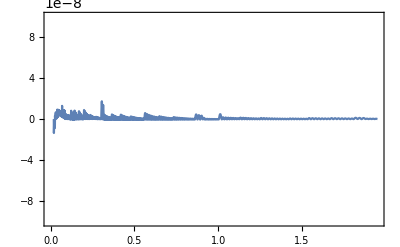

```mathematica
Plot[1/av*aoft@tofa@av-1,{av,a[Ti],a[Ti]*100},PlotRange->{-10^-7,10^-7},Frame->True]
```

We define the temperature as a function of time. Since we have T(a) (conserved entropy) and a(t) (Friedman equation), we just combine both.
In case of incomplete decoupling of neutrinos, we could not use conservation of entropy to get T(a) but we used the fit for the heating rate which allowed us to obtain numericall T(a) and a(T).

```mathematica
Toft[tv_]:=Tofa[aoft[tv]];
```

## Initial nuclear conditions

We use equilibrium solution for the initial condition. This equation A15 of compantion paper.

```mathematica
Yni[Tv_]:=1/(1+(1-3/2 Q/mn)Exp[Q/(kB Tv)]);
Ypi[Tv_]:=1-Yni[Tv];
```

Other initial conditions based on the equation and the rates. It is better when including corrections because these are the correct initial conditions whatever the corrections.

```mathematica
Yn2i[Tv_]:=LpTOn[Tv]/(LpTOn[Tv]+LnTOp[Tv]);
Yp2i[Tv_]:=1-Yn2i[Tv];
```

We see that the difference is very small

```mathematica
Yni[10^11.5]
Yn2i[10^11.5]
```

0.488653

0.488966

Actual list of initial conditions. Vanishing for everything except protons and neutrons

```mathematica
CIList[Tv_]:=Table[Which[i==1,Yni[Tv],i==2,Ypi[Tv],i≥3,0],{i,1,NumberVariable}]
```

## Construction of differential equations

The function DefineEquations wraps the definition of differential equations. This must be called any time we regenerate the probabilities on the reaction rates when including uncertainties on reaction rates in a Monte-Carlo analysis.

```mathematica
DefineEquations:=(

(*We build the differential system for the High temperatures *)
(* So we associate the r.h.s which is constructed thanks to DYOnlyPEN, with the l.h.s made of abundances derivatives *)
SystemEquationsHT[tv_]=Thread[Equal[FunPrimeList[tv],(DYOnlyPEN[Tv,ρBv,tv](*/.Dispatch@ReactionProbabilities*))]]/.{Tv->Toft@tv,ρBv->ρBForBBN@a@Toft@tv};

(* For middle and low temperature we distinguish between the compiled and the uncompiled method *)

If[$CompileNDSolve,

(* If $CompileNDSolve=True, we reinterpolate the rates for the middle and the low temperatures. *)
(* The system is a matrix system in this case and it is built directly in NDSolve below *)
RulesλRHSI=MyInterpolationRate@Table[{Tv,MyChop@RulesλRHS[Tv]},{Tv,ListTRange[Tf,T18]}];
RulesλbarRHSI=MyInterpolationRate@Table[{Tv,MyChop@RulesλbarRHS[Tv]},{Tv,ListTRange[Tf,T18]}];
       RulesλRHS18I=MyInterpolationRate@Table[{Tv,RulesλRHS[NReactionsSmallNetwork,Tv]},{Tv,ListTRange[T18,TMiddle]}];
RulesλbarRHS18I=MyInterpolationRate@Table[{Tv,RulesλbarRHS[NReactionsSmallNetwork,Tv]},{Tv,ListTRange[T18,TMiddle]}];,

(* If $CompileNDSolve=False, we (re-)define the systems of equations for Middle and Low temperatures*)
(* We associate the r.h.s formed thanks to DY18 and DY, with the l.h.s made of derivatives *)
SystemEquationsMT[tv_]=Thread[Equal[FunPrimeList[tv],(DY18[Tv,ρBv,tv])]]/.{Tv->Toft@tv,ρBv->ρBForBBN@a@Toft@tv};
SystemEquationsLT[tv_]=Thread[Equal[FunPrimeList[tv],(DY[Tv,ρBv,tv])]]/.{Tv->Toft@tv,ρBv->ρBForBBN@a@Toft@tv};
]
)
```

```mathematica
DefineEquations;//Timing
```

{0.22002,Null}

## Time delimitation of low, middle and high temperature eras

The time delimitation corresponding to Temperature delimitations of high, middle and low temperature eras.

```mathematica
t0:=tofa@a[Tstart];
tmiddle:=tofa@a[TMiddle];
t18:=tofa@a[T18];
tend:=tofa@a[Tend];
```

Let us check the values in seconds or t0< tmiddle < t18 < tend

```mathematica
{t0,tmiddle,t18,tend}
```

{0.00994812,1.00698,99.7063,49227.5}

## High temperature integration (n and p only)

The initial conditions at high temperature are found from thermal and chemical equilibrium. This is used to integrate from 10^11 K to 10^10 K.    We keep track only of neutrons and protons.

```mathematica
HoldYNames[period_String]:=ToExpression/@("Hold@Y[\""<>period<>"\"][\""<>#<>"\"]"&/@ShortNames);
```

Initial conditions

```mathematica
InitialConditionsHT[tv_]:=Thread[Equal[FunList[tv],CIList[Toft[tv]]]];
```

Actual solver. It solves the system and affects the results to the functions YHT[“n”] (neutrons) and YHT[“p”] (protons) which are functions of time.

```mathematica
SolveValueHighTemperatures:=(Thread[MySet[Evaluate[HoldYNames["HT"]],
NDSolveValue[
Flatten@Join[SystemEquationsHT[tv],InitialConditionsHT[t0]],
VarList,{tv,t0,tmiddle},
PrecisionGoal->8+PrecisionNDSolve,AccuracyGoal->11,InterpolationOrder->InterpOrder]]];
tHT=Y["HT"]["n"][[3,1]];
);
```

This period is very quick to solve as can be checked. The variable tHT stores the time steps used by the solver in case we are interested.

```mathematica
AbsoluteTiming[SolveValueHighTemperatures;]
```

{0.086511,Null}

We can also extend this integration with only weak interactions to much later times to see what would happen without nuclear reactions.
This is only to perform plots in the paper.

```mathematica
SolveValueHighTemperaturesYnOnly:=(Thread[MySet[Evaluate[HoldYNames["WeakInteractionsOnly"]],
NDSolveValue[
Flatten@Join[SystemEquationsHT[tv],InitialConditionsHT[t0]],
VarList,
{tv,t0,tend},PrecisionGoal->8+PrecisionNDSolve,AccuracyGoal->11(* 11*),
InterpolationOrder->InterpOrder]]];
);
```

```mathematica
If[$ResultsPlots,SolveValueHighTemperaturesYnOnly;];
```

## Middle temperature integration (n,p,d,t,He3,He4,Be7,Li7)

The end values for neutrons and protons at high temperatures are used as initial conditions for the middle temperature era. 
We use thermostatistical equilibrium for the species defined in the list ListThermalValuesMT below, and 0 otherwise.

```mathematica
ListThermalValuesMT={"d","t","He3","a","Be7","Li7"};
ListThermalValuesUsedMT=Intersection[VariablesInEquations,ListThermalValuesMT]
```

{a,Be7,d,He3,Li7,t}

We check the initial value used for the middle temperature era.

```mathematica
YPeriodTimeOrStateEquilibrium["HT",ListThermalValuesUsedMT][TMiddle,tmiddle]
```

{0.240275,0.759725,8.88112×10^-13,3.22512×10^-23,4.2103×10^-23,1.58×10^-26,1.39247×10^-60,6.54517×10^-61}

```mathematica
InitialConditionsMT[Tv_,tv_]:=Thread[Equal[FunList[tv],YPeriodTimeOrStateEquilibrium["HT",ListThermalValuesUsedMT][Tv,tv]]];
```

We then have the differential equation solver. There are two possibilities depending on if we use the compiled version or not. 
The values are then affected to the YMT[“n”], YMT[“n”], YMT[“d”] etc... which are the abundances of species in this era.

```mathematica
SolveValueMiddleTemperatures:=(If[$CompileNDSolve,
(* Compiled version.*)
resMT=NDSolveValue[
{Ytab'[tv]==DY18CN[ρBForBBN@a@Toft@tv,RulesλRHS18I[Toft@tv],RulesλbarRHS18I[Toft@tv],Ytab[tv]],Ytab[tmiddle]==YPeriodTimeOrStateEquilibrium["HT",ListThermalValuesUsedMT][TMiddle,tmiddle]},
Ytab,{tv,tmiddle,t18},
Method->{"BDF","MaxDifferenceOrder"->$BDFOrder},
PrecisionGoal->7+PrecisionNDSolve,AccuracyGoal->11,
InterpolationOrder->InterpOrder,Compiled->Automatic];
Y["MT"][key_][tv_?NumericQ]:=resMT[tv][[KeyVal[key]]];
tMT=resMT[[3,1]];,

(* Non compiled version. Slightly slower *)
Thread[MySet[Evaluate[HoldYNames["MT"]],NDSolveValue[
Flatten@Join[SystemEquationsMT[tv],InitialConditionsMT[TMiddle,tmiddle]],
VarList,{tv,tmiddle,t18},
Method->{"BDF","MaxDifferenceOrder"->$BDFOrder},
PrecisionGoal->7+PrecisionNDSolve,AccuracyGoal->11,
InterpolationOrder->InterpOrder,Compiled->False]]];
tMT=Y["MT"]["n"][[3,1]];
]);
```

NB: tMT stores the time steps used. Can be used to check the behaviour of the integrator.

```mathematica
AbsoluteTiming[SolveValueMiddleTemperatures;]
```

{0.279028,Null}

For information we plot the result of the integration

```mathematica
If[$ResultsPlots,LogLogPlot[Evaluate[YPeriodTime["MT"][tv]],{tv,tmiddle,t18},Frame->True,PlotRange->{10^-40,10},FrameLabel->{"t(s)","Y_i"}]]
```

## Low temperature integration (n,p,d,t,He3,He4,Be7,Li7)

!With the reduce network the list of nuclides is the same as in middle temperature range!

The end values at middle temperatures are then used as initial conditions for the low temperature era.
Now the full system of equations is used.

```mathematica
InitialConditionsLT[tv_]:=Thread[Equal[FunList[tv],YPeriodTime["MT"][tv]]];
```

```mathematica
SolveValueLowTemperatures:=(If[$CompileNDSolve,
(* Compiled version*)
resLT=NDSolveValue[
{Ytab'[tv]==DYCN[ρBForBBN@a@Toft@tv,RulesλRHSI[Toft@tv],RulesλbarRHSI[Toft@tv],Ytab[tv]],
Ytab[t18]==YPeriodTime["MT"][t18]},
Ytab,{tv,t18,tend},
Method->{"BDF","MaxDifferenceOrder"->$BDFOrder},
PrecisionGoal->5+PrecisionNDSolve,AccuracyGoal->AccuracyNDSolve,
InterpolationOrder->InterpOrder,StartingStepSize->10^-4,MaxStepSize->500];
Y["LT"][key_][tv_?NumericQ]:=resLT[tv][[KeyVal[key]]];
tLT=resLT[[3,1]];,

(* Uncompiled version. Slower. *)
Thread[MySet[Evaluate[HoldYNames["LT"]],NDSolveValue[
Flatten@Join[SystemEquationsLT[tv],InitialConditionsLT[t18]],
VarList,{tv,t18,tend},
Method->{"BDF","MaxDifferenceOrder"->$BDFOrder,"EquationSimplification"->"Solve"},
PrecisionGoal->5+PrecisionNDSolve,AccuracyGoal->AccuracyNDSolve,
InterpolationOrder->InterpOrder,StartingStepSize->10^-4]]];
tLT=Y["LT"]["n"][[3,1]];
];)
```

```mathematica
AbsoluteTiming[SolveValueLowTemperatures;]
```

{0.984677,Null}

We can plot the results

```mathematica
If[$ResultsPlots,LogLogPlot[Evaluate[YPeriodTime["LT"][tv]],{tv,t18,tend},Frame->True,PlotRange->{10^-40,10},FrameLabel->{"t(s)","Y_i"}]]
```

## Gathering integrations on all periods in one function

We define an interpolation of the results. We join the results from high, middle and low temperature eras. This is joined in the function 

YI[“key”][time] where key is the name of the nuclide (e.g. “a” for He4, “t” for tritium and “d” for deuterium but otherwise “Li7”, “C12” etc...).

```mathematica
InterpolateResults=(
Clear[Yall,YI];
Yall[key_?KeyQ]:=Yall[key]=Function[{tv},Piecewise[{{Y["HT"][key][tv],tv<tmiddle},{Y["MT"][key][tv],tv<t18&&tv>=tmiddle},{Y["LT"][key][tv],tv<=tend&&tv>=t18}}]];

YI[key_?KeyQ]:=YI[key]=Interpolation[Table[{tv,Yall[key][tv]},{tv,Join[tHT,Rest@tMT,Rest@tLT]}],InterpolationOrder->1];);
```

```mathematica
InterpolateResults;
```

The function RunNumericalIntegrals below performs the integrations of incomplete neutrino decoupling
and then the Friedmann equation integration.
Then it defines the nuclear reactions, possibly having introduced uncertainty on rates depending on options, 
and solves for the high, middle and low temperature era. 
This is the Driver of PRIMAT which needs to be called whenever we rerun PRIMAT with new parameters (e.g. exploring dependence in baryons or neutrinos).

```mathematica
RunNumericalIntegralsNuclearReactions:=(
(* Middle temperature integration *)
SolveValueMiddleTemperatures;

(* Low temperature integration *)
SolveValueLowTemperatures;
);
```

```mathematica
RunNumericalIntegrals:=(

(* In case of incomplete neutrino decoupling, we recompute all the integrations a(T) then inversion T(a), then Subscript[ρ, ν](a).*)
If[$IncompleteNeutrinoDecoupling,RecomputeIncompleteNeutrinoDecoupling;];

(*In case the plasma conditions have changed in a MC exploration, we recompute the inversion of a[T]*)
(* This is needed if we have recomputed the neutrino decoupling, but I am wondering if this is always needed. *)
InvertaOFT;

(* scale factor integration from Friedmann equation. *)
Computetofa;
Computeaoft;

(* Build equations. Needed since rate are modified randomly by the f factor of each reaction*)
LoadRates;
DefineEquations;

(* High temperature integration with only PEN reactions *)
SolveValueHighTemperatures;

(* Middle and Low temperature WITH nuclear reactions*)
RunNumericalIntegralsNuclearReactions;

InterpolateResults;
);
```

## Gathering the numerical results

We define a pseudo-mass fraction as a function of time using the interpolated results

```mathematica
XI[key_?KeyQ][t_]:=Ai[key]YI[key][t]
```

Final abundances are obtained by evaluation at t = tend.

We define a shorthand for the final abundances (Yf) and pseudo mass fraction (Xf).

```mathematica
Yf[key_]:=YLT[key][tend]
Xf[key_]:=Ai[key]Yf[key]
```

And a shorthand  notation for Y_i/H

```mathematica
YfH[key_]:=Yf[key]/Yf["p"]
```

## Results and plots

## Checks of the conservation of total number of baryons

The total number MUST be conserved. We build it from the nuclear weights of species.
At high temperatures we check visually. By construction the quantity Ytot = Σ_i A_i Y_i should be 1 and conserved. We define it and plot the difference with unity.

```mathematica
Ytot[period_String]:=Function[{tv},Plus@@(WeightsNuclear*YPeriodTime[period][tv])];
```

High temperature era

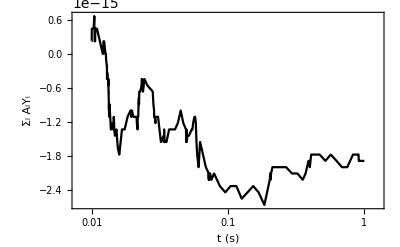

```mathematica
LogLinearPlot[Ytot["HT"][tv]-1,{tv,t0,tmiddle},Frame->True,FrameLabel->{"t (s)","Σ_i A_iY_i"},PlotStyle->Black]
```

Middle temperature era

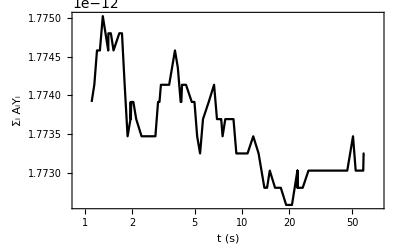

```mathematica
LogLinearPlot[Ytot["MT"][tv]-1,{tv,tmiddle*1.1,0.6t18},Frame->True,FrameLabel->{"t (s)","Σ_i A_iY_i"},PlotStyle->Black]
```

Low temperature era with the full network.

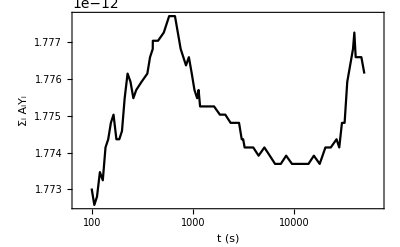

```mathematica
LogLinearPlot[Ytot["LT"][t]-1,{t,t18,tend},Frame->True,FrameLabel->{"t (s)","Σ_i A_iY_i"},PlotStyle->Black]
```

## Time evolution of abundances

### Early thermodynamical equilibrium

Estimate of T_nuc (see companion paper)

```mathematica
TFreeze=0.8 MeV/kB;
tFreeze=tofa@a@TFreeze
YnF[tv_]:=1/(1+Exp[Q/kB/TFreeze])Exp[-(tv-tFreeze)/τneutron ];
YpF[tv_]:=1-YnF[tv];
```

1.17063

```mathematica
tnuc=FindRoot[YNSE["d",YnF[tv],YpF[tv],Toft[tv]]==YnF[tv],{tv,100}][[1,2]]
Tnuc=Toft[tnuc]
```

296.855

7.69409×10^8

Abundance of neutrons at T_nuc and T_nuc in MeV

```mathematica
YnF[tnuc]
kB*Tnuc/MeV
```

0.118365

0.0663025

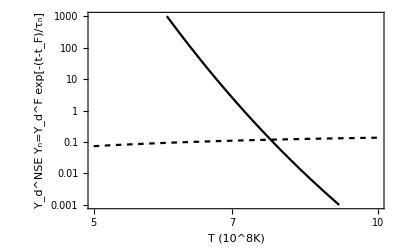

```mathematica
PlotDeutEq=Show[LogLogPlot[{YnF[tofa@a[10^8 Tv]],YNSE["d",YnF[tofa@a[10^8Tv]],YpF[tofa@a[10^8Tv]],10^8Tv]},{Tv,0.05*10^2,0.1*10^2},GridLines->{{{Tnuc,{Gray,Thickness[0.005]}}},{}},Frame->True,PlotRange->{{0.05*10^2,0.1*10^2},{10^-3,10^3}},PlotRangePadding->None,FrameStyle->Thickness[0.004],PlotStyle->{{Black,Thickness[0.004],Dashing[0.01]},{Black,Thickness[0.004]}},PlotRange->{10^-3,1000},FrameLabel->{"T (10^8K)","Y_d^NSE      Y_n=Y_d^F exp[-(t-t_F)/τ_n]"},LabelStyle->{FontSize->12}],
Graphics[{Rotate[Text[Style["0.066 MeV",FontSize->10,Black],{Log@Tnuc-0.015,2}],90 Degree]}]]

If[$ResultsPlots,Export["Plots/PlotDeutEq.pdf",Style[PlotDeutEq,Magnification->1],"PDF"];]
```

Checks of thermo equilibrium at early times.
We check the accuracy of thermal equilibrium for “d” “t” “a” “Li7”. 
Most important is deuterium because it determines the final Helium abundance.

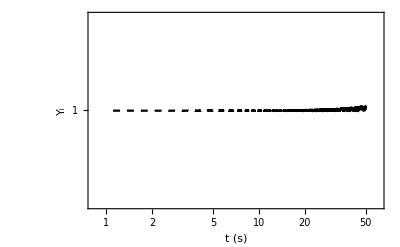

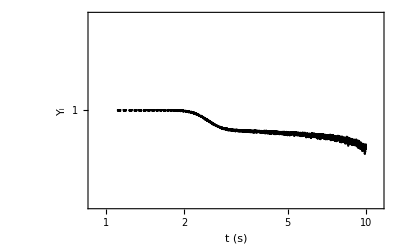

```mathematica
LogLogPlot[{YI["d"][tv]/YNSE["d",YI["n"][tv],YI["p"][tv],Toft[tv]]},{tv,tmiddle*1.1,50},Frame->True,FrameLabel->{"t (s)","Y_i"},PlotStyle->{Black,{Black,Dashed}},ImagePadding->{{50,10},{40,25}},PlotRange->{0.999,1.001}]

LogLogPlot[{YI["t"][tv]/YNSE["t",YI["n"][tv],YI["p"][tv],Toft[tv]]},{tv,tmiddle*1.1,10},Frame->True,FrameLabel->{"t (s)","Y_i"},PlotStyle->{Black,{Black,Dashed}},ImagePadding->{{50,10},{40,25}},PlotRange->{0.999,1.001}]

(*LogLogPlot[{YI["a"][tv]/YNSE["a",YI["n"][tv],YI["p"][tv],Toft[tv]]},{tv,tmiddle*1.1,1.5},Frame->True,FrameLabel->{"t (s)","Y_i"},PlotStyle->{Black,{Black,Dashed}},FrameTicks->MyTicks,ImagePadding->{{50,10},{40,25}},PlotRange->{0.999,1.001}]

LogLogPlot[{YI["Li7"][tv]/YNSE["Li7",YI["n"][tv],YI["p"][tv],Toft[tv]]},{tv,tmiddle*1.1,1.5},Frame->True,FrameLabel->{"t (s)","Y_i"},PlotStyle->{Black,{Black,Dashed}},FrameTicks->MyTicks,ImagePadding->{{50,10},{40,25}},PlotRange->{0.999,1.001}]*)
```

We plot early values together with thermal equilibrium in dashes

```mathematica
MyTickst={{Automatic,Automatic},{Automatic,{{tofa@a[10^11],"10^11K"},{tofa@a[10^10.5],"10^10.5K"},{tofa@a[10^10],"10^10K"},{tofa@a[10^9.5],"10^9.5K"},{tofa@a[10^9],"10^9K"},{tofa@a[10^8.5],"10^8.5K"},{tofa@a[10^8],"10^8K"}}}};
```

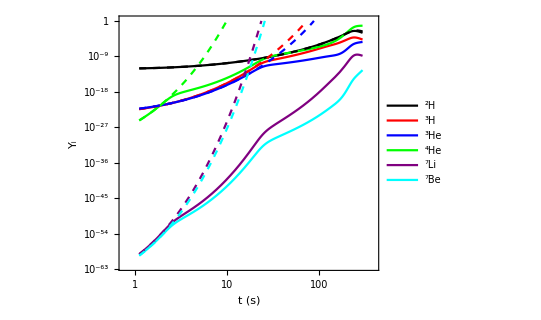

```mathematica
PL1=LogLogPlot[{YI["d"][tv],YI["t"][tv],YI["He3"][tv],YI["a"][tv],YI["Li7"][tv],YI["Be7"][tv],YNSE["d",YI["n"][tv],YI["p"][tv],Toft[tv]],YNSE["t",YI["n"][tv],YI["p"][tv],Toft[tv]],YNSE["He3",YI["n"][tv],YI["p"][tv],Toft[tv]],YNSE["a",YI["n"][tv],YI["p"][tv],Toft[tv]],YNSE["Li7",YI["n"][tv],YI["p"][tv],Toft[tv]],YNSE["Be7",YI["n"][tv],YI["p"][tv],Toft[tv]]},{tv,tmiddle*1.1,300},Frame->True,FrameLabel->{"t (s)","Y_i"},FrameTicks->MyTickst,LabelStyle->{FontSize->13},FrameStyle->Thickness[0.004],PlotRange->{10^-62,1},AspectRatio->.8,PlotStyle->{Black,Red,Blue,Green,Purple,Cyan,{Black,Dashed},{Red,Dashed},{Blue,Dashed},{Green,Dashed},{Purple,Dashed},{Cyan,Dashed}},(*ImagePadding->{{50,10},{40,25}},*)PlotLegends->Placed[LineLegend[{"^2H","^3H","^3He","^4He","^7Li","^7Be"},LegendLayout->(Grid[#,Frame->None]&)],Left]]

If[$ResultsPlots,Export["Plots/PlotEarlyEquilibrium.pdf",Style[PL1,Magnification->1],"PDF"];]
```

### Neutrons only evolution

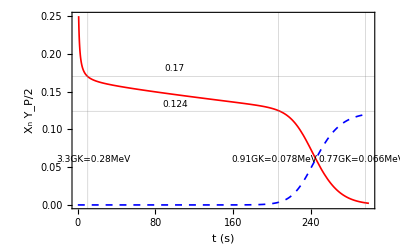

```mathematica
YnCoc=Show[Plot[{YI["n"][tv],Y["WeakInteractionsOnly"]["n"][tv],YI["a"][tv]*2(*,1/(1+Exp[Q/kB/Toft[tv]])*)},{tv,t0,300},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,{{tofa@a[10^9],"1GK"},{tofa@a[.8*10^9],"0.8GK"},{tofa@a[.9*10^9],"0.9GK"},{tofa@a[1.2*10^9],"1.2GK"},{tofa@a[2 10^9],"2GK"}}}},FrameStyle->Thickness[0.004],FrameLabel->{"t (s)","X_n    Y_P/2"},LabelStyle->{FontSize->12},PlotStyle->{{Red,Thickness[0.003]},{Red, Thickness[0.003],Dotted},{Blue, Thickness[0.003],Dashed}},PlotRange->{0,0.25},GridLines->{{{tofa@a[3.3 Giga Kelvin],{Gray,Thickness[0.003]}},{tofa@a[0.91 Giga Kelvin],{Gray,Thickness[0.003]}},{tofa@a[0.77 10^9],{Gray,Thickness[0.003]}}},{{0.124,{Gray,Thickness[0.003]}},{0.17,{Gray,Thickness[0.003]}}}}],
Graphics[{Rotate[Text[Style["3.3GK=0.28MeV",FontSize->9,Black],{16,0.06}],90 Degree],Rotate[Text[Style["0.91GK=0.078MeV",FontSize->9,Black],{203,0.06}],90 Degree],
Rotate[Text[Style["0.77GK=0.066MeV",FontSize->9,Black],{292,0.06}],90 Degree],
Rotate[Text[Style["0.17",FontSize->9,Black],{100,0.18}],0 Degree],
Rotate[Text[Style["0.124",FontSize->9,Black],{100,0.133}],0 Degree]}]]

If[$ResultsPlots,Export["Plots/PlotYnCoc.pdf",Style[YnCoc,Magnification->1],"PDF"];]
```

### Main species of the small network

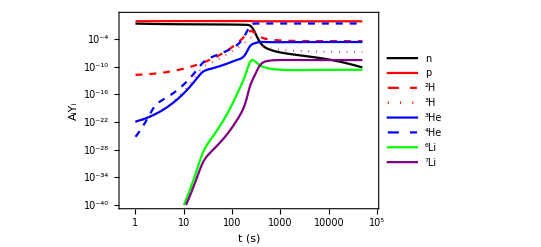

```mathematica
BBNsmall=LogLogPlot[{YI["n"][tv],YI["p"][tv],2YI["d"][tv],3YI["t"][tv],3YI["He3"][tv],4YI["a"][tv],YI["Li7"][tv],7YI["Be7"][tv]},{tv,tmiddle,tend},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{"t (s)","A_iY_i"},LabelStyle->{FontSize->12},PlotRange->{10^-40,10},PlotStyle->{Black,Red,{Red,Dashed},{Red,Dotted},Blue,{Blue,Dashed},Green,Purple},FrameTicks->MyTickst,ImagePadding->{{50,10},{40,25}},PlotLegends->Placed[LineLegend[{"n","p","^2H","^3H","^3He","^4He","^6Li","^7Li","^7Be"},LegendLayout->(Grid[#,Frame->None]&)],Right]]
```

```mathematica
If[$ResultsPlots,Export["Plots/BBNsmall.pdf",BBNsmall,"PDF"];]
```

## Final abundances

### Main results

Standard abundances as reported in most BBN papers.  Note the definition Y_P = 4 Y_He4. Since the atomic mass of Helium is not exactly 4 this is not exactly Helium mass abundance

```mathematica
MyGrid@Transpose[{{"H","Y_P=4Y_He","He_4/H x10^5","D/H x10^5","^3He/H x10^5","T/H x10^8","(^3He+T)/H x10^5","^7Li/H x10^11","^7Be/H x10^10","(^7Li+^7Be)/H x10^10"},{Yf["p"],4Yf["a"],YfH["a"] 10^5,YfH["d"] 10^5,YfH["He3"] 10^5,YfH["t"] 10^8,(YfH["t"]+YfH["He3"])10^5,YfH["Li7"] 10^11,YfH["Be7"] 10^10,(YfH["Li7"]+YfH["Be7"])10^10}}]
```

H | 0.752848
Y_P=4Y_He | 0.24709
He_4/H x10^5 | 8205.19
D/H x10^5 | 2.4585
^3He/H x10^5 | 1.06632
T/H x10^8 | 7.96071
(^3He+T)/H x10^5 | 1.07428
^7Li/H x10^11 | 2.94638
^7Be/H x10^10 | 5.43781
(^7Li+^7Be)/H x10^10 | 5.73245

### All final abundances

```mathematica
MyGrid[{#,Yf[#]}&/@ShortNames]
```

n | 7.28247×10^-11
p | 0.752848
d | 0.0000185088
t | 5.99321×10^-8
He3 | 8.0278×10^-6
a | 0.0617726
Li7 | 2.21817×10^-11
Be7 | 4.09385×10^-10

## Tools for Monte-Carlo on nuclear rates

We gather some tools for Monte-Carlo estimation of uncertainties from nuclear rates. 
Some Examples are provided in the Example folder.

There are 3 booleans which control what variables are varied randomly.
Nuclear rates
Neutron lifetime
And possibly baryons abundance according to [Planck 2015] results when this is interesting to vary it as well.

```mathematica
$ParallelBool=True;
$Randomτneutron=True;
$Randomh2Ωb=True;
```

Initialize Kernels (if parallelization this is called. It just distributes definitions)

```mathematica
InitializeKernels:=(
LaunchKernels[];
Print["Number of Kernels ",$KernelCount];
DistributeDefinitions[ReshapedTabulatedReactions,ListReactionsUpToChosenMass,LoadRates,DefineEquations,SystemEquationsHT,SystemEquationsMT,SystemEquationsLT,LoadRates,DY,DY18,DYOnlyPEN,LbarnTOp,LnTOp];
);
```

We define a function which launches the Monte-Carlo on subKernels and collects the results

```mathematica
RunPRIMATMonteCarlo[number_]:=Module[{res,time,Abundances,mytabfunctions,sss,RandomVariables,CosmoParametersList},
If[number>1,Print["Running a Monte-Carlo with ",number, " points."];];
Off[CompiledFunction::cfta];
mytabfunctions=If[$ParallelBool,ParallelTable,Table];
If[$ParallelBool,InitializeKernels;
ParallelEvaluate[$HistoryLength=0;]];

(* We always use the same seed so that we always use the same sequence of random number as advocated in [Cyburt et al. 2015].*)

res=mytabfunctions[
$Seed:=i;(* We use a different seed so that for each MC point we have a different sequence of reaction rates *)
InitializeRandom[$Seed];(* We restart our random list from the beginning *)

h2Ωb0=Meanh2Ωb0+If[$Randomh2Ωb,σh2Ωb0 NormalRealisation,0];
τneutron=Meanτneutron+If[$Randomτneutron,στneutron NormalRealisation,0];
CosmoParametersList={h2Ωb0,τneutron};

time=AbsoluteTiming[RunNumericalIntegrals][[1]];
RandomVariables=Rest@ListReactionsUpToChosenMass[[All,4]];
Share[];
Print["Iteration ",i, "  Memory usage = ",MemoryInUse[]," time = ",time, "  Kernel : ",$KernelID];
Abundances=YPeriodTime["LT"][tend];
ClearSystemCache[];
If[$Verbose,Print[Abundances(*," ",RandomVariables*)]];
{Abundances,RandomVariables,CosmoParametersList},{i,1,number}];
If[$ParallelBool,CloseKernels[]];

h2Ωb0=Meanh2Ωb0;
τneutron=Meanτneutron;
MC=res[[All,1]];
RV=res[[All,2]];
Cosmo=res[[All,3]];

res];

RunPRIMAT:=RunPRIMATMonteCarlo[1];
```

The results of RunPRIMAT are gathered in the files MC (abundances) RV (rates variations) Cosmo (List of cosmological paramters, limited to baryons abundances and neutron lifetime)

We define functions to dump the results of a Monte - Carlo in a file and also the converse to load the result so as to analyze and use it.

```mathematica
Clear[LoadMC,DumpMC]
```

```mathematica
DumpMC[File_String]:=(
Print["Exporting ","MonteCarlo/MC"<>File<>".dat"];
Export["MonteCarlo/MC"<>File<>".dat",MC];

Print["Exporting ","MonteCarlo/RV"<>File<>".dat"];
Export["MonteCarlo/RV"<>File<>".dat",RV];

Print["Exporting ","MonteCarlo/Cosmo"<>File<>".dat"];
Export["MonteCarlo/Cosmo"<>File<>".dat",Cosmo];);

LoadMC[File_String]:=(
MCfile="MonteCarlo/MC"<>File<>".dat";
RVfile="MonteCarlo/RV"<>File<>".dat";
Cosmofile="MonteCarlo/Cosmo"<>File<>".dat";
        MC=Import[MCfile];
RV=Import[RVfile];
Cosmo=Import[Cosmofile];
TMC=Transpose[MC];
);
```

Whenever a Monte-Carlo is finished, or loaded, we can obtain the table of values for a given element, or a given reaction

```mathematica
ElementColumn[el_]:=MC[[All,KeyVal[[el]]]];
ReactionColumn[el_]:=RV[[All,KeyNuclearReaction[el]]];
h2Ωb0List:=Cosmo[[All,1]];
τneutronList:=Cosmo[[All,2]];
```